### Definitions

```mathematica
(*Define particle Number Np, number of dimensions d, modes m natural length scales in terms of kappa (=k) as well as coordinates*)
Np =4;
d = 1;
lm = 1;
lp[k_]:=((k+1)^-(1/4))/lm;
$Assumptions = -1<k && Im[k]==0
xcoord={x1,x2,x3}
xpcoord = {x1p,x2p,x3p}
```

-1<k&&Im[k]==0

{x1,x2,x3}

{x1p,x2p,x3p}

```mathematica
(*Np is the number of fermions; d is the dimension; define p and q as in 2.25 of Harmonium1 document; 'a' and 'b' denote A and Subscript[B, N] of the Harmonium1 document*)
p[a_,b_, Np_]:=Sqrt[b/(a-b(Np-1))];
q2[x_,a_,b_,x1_,x2_,x1p_,x2p_, Np_]:=Sqrt[2a](x-b/(2(a-b(Np-1)))(x1+x2+x1p+x2p));
```

```mathematica
(*Define A, Subscript[B, N] and the natural length in terms of l_+=lp and l_-=s*)
A[lp_]:=1/(2 lp^2);
B[lm_,lp_, Np_]:=-1/(2Np) (1/lm^2-1/lp^2);
l[lm_,lp_, Np_]:=1/((((Np-1) lm^2+lp^2)/(lm^4 lp^2+(Np-1) lm^2 lp^4))^(1/4))
f[a_,b_,Np_] := ((Np-2)*b^2/2)/(a-(Np-2)b)-((Np-1)*b^2/2)/(a-(Np-1)b);
```

```mathematica
(*Define c and d of Mehler's formular, see 2.28 in Harmonium1 document; here c is c and d0 is d*)
c[s_,t_, Np_]:=Sqrt[Np/((Np-1) t^2+s^2)];
d0[s_,t_, Np_]:=Sqrt[((Np-1) s^2 +t^2)/(Np s^2 t^2)];
```

```mathematica
(*Define the q parameter in Mehler's formula, see 2.29 of Harmonium1 document*)
Q[s_,t_, Np_]:=(d0[s,t,Np]-c[s,t,Np])/(d0[s,t,Np]+c[s,t,Np]);
```

### Evaluating the normalization and describing spin sectors of the 2RDO

```mathematica
cp[a_,b_,Np_]:=((Np-2)*b^2/2)/(a-(Np-2)*b);
polyefunana[a_,b_,Np_,x1_, x1p_, x2_, x2p_]:= (-a(x1^2+x2^2+x1p^2+x2p^2))+(b((x1+x2)^2+(x1p+x2p)^2))+(cp[a,b,Np]*(x1+x1p+x2+x2p)^2);
```

```mathematica
polyefunana[a,b,4,x1,x1p,x2,x2p]
```

(b^2 (x1+x1p+x2+x2p)^2)/(a-2 b)-a (x1^2+x1p^2+x2^2+x2p^2)+b ((x1+x2)^2+(x1p+x2p)^2)

```mathematica
efun[a_,b_, x1_, x1p_, x2_, x2p_]:=Exp[-1/(2 (a-b))(b^2 (x1-x1p+x2-x2p)^2+2 a^2 (x1^2+x1p^2+x2^2+x2p^2)-4 a b (x1^2+x1p^2+x1 x2+x2^2+x1p x2p+x2p^2))];
```

```mathematica
rho2dd[a_,b_]:=(4 a^2 (a-3 b)^(3/2)  (x1-x2) (x1p-x2p))/(3 √((a (a-2 b))/(a-b)) √(a-b) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)
rho2uu[a_,b_]:=(4 a^2 (a-3 b)^(3/2)  (x1-x2) (x1p-x2p))/(3 √((a (a-2 b))/(a-b)) √(a-b) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)
rho2ud[a_,b_] := 1/(3 (a-2 b)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) (12 b^4+16 a^6 x1 x1p x2 x2p-4 a b^3 (5+b (3 x1^2+3 x1p^2+3 x2^2-2 x2 x2p+3 x2p^2+14 x1p (x2+x2p)-2 x1 (x1p-7 (x2+x2p))))-4 a^5 (2 b x1^2 (x2 x2p+x1p (x2+x2p))+x2 x2p (-1+2 b x1p (x1p+x2+x2p))+x1 (2 b x1p^2 (x2+x2p)+2 b x2 x2p (x2+x2p)+x1p (-1+2 b (x2^2+20 x2 x2p+x2p^2))))+a^4 (1-2 b (x1^2+16 x1 x1p+x1p^2+x2^2+16 x2 x2p+x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p (x2+x2p)^2+x1^3 (x1p+x2+x2p)+x1p^2 (2 x2^2+17 x2 x2p+2 x2p^2)+x1p (x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3)+x1^2 (2 x1p^2+2 x2^2+17 x2 x2p+2 x2p^2+17 x1p (x2+x2p))+x1 (x1p^3+x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3+17 x1p^2 (x2+x2p)+x1p (17 x2^2+156 x2 x2p+17 x2p^2))))-2 a^3 b (3-4 b (x1^2+x1p^2+x2^2+x1 (11 x1p-x2-x2p)+11 x2 x2p+x2p^2-x1p (x2+x2p))+b^2 (x1^4+x1p^4+12 x1p^3 (x2+x2p)+12 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (x2^2+10 x2 x2p+x2p^2)+2 x1p^2 (11 x2^2+50 x2 x2p+11 x2p^2)+4 x1p (3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3)+2 x1^2 (11 x1p^2+11 x2^2+50 x2 x2p+11 x2p^2+50 x1p (x2+x2p))+4 x1 (3 x1p^3+3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3+25 x1p^2 (x2+x2p)+x1p (25 x2^2+142 x2 x2p+25 x2p^2))))+a^2 b^2 (15-2 b (x1^2+42 x1 x1p+x1p^2+x2^2+42 x2 x2p+x2p^2-22 x1 (x2+x2p)-22 x1p (x2+x2p))+b^2 (5 x1^4+5 x1p^4+36 x1p^3 (x2+x2p)+36 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (5 x2^2+26 x2 x2p+5 x2p^2)+x1p^2 (62 x2^2+204 x2 x2p+62 x2p^2)+12 x1p (3 x2^3+17 x2^2 x2p+17 x2 x2p^2+3 x2p^3)+x1^2 (62 x1p^2+62 x2^2+204 x2 x2p+62 x2p^2+204 x1p (x2+x2p))+4 x1 (9 x1p^3+9 x2^3+51 x2^2 x2p+51 x2 x2p^2+9 x2p^3+51 x1p^2 (x2+x2p)+x1p (51 x2^2+206 x2 x2p+51 x2p^2)))))
rho2du[a_,b_]:=1/(3 (a-2 b)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) (12 b^4+16 a^6 x1 x1p x2 x2p-4 a b^3 (5+b (3 x1^2+3 x1p^2+3 x2^2-2 x2 x2p+3 x2p^2+14 x1p (x2+x2p)-2 x1 (x1p-7 (x2+x2p))))-4 a^5 (2 b x1^2 (x2 x2p+x1p (x2+x2p))+x2 x2p (-1+2 b x1p (x1p+x2+x2p))+x1 (2 b x1p^2 (x2+x2p)+2 b x2 x2p (x2+x2p)+x1p (-1+2 b (x2^2+20 x2 x2p+x2p^2))))+a^4 (1-2 b (x1^2+16 x1 x1p+x1p^2+x2^2+16 x2 x2p+x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p (x2+x2p)^2+x1^3 (x1p+x2+x2p)+x1p^2 (2 x2^2+17 x2 x2p+2 x2p^2)+x1p (x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3)+x1^2 (2 x1p^2+2 x2^2+17 x2 x2p+2 x2p^2+17 x1p (x2+x2p))+x1 (x1p^3+x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3+17 x1p^2 (x2+x2p)+x1p (17 x2^2+156 x2 x2p+17 x2p^2))))-2 a^3 b (3-4 b (x1^2+x1p^2+x2^2+x1 (11 x1p-x2-x2p)+11 x2 x2p+x2p^2-x1p (x2+x2p))+b^2 (x1^4+x1p^4+12 x1p^3 (x2+x2p)+12 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (x2^2+10 x2 x2p+x2p^2)+2 x1p^2 (11 x2^2+50 x2 x2p+11 x2p^2)+4 x1p (3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3)+2 x1^2 (11 x1p^2+11 x2^2+50 x2 x2p+11 x2p^2+50 x1p (x2+x2p))+4 x1 (3 x1p^3+3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3+25 x1p^2 (x2+x2p)+x1p (25 x2^2+142 x2 x2p+25 x2p^2))))+a^2 b^2 (15-2 b (x1^2+42 x1 x1p+x1p^2+x2^2+42 x2 x2p+x2p^2-22 x1 (x2+x2p)-22 x1p (x2+x2p))+b^2 (5 x1^4+5 x1p^4+36 x1p^3 (x2+x2p)+36 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (5 x2^2+26 x2 x2p+5 x2p^2)+x1p^2 (62 x2^2+204 x2 x2p+62 x2p^2)+12 x1p (3 x2^3+17 x2^2 x2p+17 x2 x2p^2+3 x2p^3)+x1^2 (62 x1p^2+62 x2^2+204 x2 x2p+62 x2p^2+204 x1p (x2+x2p))+4 x1 (9 x1p^3+9 x2^3+51 x2^2 x2p+51 x2 x2p^2+9 x2p^3+51 x1p^2 (x2+x2p)+x1p (51 x2^2+206 x2 x2p+51 x2p^2)))))
rho2uddu[a_, b_] :=-(((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b)(12 b^4+16 a^6 x1 x1p x2 x2p-4 a b^3 (5+b (3 x1^2+3 x1p^2-2 x1p x2+3 x2^2+2 x1 (7 x1p+7 x2-x2p)+14 x1p x2p+14 x2 x2p+3 x2p^2))-4 a^5 (2 b x1p^2 (x2 x2p+x1 (x2+x2p))+x1 x2p (-1+2 b x2 (x1+x2+x2p))+x1p (2 b x2^2 (x1+x2p)+2 b x1 x2p (x1+x2p)+x2 (-1+2 b (x1^2+20 x1 x2p+x2p^2))))+a^4 (1-2 b (x1^2+x1p^2+16 x1p x2+x2^2+16 x1 x2p+x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p (x2+x2p)^2+x1^3 (x1p+x2+x2p)+x1p^2 (2 x2^2+17 x2 x2p+2 x2p^2)+x1p (x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3)+x1^2 (2 x1p^2+2 x2^2+17 x2 x2p+2 x2p^2+17 x1p (x2+x2p))+x1 (x1p^3+x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3+17 x1p^2 (x2+x2p)+x1p (17 x2^2+156 x2 x2p+17 x2p^2))))-2 a^3 b (3-4 b (x1^2+x1p^2+11 x1p x2+x2^2-x1 (x1p+x2-11 x2p)-x1p x2p-x2 x2p+x2p^2)+b^2 (x1^4+x1p^4+12 x1p^3 (x2+x2p)+12 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (x2^2+10 x2 x2p+x2p^2)+2 x1p^2 (11 x2^2+50 x2 x2p+11 x2p^2)+4 x1p (3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3)+2 x1^2 (11 x1p^2+11 x2^2+50 x2 x2p+11 x2p^2+50 x1p (x2+x2p))+4 x1 (3 x1p^3+3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3+25 x1p^2 (x2+x2p)+x1p (25 x2^2+142 x2 x2p+25 x2p^2))))+a^2 b^2 (15-2 b (x1^2+x1p^2+42 x1p x2+x2^2-22 x1p x2p-22 x2 x2p+x2p^2+x1 (-22 x1p-22 x2+42 x2p))+b^2 (5 x1^4+5 x1p^4+36 x1p^3 (x2+x2p)+36 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (5 x2^2+26 x2 x2p+5 x2p^2)+x1p^2 (62 x2^2+204 x2 x2p+62 x2p^2)+12 x1p (3 x2^3+17 x2^2 x2p+17 x2 x2p^2+3 x2p^3)+x1^2 (62 x1p^2+62 x2^2+204 x2 x2p+62 x2p^2+204 x1p (x2+x2p))+4 x1 (9 x1p^3+9 x2^3+51 x2^2 x2p+51 x2 x2p^2+9 x2p^3+51 x1p^2 (x2+x2p)+x1p (51 x2^2+206 x2 x2p+51 x2p^2))))))/(3 (a-2 b)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π))
rho2duud[a_, b_] :=-(((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b)(12 b^4+16 a^6 x1 x1p x2 x2p-4 a b^3 (5+b (3 x1^2+3 x1p^2-2 x1p x2+3 x2^2+2 x1 (7 x1p+7 x2-x2p)+14 x1p x2p+14 x2 x2p+3 x2p^2))-4 a^5 (2 b x1p^2 (x2 x2p+x1 (x2+x2p))+x1 x2p (-1+2 b x2 (x1+x2+x2p))+x1p (2 b x2^2 (x1+x2p)+2 b x1 x2p (x1+x2p)+x2 (-1+2 b (x1^2+20 x1 x2p+x2p^2))))+a^4 (1-2 b (x1^2+x1p^2+16 x1p x2+x2^2+16 x1 x2p+x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p (x2+x2p)^2+x1^3 (x1p+x2+x2p)+x1p^2 (2 x2^2+17 x2 x2p+2 x2p^2)+x1p (x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3)+x1^2 (2 x1p^2+2 x2^2+17 x2 x2p+2 x2p^2+17 x1p (x2+x2p))+x1 (x1p^3+x2^3+17 x2^2 x2p+17 x2 x2p^2+x2p^3+17 x1p^2 (x2+x2p)+x1p (17 x2^2+156 x2 x2p+17 x2p^2))))-2 a^3 b (3-4 b (x1^2+x1p^2+11 x1p x2+x2^2-x1 (x1p+x2-11 x2p)-x1p x2p-x2 x2p+x2p^2)+b^2 (x1^4+x1p^4+12 x1p^3 (x2+x2p)+12 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (x2^2+10 x2 x2p+x2p^2)+2 x1p^2 (11 x2^2+50 x2 x2p+11 x2p^2)+4 x1p (3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3)+2 x1^2 (11 x1p^2+11 x2^2+50 x2 x2p+11 x2p^2+50 x1p (x2+x2p))+4 x1 (3 x1p^3+3 x2^3+25 x2^2 x2p+25 x2 x2p^2+3 x2p^3+25 x1p^2 (x2+x2p)+x1p (25 x2^2+142 x2 x2p+25 x2p^2))))+a^2 b^2 (15-2 b (x1^2+x1p^2+42 x1p x2+x2^2-22 x1p x2p-22 x2 x2p+x2p^2+x1 (-22 x1p-22 x2+42 x2p))+b^2 (5 x1^4+5 x1p^4+36 x1p^3 (x2+x2p)+36 x1^3 (x1p+x2+x2p)+(x2+x2p)^2 (5 x2^2+26 x2 x2p+5 x2p^2)+x1p^2 (62 x2^2+204 x2 x2p+62 x2p^2)+12 x1p (3 x2^3+17 x2^2 x2p+17 x2 x2p^2+3 x2p^3)+x1^2 (62 x1p^2+62 x2^2+204 x2 x2p+62 x2p^2+204 x1p (x2+x2p))+4 x1 (9 x1p^3+9 x2^3+51 x2^2 x2p+51 x2 x2p^2+9 x2p^3+51 x1p^2 (x2+x2p)+x1p (51 x2^2+206 x2 x2p+51 x2p^2))))))/(3 (a-2 b)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π))
rho2ddi[lm_,lp_,Np_]:=rho2dd[A[lp],B[lm,lp, Np]]
rho2udi[lm_,lp_,Np_]:=rho2ud[A[lp],B[lm,lp, Np]]
rho2dui[lm_,lp_,Np_]:=rho2du[A[lp],B[lm,lp, Np]]
rho2uddui[lm_,lp_,Np_]:=rho2uddu[A[lp],B[lm,lp, Np]]
rho2duudi[lm_,lp_,Np_]:=rho2duud[A[lp],B[lm,lp, Np]]
```

### Determining the coefficients of the Polynomial Contribution to the integral of the 2 - RDO

```mathematica
(*define 2 particle hf basis*)
(*modes are always defined such that for multi spin basis mode1 = UP and mode2 = DOWN*)
hfcoef[n_,x_, a_]:=(Factorial[n]2^n π^(1/2)  )^(-1/2)*(2*a)^(1/4)* HermiteH[n,(x*Sqrt[2a])]
hfbasisud[m1_, m2_,a_, x1_, x2_]:=1/Sqrt[2](hfcoef[m1,x1,a]*hfcoef[m2,x2, a])
hfbasisdu[m1_, m2_,a_,  x1_, x2_]:=1/Sqrt[2](-hfcoef[m1,x2,a]*hfcoef[m2,x1, a])
hfbasis[m1_, m2_, a_, x1_, x2_]:=1/Sqrt[2]*Det[{{hfcoef[m1,x1,a],hfcoef[m1,x2, a]}, {hfcoef[m2,x1,a],hfcoef[m2,x2, a]}}]
(*define with mode1, mode2, mode3, mode4 corresponds to unprimed and then primed coordinates*)
```

```mathematica
polystartuuuu[mode1_, mode2_, n1_, n2_]:=hfbasis[mode1,mode2, a, x1, x2]*hfbasis[n1,n2, a, x1p, x2p]*rho2uu[a,b]
polystartdddd[mode1_, mode2_, n1_, n2_]:=hfbasis[mode1,mode2, a, x1, x2]*hfbasis[n1,n2, a, x1p, x2p]*rho2dd[a,b]
```

```mathematica
(*polystartdd[1,2]*)
```

```mathematica
(*modes are always defined such that for multi spin basis mode1 = UP and mode2 = DOWN*)
```

```mathematica
polystartud[mode1_, mode2_, mode3_, mode4_]:=hfbasisud[mode1,mode2, a, x1, x2]*hfbasisud[mode3,mode4, a, x1p, x2p]*rho2ud[a,b]+hfbasisdu[mode1,mode2, a, x1, x2]*hfbasisdu[mode3,mode4, a, x1p, x2p]*rho2du[a,b]+hfbasisud[mode1,mode2, a, x1, x2]*hfbasisdu[mode3,mode4, a, x1p, x2p]*rho2uddu[a,b]+hfbasisdu[mode1,mode2, a, x1, x2]*hfbasisud[mode3,mode4, a, x1p, x2p]*rho2duud[a,b]
```

```mathematica
polystartudud[mode1_, mode2_, n1_, n2_]:=hfbasisud[mode1,mode2, a, x1, x2]*hfbasisud[n1,n2, a, x1p, x2p]*rho2ud[a,b]
```

```mathematica
polystartdudu[m1_,m2_,m3_,m4_]:=hfbasisdu[m1,m2, a, x1, x2]*hfbasisdu[m3,m4, a, x1p, x2p]*rho2du[a,b]

polystartuddu[m1_,m2_,m3_,m4_]:=hfbasisdu[m1,m2, a, x1, x2]*hfbasisud[m3,m4, a, x1p, x2p]*rho2uddu[a,b]

polystartduud[m1_,m2_,m3_,m4_]:=hfbasisud[m1,m2, a, x1, x2]*hfbasisdu[m3,m4, a, x1p, x2p]*rho2duud[a,b]
```

```mathematica
(*polystartud[0,0]*)
```

```mathematica
(*Determine the coefficients of the polynomial 'hfbasis' by the coefficientlist function where q corresponds to the power, i.e. x^q  *)

coefstart[poly_, x_,q_] :=CoefficientList[poly, x][[(q+1)]]
```

```mathematica
(*coefstart[polystartud[0,0],x1,0]*)
```

```mathematica
maxdegreestart[poly_, x_] := Length[CoefficientList[poly, x]]-1
```

```mathematica
maxdegreestart[polystartud[0,0],x1]
```

0

```mathematica
constantstart[poly_, x_] := coefstart[poly, x,1]
```

```mathematica
(*coefstart[polystartdd[1,2],x1,1]*)
```

```mathematica
Sum[coefstart[polystartdd[5,4],x1,q]*x1^q,{q,0,maxdegreestart[polystartdd[5,4],x1]}]-polystartdd[5,4]//Simplify
```

0

### Integrating coefficient by coefficient, defining helper functions

```mathematica
polycoef[poly_, x_,q_]:= CoefficientList[poly, x][[q+1]]
maxdegreepoly[poly_, x_]:=Length[CoefficientList[poly, x]]-1
```

```mathematica
exppolyinit=(-b^2 (x1-x1p+x2-x2p)^2-a^2 (x1^2+x1p^2+x2^2+x2p^2)+a b (3 x1^2+3 x1p^2+2 x1 x2+2 x1p x2p+3 (x2^2+x2p^2)))/(a-2 b)-a(x1^2+x2^2+x1p^2+x2p^2)
```

-a (x1^2+x1p^2+x2^2+x2p^2)+(-b^2 (x1-x1p+x2-x2p)^2-a^2 (x1^2+x1p^2+x2^2+x2p^2)+a b (3 x1^2+3 x1p^2+2 x1 x2+2 x1p x2p+3 (x2^2+x2p^2)))/(a-2 b)

```mathematica
efuncoef[exppoly_, x_,q_] :=CoefficientList[exppoly, x][[q+1]];
```

```mathematica
efuncoef[exppolyinit, x1, 0]
```

-a x1p^2-(a^2 x1p^2)/(a-2 b)+(3 a b x1p^2)/(a-2 b)-(b^2 x1p^2)/(a-2 b)+(2 b^2 x1p x2)/(a-2 b)-a x2^2-(a^2 x2^2)/(a-2 b)-(b^2 x2^2)/(a-2 b)+(2 a b x1p x2p)/(a-2 b)-(2 b^2 x1p x2p)/(a-2 b)+(2 b^2 x2 x2p)/(a-2 b)-a x2p^2-(a^2 x2p^2)/(a-2 b)-(b^2 x2p^2)/(a-2 b)+(3 a b (x2^2+x2p^2))/(a-2 b)

```mathematica
-a x1p^2+(a^2 x1p^2)/(a-2 b)-(3 a b x1p^2)/(a-2 b)+(b^2 x1p^2)/(a-2 b)-(2 b^2 x1p x2)/(a-2 b)-a x2^2+(a^2 x2^2)/(a-2 b)+(b^2 x2^2)/(a-2 b)-(2 a b x1p x2p)/(a-2 b)+(2 b^2 x1p x2p)/(a-2 b)-(2 b^2 x2 x2p)/(a-2 b)-a x2p^2+(a^2 x2p^2)/(a-2 b)+(b^2 x2p^2)/(a-2 b)-(3 a b (x2^2+x2p^2))/(a-2 b)
```

-a x1p^2+(a^2 x1p^2)/(a-2 b)-(3 a b x1p^2)/(a-2 b)+(b^2 x1p^2)/(a-2 b)-(2 b^2 x1p x2)/(a-2 b)-a x2^2+(a^2 x2^2)/(a-2 b)+(b^2 x2^2)/(a-2 b)-(2 a b x1p x2p)/(a-2 b)+(2 b^2 x1p x2p)/(a-2 b)-(2 b^2 x2 x2p)/(a-2 b)-a x2p^2+(a^2 x2p^2)/(a-2 b)+(b^2 x2p^2)/(a-2 b)-(3 a b (x2^2+x2p^2))/(a-2 b)

```mathematica
-(efuncoef[exppolyinit,x1,1])*(efuncoef[exppolyinit,x1,1])/(4*(efuncoef[exppolyinit,x1,2])) +efuncoef[exppolyinit,x1,0] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
exppolyinit-(Sum[efuncoef[exppolyinit,x1,q]*x1^q, {q,0,2}])  // Simplify
```

0

```mathematica
(*
 Integrate[x^m* Exp[a x^2+b x],{x,-∞,∞}, Assumptions->a<0 && m∈Integers && Im[b]==0]*)
```

```mathematica
intxmab[m_, a_, b_]:=1/2 (-a)^(-m/2) (1/a(-1+(-1)^m) b Gamma[1+m/2] Hypergeometric1F1[1+m/2,3/2,-b^2/(4 a)]+((1+(-1)^m) Gamma[(1+m)/2] Hypergeometric1F1[(1+m)/2,1/2,-b^2/(4 a)])/(√-a))
intxmabpoly[m_,a_,b_]:=intxmab[m,a,b]*Exp[(b^2)/(4a)]
```

```mathematica
intexppoly[a_,b_]:=-(b^2)/(4a)

(*spins s1, s2, s3, s4 read in unprimed, then primed coordinates*)
(*fix nested if for spins*)

spintopoly[s1_,s2_,s3_,s4_, m1_, m2_, m3_, m4_]:= If[s1==s2==s3==s4==-1, polystartdddd[m1,m2,m3,m4], If[s1==s2==s3==s4==+1, polystartuuuu[m1,m2,m3,m4], If[s1==s3==1&&s2==s4==-1, polystartudud[m1,m2,m3,m4], If[ s1==s3==-1&&s2==s4==+1, polystartdudu[m1,m2,m3,m4], If[s1==s4==1&&s2==s3==-1, polystartuddu[m1,m2,m3,m4], If[s1==s4==-1&&s2==s3==+1, polystartduud[m1,m2,m3,m4],0]]]]]]
```

```mathematica
int1poly[m1_,m2_,m3_,m4_, s1_, s2_,s3_,s4_]:= Sum[coefstart[spintopoly[s1,s2,s3,s4, m1, m2, m3, m4],x1, q ]*intxmabpoly[q,efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]], {q,0, maxdegreestart[spintopoly[s1,s2,s3,s4, m1, m2, m3, m4],x1]}]
```

```mathematica
int1polyud[m1_,m2_,m3_,m4_]:=Sum[coefstart[polystartud[ m1, m2, m3, m4],x1, q ]*intxmabpoly[q,efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]], {q,0, maxdegreestart[polystartud[ m1, m2, m3, m4],x1]}]
```

```mathematica
intgenpoly[ poly_, exppoly_, xint_]:= Sum[polycoef[poly,xint, q ]*intxmabpoly[q,efuncoef[exppoly, xint, 2], efuncoef[exppoly, xint, 1]], {q,0, maxdegreepoly[poly, xint]}]
```

## Running the algorithm

```mathematica
mode1 = 2;
mode2 = 3;
```

### Calculating diag66

```mathematica
spin1 = +1;
spin2 = +1;
spin3= +1;
spin4=+1;

poly1 = int1poly[mode1, mode2, mode1, mode2,  spin1, spin2, spin3, spin4]
```

-(8 a^(7/2) (a-3 b)^(3/2) x2^3 (x1p-x2p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)))/(3 √((a (a-2 b))/(a-b)) √(a-b) √(a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)-(4 a^(7/2) (a-3 b)^(3/2) x2^2 (x1p-x2p) ((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b)) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)))/(3 √((a (a-2 b))/(a-b)) √(a-b) (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)) √(a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)+(4 a^(7/2) (a-3 b)^(3/2) x2 (x1p-x2p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)) (1-(((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b))^2)/(2 (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)))))/(3 √((a (a-2 b))/(a-b)) √(a-b) (a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)+(2 a^(7/2) (a-3 b)^(3/2) (x1p-x2p) ((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b)) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)) (1-(((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b))^2)/(6 (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)))))/(√((a (a-2 b))/(a-b)) √(a-b) (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)) (a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

(8 a^4 (a-3 b)^(3/2) b^2 (x1p-x2p)^2 (x1p+x2p)^2)/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) (a^2-3 a b+b^2) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

(2 a^2 (a-3 b)^(3/2) b^2 (48 b^6+64 a^8 x2p^4-8 a b^5 (39+8 b x2p^2)-32 a^7 (x2p^2+22 b x2p^4)+3 a^2 b^4 (249+272 b x2p^2+192 b^2 x2p^4)+4 a^6 (3+84 b x2p^2+752 b^2 x2p^4)-8 a^5 b (15+168 b x2p^2+784 b^2 x2p^4)-3 a^3 b^3 (279+752 b x2p^2+1088 b^2 x2p^4)+a^4 b^2 (459+2536 b x2p^2+6592 b^2 x2p^4)))/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (2 a^2-7 a b+4 b^2)^4 √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(a^2 √(a-3 b) b^2)/(3 √((a (a-2 b))/(a-b)) (a-b)^(3/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intd66 = poly4*Exp[exppoly4] // Simplify
```

(a^2 √(a-3 b) b^2)/(3 √((a (a-2 b))/(a-b)) (a-b)^(3/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating diag77

```mathematica
spin1 = -1;
spin2 = -1;
spin3= -1;
spin4=-1;

poly1 = int1poly[mode1, mode2, mode1, mode2,  spin1, spin2, spin3, spin4]
```

-(8 a^(7/2) (a-3 b)^(3/2) x2^3 (x1p-x2p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)))/(3 √((a (a-2 b))/(a-b)) √(a-b) √(a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)-(4 a^(7/2) (a-3 b)^(3/2) x2^2 (x1p-x2p) ((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b)) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)))/(3 √((a (a-2 b))/(a-b)) √(a-b) (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)) √(a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)+(4 a^(7/2) (a-3 b)^(3/2) x2 (x1p-x2p) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)) (1-(((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b))^2)/(2 (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)))))/(3 √((a (a-2 b))/(a-b)) √(a-b) (a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)+(2 a^(7/2) (a-3 b)^(3/2) (x1p-x2p) ((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b)) (-(4 a^(3/2) x1p^2)/(√π)+(4 a^(3/2) x2p^2)/(√π)) (1-(((2 b^2 x1p)/(a-2 b)+(2 a b x2)/(a-2 b)-(2 b^2 x2)/(a-2 b)+(2 b^2 x2p)/(a-2 b))^2)/(6 (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)))))/(√((a (a-2 b))/(a-b)) √(a-b) (-a-a^2/(a-2 b)+(3 a b)/(a-2 b)-b^2/(a-2 b)) (a+a^2/(a-2 b)-(3 a b)/(a-2 b)+b^2/(a-2 b))^(3/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

(8 a^4 (a-3 b)^(3/2) b^2 (x1p-x2p)^2 (x1p+x2p)^2)/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) (a^2-3 a b+b^2) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

(2 a^2 (a-3 b)^(3/2) b^2 (48 b^6+64 a^8 x2p^4-8 a b^5 (39+8 b x2p^2)-32 a^7 (x2p^2+22 b x2p^4)+3 a^2 b^4 (249+272 b x2p^2+192 b^2 x2p^4)+4 a^6 (3+84 b x2p^2+752 b^2 x2p^4)-8 a^5 b (15+168 b x2p^2+784 b^2 x2p^4)-3 a^3 b^3 (279+752 b x2p^2+1088 b^2 x2p^4)+a^4 b^2 (459+2536 b x2p^2+6592 b^2 x2p^4)))/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (2 a^2-7 a b+4 b^2)^4 √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(a^2 √(a-3 b) b^2)/(3 √((a (a-2 b))/(a-b)) (a-b)^(3/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intd77 = poly4*Exp[exppoly4] // Simplify
```

(a^2 √(a-3 b) b^2)/(3 √((a (a-2 b))/(a-b)) (a-b)^(3/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating diag88

```mathematica
poly1 =int1polyud[ mode2,mode2,mode2,mode2] //Simplify
```

(a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) (-1+4 a x1p^2) (-1+4 a x2^2) (-1+4 a x2p^2) (-3 b^11+4096 a^13 x1p x2^2 x2p+2 a b^10 (37+2 b (6 x1p^2-4 x1p x2+x2^2+14 x1p x2p-4 x2 x2p+6 x2p^2))-256 a^12 (4 b x1p^2 x2 (2 x2-x2p+2 b x2^2 x2p)+x2 x2p (1+2 b x2 (3 x2+4 x2p))+x1p (x2+4 x2p+240 b x2^2 x2p-4 b x2 x2p^2+2 b x2^3 (3+4 b x2p^2)))+128 a^11 (-1+2 b (5 x1p^2+18 x1p x2+4 x2^2+61 x1p x2p+18 x2 x2p+5 x2p^2)+8 b^3 x2^2 (x1p^3 (x2-3 x2p)+x1p (26 x2-3 x2p) x2p^2+x2 x2p^2 (x2+x2p)+x1p^2 (x2^2+26 x2 x2p-6 x2p^2))-2 b^2 (2 x1p^3 (x2+3 x2p)+x1p^2 (-104 x2^2+66 x2 x2p+12 x2p^2)-x2 (2 x2^3+75 x2^2 x2p+104 x2 x2p^2-2 x2p^3)+x1p (-75 x2^3-1526 x2^2 x2p+66 x2 x2p^2+6 x2p^3)))-4 a^2 b^9 (200+b (75 x1p^2-66 x1p x2+36 x2^2+196 x1p x2p-66 x2 x2p+75 x2p^2)+b^2 (21 x1p^4-8 x2^4-4 x1p^3 (x2-26 x2p)+24 x2^3 x2p-24 x2^2 x2p^2-4 x2 x2p^3+21 x2p^4-2 x1p^2 (12 x2^2+6 x2 x2p-83 x2p^2)+4 x1p (6 x2^3-14 x2^2 x2p-3 x2 x2p^2+26 x2p^3)))+2 a^3 b^8 (2447+8 b^3 (x1p-x2+x2p)^2 (3 x1p^2+10 x1p x2p+3 x2p^2) (3 x1p^2+4 x1p x2-4 x2^2+6 x1p x2p+4 x2 x2p+3 x2p^2)+4 b (217 x1p^2-295 x1p x2+265 x2^2+674 x1p x2p-295 x2 x2p+217 x2p^2)+8 b^2 (22 x1p^4-34 x2^4+76 x2^3 x2p-57 x2^2 x2p^2+41 x2 x2p^3+22 x2p^4+x1p^3 (41 x2+146 x2p)+x1p^2 (-57 x2^2+151 x2 x2p+248 x2p^2)+x1p (76 x2^3-132 x2^2 x2p+151 x2 x2p^2+146 x2p^3)))+128 a^10 b (8-b (118 x1p^2+252 x1p x2+100 x2^2+775 x1p x2p+252 x2 x2p+118 x2p^2)+4 b^3 x2^2 (3 x1p^4+x1p^3 (-17 x2+78 x2p)-6 x1p^2 (3 x2^2+46 x2 x2p-25 x2p^2)+x2p (x2^3-18 x2^2 x2p-17 x2 x2p^2+3 x2p^3)+x1p (x2^3+4 x2^2 x2p-276 x2 x2p^2+78 x2p^3))+b^2 (6 x1p^4-36 x2^4-753 x2^3 x2p-1112 x2^2 x2p^2+60 x2 x2p^3+6 x2p^4+2 x1p^3 (30 x2+79 x2p)+x1p^2 (-1112 x2^2+896 x2 x2p+304 x2p^2)+x1p (-753 x2^3-10652 x2^2 x2p+896 x2 x2p^2+158 x2p^3)))-8 a^6 b^5 (6280+b (17216 x1p^2+2126 x1p x2+18236 x2^2+54323 x1p x2p+2126 x2 x2p+17216 x2p^2)-2 b^2 (3921 x1p^4+2050 x2^4-3558 x2^3 x2p-21487 x2^2 x2p^2+6188 x2 x2p^3+3921 x2p^4+7 x1p^3 (884 x2+3109 x2p)+x1p^2 (-21487 x2^2+22716 x2 x2p+35684 x2p^2)+x1p (-3558 x2^3-73044 x2^2 x2p+22716 x2 x2p^2+21763 x2p^3))+4 b^3 (160 x1p^6-64 x2^6-504 x2^5 x2p+908 x2^4 x2p^2+1446 x2^3 x2p^3-2313 x2^2 x2p^4+436 x2 x2p^5+160 x2p^6+4 x1p^5 (109 x2+406 x2p)+x1p^4 (-2313 x2^2+3152 x2 x2p+5056 x2p^2)+2 x1p^3 (723 x2^3-8778 x2^2 x2p+3638 x2 x2p^2+3592 x2p^3)+2 x1p^2 (454 x2^4+7201 x2^3 x2p-15243 x2^2 x2p^2+3638 x2 x2p^3+2528 x2p^4)-2 x1p (252 x2^5+740 x2^4 x2p-7201 x2^3 x2p^2+8778 x2^2 x2p^3-1576 x2 x2p^4-812 x2p^5)))+4 a^5 b^6 (10068+b (11590 x1p^2-6930 x1p x2+15533 x2^2+36670 x1p x2p-6930 x2 x2p+11590 x2p^2)-4 b^2 (1619 x1p^4+976 x2^4-684 x2^3 x2p-5719 x2^2 x2p^2+731 x2 x2p^3+1619 x2p^4+x1p^3 (731 x2+7600 x2p)+x1p^2 (-5719 x2^2+1545 x2 x2p+11962 x2p^2)+x1p (-684 x2^3-16458 x2^2 x2p+1545 x2 x2p^2+7600 x2p^3))+4 b^3 (240 x1p^6-16 x2^6-320 x2^5 x2p+232 x2^4 x2p^2+1684 x2^3 x2p^3-2191 x2^2 x2p^4+380 x2 x2p^5+240 x2p^6+4 x1p^5 (95 x2+531 x2p)+x1p^4 (-2191 x2^2+2276 x2 x2p+6336 x2p^2)+4 x1p^3 (421 x2^3-3481 x2^2 x2p+1232 x2 x2p^2+2226 x2p^3)+2 x1p^2 (116 x2^4+5574 x2^3 x2p-11733 x2^2 x2p^2+2464 x2 x2p^3+3168 x2p^4)-4 x1p (80 x2^5+380 x2^4 x2p-2787 x2^3 x2p^2+3481 x2^2 x2p^3-569 x2 x2p^4-531 x2p^5)))+64 a^9 b^2 (-28+b (1114 x1p^2+1755 x1p x2+991 x2^2+5268 x1p x2p+1755 x2 x2p+1114 x2p^2)-b^2 (132 x1p^4-208 x2^4-3805 x2^3 x2p-6278 x2^2 x2p^2+708 x2 x2p^3+132 x2p^4+4 x1p^3 (177 x2+427 x2p)+x1p^2 (-6278 x2^2+6428 x2 x2p+3152 x2p^2)+x1p (-3805 x2^3-44172 x2^2 x2p+6428 x2 x2p^2+1708 x2p^3))+4 b^3 (4 x1p^5 x2p+x1p^4 (-57 x2^2+12 x2 x2p+16 x2p^2)+x1p^3 (109 x2^3-804 x2^2 x2p+36 x2 x2p^2+24 x2p^3)+x2^2 (-2 x2^4-21 x2^3 x2p+124 x2^2 x2p^2+109 x2 x2p^3-57 x2p^4)+2 x1p^2 (62 x2^4+780 x2^3 x2p-747 x2^2 x2p^2+18 x2 x2p^3+8 x2p^4)+x1p (-21 x2^5-70 x2^4 x2p+1560 x2^3 x2p^2-804 x2^2 x2p^3+12 x2 x2p^4+4 x2p^5)))-16 a^8 b^3 (395+b (10616 x1p^2+9832 x2^2+12483 x2 x2p+10616 x2p^2+9 x1p (1387 x2+4544 x2p))-4 b^2 (547 x1p^4-126 x2^4-4946 x2^3 x2p-10091 x2^2 x2p^2+2026 x2 x2p^3+547 x2p^4+x1p^3 (2026 x2+4770 x2p)+x1p^2 (-10091 x2^2+12807 x2 x2p+8446 x2p^2)+x1p (-4946 x2^3-55258 x2^2 x2p+12807 x2 x2p^2+4770 x2p^3))+8 b^3 (4 x1p^6-20 x2^6-142 x2^5 x2p+436 x2^4 x2p^2+365 x2^3 x2p^3-396 x2^2 x2p^4+16 x2 x2p^5+4 x2p^6+16 x1p^5 (x2+5 x2p)-4 x1p^4 (99 x2^2-57 x2 x2p-71 x2p^2)+x1p^3 (365 x2^3-4158 x2^2 x2p+604 x2 x2p^2+416 x2p^3)+x1p^2 (436 x2^4+5233 x2^3 x2p-7524 x2^2 x2p^2+604 x2 x2p^3+284 x2p^4)+x1p (-142 x2^5-412 x2^4 x2p+5233 x2^3 x2p^2-4158 x2^2 x2p^3+228 x2 x2p^4+80 x2p^5)))-a^4 b^7 (18125+4 b (2347 x1p^2-3110 x1p x2+3876 x2^2+7778 x1p x2p-3110 x2 x2p+2347 x2p^2)-4 b^2 (861 x1p^4+976 x2^4-1168 x2^3 x2p-1628 x2^2 x2p^2-980 x2 x2p^3+861 x2p^4+x1p^3 (-980 x2+3020 x2p)-2 x1p^2 (814 x2^2+2102 x2 x2p-2159 x2p^2)-4 x1p (292 x2^3+1098 x2^2 x2p+1051 x2 x2p^2-755 x2p^3))+32 b^3 (39 x1p^6+5 x1p^5 (3 x2+62 x2p)+x1p^4 (-224 x2^2+63 x2 x2p+889 x2p^2)+2 x1p^3 (111 x2^3-628 x2^2 x2p+57 x2 x2p^2+618 x2p^3)+x1p^2 (-36 x2^4+1106 x2^3 x2p-2064 x2^2 x2p^2+114 x2 x2p^3+889 x2p^4)+x2p (-16 x2^5-36 x2^4 x2p+222 x2^3 x2p^2-224 x2^2 x2p^3+15 x2 x2p^4+39 x2p^5)+x1p (-16 x2^5-216 x2^4 x2p+1106 x2^3 x2p^2-1256 x2^2 x2p^3+63 x2 x2p^4+310 x2p^5)))+8 a^7 b^4 (3837+2 b (13331 x1p^2+9805 x1p x2+12892 x2^2+45057 x1p x2p+9805 x2 x2p+13331 x2p^2)-4 b^2 (2120 x1p^4+679 x2^4-6162 x2^3 x2p-19103 x2^2 x2p^2+5567 x2 x2p^3+2120 x2p^4+x1p^3 (5567 x2+14263 x2p)+x1p^2 (-19103 x2^2+26543 x2 x2p+24286 x2p^2)+x1p (-6162 x2^3-82633 x2^2 x2p+26543 x2 x2p^2+14263 x2p^3))+8 b^3 (44 x1p^6-60 x2^6-388 x2^5 x2p+897 x2^4 x2p^2+850 x2^3 x2p^3-1300 x2^2 x2p^4+156 x2 x2p^5+44 x2p^6+12 x1p^5 (13 x2+46 x2p)-4 x1p^4 (325 x2^2-350 x2 x2p-453 x2p^2)+x1p^3 (850 x2^3-11509 x2^2 x2p+3420 x2 x2p^2+2608 x2p^3)+x1p^2 (897 x2^4+11074 x2^3 x2p-20418 x2^2 x2p^2+3420 x2 x2p^3+1812 x2p^4)+x1p (-388 x2^5-1010 x2^4 x2p+11074 x2^3 x2p^2-11509 x2^2 x2p^3+1400 x2 x2p^4+552 x2p^5)))))/(12 (2 a^2-5 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

1/(96 (a^2-3 a b+b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-1+4 a x1p^2) (-1+4 a x2p^2) (16 b^15+128 a^16 x1p x2p-64 a^15 b (x1p^2+46 x1p x2p+x2p^2)-a b^14 (303+20 b (7 x1p^2+18 x1p x2p+7 x2p^2))-4 a^14 b (-7+20 b^2 x1p x2p (x1p+x2p)^2-2 b (169 x1p^2+3789 x1p x2p+169 x2p^2))+2 a^2 b^13 (1367+224 b^2 (x1p+x2p)^2 (x1p^2+3 x1p x2p+x2p^2)+b (709 x1p^2+2190 x1p x2p+709 x2p^2))-a^3 b^12 (15129+16 b^3 (x1p+x2p)^4 (41 x1p^2+134 x1p x2p+41 x2p^2)+4 b^2 (x1p+x2p)^2 (403 x1p^2+1886 x1p x2p+403 x2p^2)+8 b (1073 x1p^2+3929 x1p x2p+1073 x2p^2))-2 a^12 b^3 (-2492+32 b^3 x1p x2p (x1p+x2p)^4+2 b^2 (x1p+x2p)^2 (149 x1p^2+3166 x1p x2p+149 x2p^2)-27 b (1277 x1p^2+13610 x1p x2p+1277 x2p^2))+4 a^13 b^2 (-141+10 b^2 (x1p+x2p)^2 (x1p^2+38 x1p x2p+x2p^2)-b (3161 x1p^2+46068 x1p x2p+3161 x2p^2))-a^5 b^10 (140463+64 b^4 (x1p+x2p)^6 (13 x1p^2+54 x1p x2p+13 x2p^2)+16 b^3 (x1p+x2p)^4 (277 x1p^2+2112 x1p x2p+277 x2p^2)-36 b^2 (x1p+x2p)^2 (1277 x1p^2+2834 x1p x2p+1277 x2p^2)+24 b (8111 x1p^2+30481 x1p x2p+8111 x2p^2))+a^11 b^4 (-25443+32 b^3 (x1p+x2p)^4 (x1p^2+30 x1p x2p+x2p^2)+72 b^2 (x1p+x2p)^2 (53 x1p^2+846 x1p x2p+53 x2p^2)-24 b (10145 x1p^2+84301 x1p x2p+10145 x2p^2))+2 a^4 b^11 (27804+32 b^4 (x1p+x2p)^6 (3 x1p^2+10 x1p x2p+3 x2p^2)+20 b^3 (x1p+x2p)^4 (85 x1p^2+358 x1p x2p+85 x2p^2)-10 b^2 (x1p+x2p)^2 (341 x1p^2+70 x1p x2p+341 x2p^2)+b (23421 x1p^2+88666 x1p x2p+23421 x2p^2))+2 a^6 b^9 (124477+8 b^4 (x1p+x2p)^6 (79 x1p^2+434 x1p x2p+79 x2p^2)-4 b^3 (x1p+x2p)^4 (323 x1p^2-3786 x1p x2p+323 x2p^2)-2 b^2 (x1p+x2p)^2 (24341 x1p^2+81862 x1p x2p+24341 x2p^2)+9 b (29585 x1p^2+115066 x1p x2p+29585 x2p^2))+a^7 b^8 (-314607-32 b^4 (x1p+x2p)^6 (27 x1p^2+202 x1p x2p+27 x2p^2)+16 b^3 (x1p+x2p)^4 (595 x1p^2+176 x1p x2p+595 x2p^2)+4 b^2 (x1p+x2p)^2 (26533 x1p^2+134210 x1p x2p+26533 x2p^2)-8 b (119228 x1p^2+505335 x1p x2p+119228 x2p^2))+a^9 b^6 (-184689-32 b^4 (x1p+x2p)^6 (x1p^2+22 x1p x2p+x2p^2)+16 b^3 (x1p+x2p)^4 (179 x1p^2+1068 x1p x2p+179 x2p^2)+40 b^2 (x1p+x2p)^2 (929 x1p^2+9742 x1p x2p+929 x2p^2)-8 b (122707 x1p^2+690457 x1p x2p+122707 x2p^2))+2 a^10 b^5 (41673+32 b^4 x1p x2p (x1p+x2p)^6-8 b^3 (x1p+x2p)^4 (31 x1p^2+360 x1p x2p+31 x2p^2)-2 b^2 (x1p+x2p)^2 (3577 x1p^2+46934 x1p x2p+3577 x2p^2)+b (292611 x1p^2+1973006 x1p x2p+292611 x2p^2))+2 a^8 b^7 (142816+8 b^4 (x1p+x2p)^6 (17 x1p^2+190 x1p x2p+17 x2p^2)-12 b^3 (x1p+x2p)^4 (323 x1p^2+974 x1p x2p+323 x2p^2)-4 b^2 (x1p+x2p)^2 (9169 x1p^2+69448 x1p x2p+9169 x2p^2)+b (579311 x1p^2+2787798 x1p x2p+579311 x2p^2)))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-1+4 a x2p^2) (-8425472 b^18+65536 a^19 x2p^2-16384 a^18 (1+128 b x2p^2)+3072 a b^17 (40365+4168 b x2p^2)-1024 a^17 b (-501-30252 b x2p^2+52 b^2 x2p^4)+2048 a^16 b^2 (-3618-136801 b x2p^2+702 b^2 x2p^4)+512 a^2 b^16 (-1665957-717200 b x2p^2+168640 b^2 x2p^4)+256 a^15 b^3 (255861+6779012 b x2p^2-68688 b^2 x2p^4+80 b^3 x2p^6)-256 a^14 b^4 (1549281+30487732 b x2p^2-503280 b^2 x2p^4+1760 b^3 x2p^6)+256 a^13 b^5 (6816159+103012851 b x2p^2-2462148 b^2 x2p^4+17264 b^3 x2p^6)-64 a^12 b^6 (90242229+1068181252 b x2p^2-33949692 b^2 x2p^4+398368 b^3 x2p^6)-128 a^3 b^15 (-28553085-25647096 b x2p^2+4980672 b^2 x2p^4+424448 b^3 x2p^6)+16 a^4 b^14 (-683523117-996936352 b x2p^2+133342080 b^2 x2p^4+19597312 b^3 x2p^6+716800 b^4 x2p^8)-64 a^11 b^7 (-229631031-2152110229 b x2p^2+84859264 b^2 x2p^4-1483364 b^3 x2p^6+4160 b^4 x2p^8+256 b^5 x2p^10)+16 a^10 b^8 (-1821368367-13578830932 b x2p^2+624614808 b^2 x2p^4-14413760 b^3 x2p^6+227840 b^4 x2p^8+12288 b^5 x2p^10)+16 a^6 b^12 (-2561635293-7239426944 b x2p^2+486206352 b^2 x2p^4+50675200 b^3 x2p^6+6671360 b^4 x2p^8+147456 b^5 x2p^10)-4 a^5 b^13 (-6055103187-12697075736 b x2p^2+1146660224 b^2 x2p^4+180431872 b^3 x2p^6+13783040 b^4 x2p^8+163840 b^5 x2p^10)-4 a^9 b^9 (-11347353479-67284169192 b x2p^2+3417694380 b^2 x2p^4-83528672 b^3 x2p^6+5159680 b^4 x2p^8+239616 b^5 x2p^10)+4 a^8 b^10 (-13932967587-65397475442 b x2p^2+3529296192 b^2 x2p^4-40178304 b^3 x2p^6+15595520 b^4 x2p^8+606208 b^5 x2p^10)-3 a^7 b^11 (-17980425645-66119165032 b x2p^2+3813083072 b^2 x2p^4+121457152 b^3 x2p^6+36044800 b^4 x2p^8+1114112 b^5 x2p^10)))/(48 a (2 a^2-7 a b+4 b^2)^11 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (256 a^10-5120 a^9 b+44452 a^8 b^2-219712 a^7 b^3+682541 a^6 b^4-1391644 a^5 b^5+1892622 a^4 b^6-1708080 a^3 b^7+988824 a^2 b^8-340704 a b^9+66960 b^10))/(768 a^2 (a-3 b)^(11/2) (a-b)^(13/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intd88 = poly4*Exp[exppoly4] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (256 a^10-5120 a^9 b+44452 a^8 b^2-219712 a^7 b^3+682541 a^6 b^4-1391644 a^5 b^5+1892622 a^4 b^6-1708080 a^3 b^7+988824 a^2 b^8-340704 a b^9+66960 b^10))/(768 a^2 (a-3 b)^(11/2) (a-b)^(13/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating diag99

```mathematica
poly1 =int1polyud[ mode1,mode2,mode1,mode2] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) (-3 b^12+4 a b^11 (20+b (6 x1p^2-x1p x2+x2^2+11 x1p x2p-x2 x2p+6 x2p^2))+4096 a^15 x2^3 (x1p+x2p) (-x1p^2+2 b x1p^3 x2p-x2p^2+x1p (x2p+2 b x2p^3))-a^2 b^10 (933+4 b (105 x1p^2-7 x1p x2+36 x2^2+180 x1p x2p-7 x2 x2p+105 x2p^2)+8 b^2 (12 x1p^4-4 x2^4+8 x2^3 x2p-5 x2^2 x2p^2+x2 x2p^3+12 x2p^4+x1p^3 (x2+49 x2p)+x1p^2 (-5 x2^2+9 x2 x2p+70 x2p^2)+x1p (8 x2^3-16 x2^2 x2p+9 x2 x2p^2+49 x2p^3)))+a^3 b^9 (6179+4 b (868 x1p^2-49 x1p x2+538 x2^2+1353 x1p x2p-49 x2 x2p+868 x2p^2)+8 b^2 (141 x1p^4+x1p^3 (99 x2+562 x2p)+x1p^2 (-24 x2^2+519 x2 x2p+742 x2p^2)+x1p (120 x2^3-188 x2^2 x2p+519 x2 x2p^2+562 x2p^3)+3 (-28 x2^4+40 x2^3 x2p-8 x2^2 x2p^2+33 x2 x2p^3+47 x2p^4))+16 b^3 (10 x1p^6+x1p^5 (7 x2+67 x2p)-x1p^4 (23 x2^2+x2 x2p-162 x2p^2)+x1p^3 (32 x2^3-64 x2^2 x2p-46 x2 x2p^2+210 x2p^3)-2 x1p^2 (8 x2^4-56 x2^3 x2p+37 x2^2 x2p^2+23 x2 x2p^3-81 x2p^4)+x2p^2 (-16 x2^4+32 x2^3 x2p-23 x2^2 x2p^2+7 x2 x2p^3+10 x2p^4)+x1p x2p (-40 x2^4+112 x2^3 x2p-64 x2^2 x2p^2-x2 x2p^3+67 x2p^4)))-1024 a^14 x2 (4 b^2 x1p^5 x2 (x2+x2p)+x1p^3 (-1+4 b^2 x2 x2p^2 (33 x2+2 x2p)+2 b (-31 x2^2+x2 x2p+x2p^2))+2 b x1p^4 (2 b x2^3+x2p+64 b x2^2 x2p+x2 (-1+4 b x2p^2))+x2p (-x2p^2+2 b x2^3 x2p (-1+2 b x2p^2)+x2 (x2p-2 b x2p^3)+x2^2 (-1-62 b x2p^2+4 b^2 x2p^4))+x1p^2 (2 b x2p^3+2 b x2^3 (-1+4 b x2p^2)+4 b x2^2 x2p (1+33 b x2p^2)+x2 (1-4 b x2p^2+8 b^2 x2p^4))+x1p (2 b x2p^4+2 b x2 x2p^3 (1+2 b x2p^2)+x2^2 (-1+4 b x2p^2+128 b^2 x2p^4)))+256 a^13 (8 b^3 x1p^6 x2^2+x2p^2-8 b^3 x2^5 x2p^3-2 b x2p^4+4 b^2 x1p^5 (x2+54 b x2^3+x2p+56 b x2^2 x2p)+x2 x2p (-1-62 b x2p^2+4 b^2 x2p^4)+4 b x2^4 (-1-22 b x2p^2+48 b^2 x2p^4)+2 b x2^3 x2p (-31-810 b x2p^2+108 b^2 x2p^4)+x2^2 (2+48 b x2p^2-84 b^2 x2p^4+8 b^3 x2p^6)+2 b x1p^4 (-1+b (-42 x2^2+62 x2 x2p+4 x2p^2)+4 b^2 x2^2 (24 x2^2+438 x2 x2p+55 x2p^2))+2 b x1p^3 (-4 b^2 x2^5+x2p-16 b^2 x2^4 x2p+4 b x2p^3+4 b x2^2 x2p (19+56 b x2p^2)+30 b x2^3 (-27+62 b x2p^2)+x2 (-31+64 b x2p^2))+x1p^2 (1+b (48 x2^2+6 x2 x2p-4 x2p^2)-8 b^3 x2^2 x2p (x2^3-48 x2^2 x2p-465 x2 x2p^2-55 x2p^3)-8 b^2 (11 x2^4-35 x2^3 x2p+21 x2^2 x2p^2-16 x2 x2p^3-x2p^4))+x1p (-8 b^3 x2^5 x2p^2-32 b^3 x2^4 x2p^3+2 b x2p^3 (1+2 b x2p^2)+4 b x2^2 x2p (1+38 b x2p^2+56 b^2 x2p^4)+x2 (-1+6 b x2p^2+124 b^2 x2p^4)+2 b x2^3 (-31+140 b x2p^2+1752 b^2 x2p^4)))-2 a^6 b^6 (52888+b (87613 x1p^2-17908 x1p x2+104484 x2^2+120844 x1p x2p-17908 x2 x2p+87613 x2p^2)+4 b^2 (12651 x1p^4-12468 x2^4-4 x1p^3 (3121 x2-6055 x2p)-96 x2^3 x2p+39045 x2^2 x2p^2-12484 x2 x2p^3+12651 x2p^4+x1p^2 (39045 x2^2+65164 x2 x2p-5482 x2p^2)+x1p (-96 x2^3+64292 x2^2 x2p+65164 x2 x2p^2+24220 x2p^3))-4 b^3 (1077 x1p^6+384 x2^6+5440 x2^5 x2p+10688 x2^4 x2p^2-11824 x2^3 x2p^3-6748 x2^2 x2p^4-14236 x2 x2p^5+1077 x2p^6-4 x1p^5 (3559 x2+825 x2p)-x1p^4 (6748 x2^2+54140 x2 x2p+14573 x2p^2)-8 x1p^3 (1478 x2^3+3171 x2^2 x2p+6633 x2 x2p^2+2549 x2p^3)+x1p^2 (10688 x2^4-134576 x2^3 x2p-27128 x2^2 x2p^2-53064 x2 x2p^3-14573 x2p^4)+4 x1p (1360 x2^5+9440 x2^4 x2p-33644 x2^3 x2p^2-6342 x2^2 x2p^3-13535 x2 x2p^4-825 x2p^5))+16 b^4 (x1p^2+x2p^2) (120 x1p^6-16 x2^6-464 x2^5 x2p-696 x2^4 x2p^2+2544 x2^3 x2p^3-455 x2^2 x2p^4+190 x2 x2p^5+120 x2p^6+2 x1p^5 (95 x2+531 x2p)+x1p^4 (-455 x2^2+1138 x2 x2p+3168 x2p^2)+4 x1p^3 (636 x2^3-781 x2^2 x2p+616 x2 x2p^2+1113 x2p^3)+x1p^2 (-696 x2^4+13456 x2^3 x2p-5338 x2^2 x2p^2+2464 x2 x2p^3+3168 x2p^4)-2 x1p (232 x2^5+2312 x2^4 x2p-6728 x2^3 x2p^2+1562 x2^2 x2p^3-569 x2 x2p^4-531 x2p^5)))-128 a^12 (1+2 b (12 x1p^2+26 x2^2-15 x2 x2p+12 x2p^2+x1p (-15 x2+x2p))-2 b^2 (17 x1p^4+48 x2^4+x1p^3 (401 x2-39 x2p)+401 x2^3 x2p-252 x2^2 x2p^2+401 x2 x2p^3+17 x2p^4+x1p^2 (-252 x2^2-97 x2 x2p+42 x2p^2)+x1p (401 x2^3-72 x2^2 x2p-97 x2 x2p^2-39 x2p^3))+8 b^4 x2^2 (x1p^2+x2p^2) (21 x1p^4-2 x2^4-27 x2^3 x2p+230 x2^2 x2p^2+301 x2 x2p^3+21 x2p^4+7 x1p^3 (43 x2+46 x2p)+x1p^2 (230 x2^2+3332 x2 x2p+602 x2p^2)+x1p (-27 x2^3-102 x2^2 x2p+3332 x2 x2p^2+322 x2p^3))+4 b^3 (x1p^6+x1p^5 (26 x2+25 x2p)+x1p^4 (-155 x2^2+404 x2 x2p+49 x2p^2)+x1p^3 (-2879 x2^3+588 x2^2 x2p+430 x2 x2p^2+50 x2p^3)+x1p^2 (-188 x2^4+1028 x2^3 x2p-298 x2^2 x2p^2+430 x2 x2p^3+49 x2p^4)+x2p (-2 x2^5-188 x2^4 x2p-2879 x2^3 x2p^2-155 x2^2 x2p^3+26 x2 x2p^4+x2p^5)+x1p (-2 x2^5-8 x2^4 x2p+1028 x2^3 x2p^2+588 x2^2 x2p^3+404 x2 x2p^4+25 x2p^5)))+128 a^11 b (13+b (130 x1p^2-184 x1p x2+296 x2^2+37 x1p x2p-184 x2 x2p+130 x2p^2)+b^2 (-64 x1p^4-472 x2^4-2781 x2^3 x2p+1602 x2^2 x2p^2-2797 x2 x2p^3-64 x2p^4+x1p^3 (-2797 x2+598 x2p)+x1p^2 (1602 x2^2+1307 x2 x2p-324 x2p^2)+x1p (-2781 x2^3+1064 x2^2 x2p+1307 x2 x2p^2+598 x2p^3))+4 b^4 x2^2 (x1p^2+x2p^2) (176 x1p^4-32 x2^4-278 x2^3 x2p+1108 x2^2 x2p^2+1789 x2 x2p^3+176 x2p^4+x1p^3 (1789 x2+1950 x2p)+x1p^2 (1108 x2^2+15345 x2 x2p+3548 x2p^2)+x1p (-278 x2^3-1040 x2^2 x2p+15345 x2 x2p^2+1950 x2p^3))+4 b^3 (9 x1p^6-2 x2^6-27 x2^5 x2p-391 x2^4 x2p^2-6001 x2^3 x2p^3-171 x2^2 x2p^4+136 x2 x2p^5+9 x2p^6+x1p^5 (136 x2+123 x2p)+x1p^4 (-171 x2^2+1430 x2 x2p+237 x2p^2)+x1p^3 (-6001 x2^3+2407 x2^2 x2p+1562 x2 x2p^2+246 x2p^3)+x1p^2 (-391 x2^4+4101 x2^3 x2p-208 x2^2 x2p^2+1562 x2 x2p^3+237 x2p^4)+x1p (-27 x2^5-102 x2^4 x2p+4101 x2^3 x2p^2+2407 x2^2 x2p^3+1430 x2 x2p^4+123 x2p^5)))+a^5 b^7 (65137+4 b (17827 x1p^2-3354 x1p x2+18929 x2^2+24712 x1p x2p-3354 x2 x2p+17827 x2p^2)+4 b^2 (6627 x1p^4-7968 x2^4+2944 x2^3 x2p+19376 x2^2 x2p^2-226 x2 x2p^3+6627 x2p^4+x1p^3 (-226 x2+15060 x2p)+2 x1p^2 (9688 x2^2+23827 x2 x2p+1409 x2p^2)+2 x1p (1472 x2^3+13508 x2^2 x2p+23827 x2 x2p^2+7530 x2p^3))+16 b^3 (63 x1p^6-16 x2^6-464 x2^5 x2p-1464 x2^4 x2p^2+2488 x2^3 x2p^3-949 x2^2 x2p^4+2178 x2 x2p^5+63 x2p^6+6 x1p^5 (363 x2+317 x2p)+x1p^4 (-949 x2^2+7022 x2 x2p+5553 x2p^2)+4 x1p^3 (622 x2^3-650 x2^2 x2p+1692 x2 x2p^2+1857 x2p^3)+x1p^2 (-1464 x2^4+14776 x2^3 x2p-2870 x2^2 x2p^2+6768 x2 x2p^3+5553 x2p^4)-2 x1p (232 x2^5+2312 x2^4 x2p-7388 x2^3 x2p^2+1300 x2^2 x2p^3-3511 x2 x2p^4-951 x2p^5))+32 b^4 (x1p^2+x2p^2) (39 x1p^6+5 x1p^5 (3 x2+62 x2p)+x1p^4 (-140 x2^2+63 x2 x2p+889 x2p^2)+2 x1p^3 (192 x2^3-392 x2^2 x2p+57 x2 x2p^2+618 x2p^3)+x1p^2 (-152 x2^4+1824 x2^3 x2p-1288 x2^2 x2p^2+114 x2 x2p^3+889 x2p^4)+x2p (-32 x2^5-152 x2^4 x2p+384 x2^3 x2p^2-140 x2^2 x2p^3+15 x2 x2p^4+39 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1824 x2^3 x2p^2-784 x2^2 x2p^3+63 x2 x2p^4+310 x2p^5)))+8 a^7 b^5 (13547+b (32654 x1p^2-8908 x1p x2+45164 x2^2+44205 x1p x2p-8908 x2 x2p+32654 x2p^2)+2 b^2 (14876 x1p^4-12102 x2^4-8260 x2^3 x2p+41912 x2^2 x2p^2-22421 x2 x2p^3+14876 x2p^4+x1p^3 (-22421 x2+32136 x2p)+x1p^2 (41912 x2^2+65915 x2 x2p-3426 x2p^2)+x1p (-8260 x2^3+74116 x2^2 x2p+65915 x2 x2p^2+32136 x2p^3))-4 b^3 (587 x1p^6+424 x2^6+4264 x2^5 x2p+5520 x2^4 x2p^2+344 x2^3 x2p^3-10829 x2^2 x2p^4-6243 x2 x2p^5+587 x2p^6+x1p^5 (-6243 x2+18 x2p)-x1p^4 (10829 x2^2+29587 x2 x2p+1951 x2p^2)+x1p^3 (344 x2^3-41908 x2^2 x2p-28534 x2 x2p^2-2764 x2p^3)+x1p^2 (5520 x2^4-100464 x2^3 x2p-38098 x2^2 x2p^2-28534 x2 x2p^3-1951 x2p^4)+x1p (4264 x2^5+22516 x2^4 x2p-100464 x2^3 x2p^2-41908 x2^2 x2p^3-29587 x2 x2p^4+18 x2p^5))+16 b^4 (x1p^2+x2p^2) (40 x1p^6-48 x2^6-680 x2^5 x2p-340 x2^4 x2p^2+2650 x2^3 x2p^3+67 x2^2 x2p^4+109 x2 x2p^5+40 x2p^6+x1p^5 (109 x2+406 x2p)+x1p^4 (67 x2^2+788 x2 x2p+1264 x2p^2)+x1p^3 (2650 x2^3-206 x2^2 x2p+1819 x2 x2p^2+1796 x2p^3)+x1p^2 (-340 x2^4+14914 x2^3 x2p-546 x2^2 x2p^2+1819 x2 x2p^3+1264 x2p^4)+x1p (-680 x2^5-4720 x2^4 x2p+14914 x2^3 x2p^2-206 x2^2 x2p^3+788 x2 x2p^4+406 x2p^5)))-8 a^8 b^4 (9091+2 b (14648 x1p^2-7924 x1p x2+24190 x2^2+18149 x1p x2p-7924 x2 x2p+14648 x2p^2)+2 b^2 (17901 x1p^4-16224 x2^4-30264 x2^3 x2p+56354 x2^2 x2p^2-43582 x2 x2p^3+17901 x2p^4+x1p^3 (-43582 x2+49463 x2p)+x1p^2 (56354 x2^2+92782 x2 x2p-446 x2p^2)+x1p (-30264 x2^3+98172 x2^2 x2p+92782 x2 x2p^2+49463 x2p^3))-4 b^3 (149 x1p^6+896 x2^6+6968 x2^5 x2p+5898 x2^4 x2p^2+26428 x2^3 x2p^3-21085 x2^2 x2p^4-8322 x2 x2p^5+149 x2p^6-3 x1p^5 (2774 x2+655 x2p)-x1p^4 (21085 x2^2+48426 x2 x2p+4575 x2p^2)+x1p^3 (26428 x2^3-98176 x2^2 x2p-49844 x2 x2p^2-4922 x2p^3)+x1p^2 (5898 x2^4-190220 x2^3 x2p-69114 x2^2 x2p^2-49844 x2 x2p^3-4575 x2p^4)+x1p (6968 x2^5+30056 x2^4 x2p-190220 x2^3 x2p^2-98176 x2^2 x2p^3-48426 x2 x2p^4-1965 x2p^5))+8 b^4 (x1p^2+x2p^2) (44 x1p^6-424 x2^6-4264 x2^5 x2p+714 x2^4 x2p^2+14632 x2^3 x2p^3+1683 x2^2 x2p^4+156 x2 x2p^5+44 x2p^6+12 x1p^5 (13 x2+46 x2p)+x1p^4 (1683 x2^2+1400 x2 x2p+1812 x2p^2)+2 x1p^3 (7316 x2^3+4881 x2^2 x2p+1710 x2 x2p^2+1304 x2p^3)+6 x1p^2 (119 x2^4+14264 x2^3 x2p+2693 x2^2 x2p^2+570 x2 x2p^3+302 x2p^4)+x1p (-4264 x2^5-22516 x2^4 x2p+85584 x2^3 x2p^2+9762 x2^2 x2p^3+1400 x2 x2p^4+552 x2p^5)))-2 a^4 b^8 (12626+b (9431 x1p^2-1214 x1p x2+8396 x2^2+13528 x1p x2p-1214 x2 x2p+9431 x2p^2)+8 b^4 (3 x1p^4+10 x1p^3 x2p+6 x1p^2 x2p^2+10 x1p x2p^3+3 x2p^4) (3 x1p^4-8 x2^4-2 x1p^3 (x2-6 x2p)+16 x2^3 x2p-6 x2^2 x2p^2-2 x2 x2p^3+3 x2p^4-6 x1p^2 (x2^2+x2 x2p-3 x2p^2)+2 x1p (8 x2^3-6 x2^2 x2p-3 x2 x2p^2+6 x2p^3))+2 b^2 (1505 x1p^4-1536 x2^4+1264 x2^3 x2p+1816 x2^2 x2p^2+1374 x2 x2p^3+1505 x2p^4+6 x1p^3 (229 x2+839 x2p)+2 x1p^2 (908 x2^2+5303 x2 x2p+2429 x2p^2)+2 x1p (632 x2^3+524 x2^2 x2p+5303 x2 x2p^2+2517 x2p^3))+8 b^3 (73 x1p^6+x1p^5 (273 x2+632 x2p)+x1p^4 (-336 x2^2+709 x2 x2p+1619 x2p^2)+x1p^3 (472 x2^3-972 x2^2 x2p+474 x2 x2p^2+2120 x2p^3)+x1p^2 (-236 x2^4+1976 x2^3 x2p-1136 x2^2 x2p^2+474 x2 x2p^3+1619 x2p^4)+x2p (-32 x2^5-236 x2^4 x2p+472 x2^3 x2p^2-336 x2^2 x2p^3+273 x2 x2p^4+73 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1976 x2^3 x2p^2-972 x2^2 x2p^3+709 x2 x2p^4+632 x2p^5)))-32 a^10 b^2 (300+b (1767 x1p^2-2350 x1p x2+3924 x2^2+1096 x1p x2p-2350 x2 x2p+1767 x2p^2)+2 b^2 (482 x1p^4-2484 x2^4-11066 x2^3 x2p+7235 x2^2 x2p^2-11412 x2 x2p^3+482 x2p^4+x1p^3 (-11412 x2+4706 x2p)+x1p^2 (7235 x2^2+9413 x2 x2p-1052 x2p^2)+x1p (-11066 x2^3+8340 x2^2 x2p+9413 x2 x2p^2+4706 x2p^3))+8 b^4 (x1p^2+x2p^2) (4 x1p^5 x2p+2 x1p^4 (371 x2^2+6 x2 x2p+8 x2p^2)+x1p^3 (6126 x2^3+6595 x2^2 x2p+36 x2 x2p^2+24 x2p^3)+x1p^2 (2749 x2^4+43884 x2^3 x2p+11706 x2^2 x2p^2+36 x2 x2p^3+16 x2p^4)+x2^2 (-184 x2^4-1386 x2^3 x2p+2749 x2^2 x2p^2+6126 x2 x2p^3+742 x2p^4)+x1p (-1386 x2^5-5390 x2^4 x2p+43884 x2^3 x2p^2+6595 x2^2 x2p^3+12 x2 x2p^4+4 x2p^5))+4 b^3 (113 x1p^6-64 x2^6-556 x2^5 x2p-1695 x2^4 x2p^2-29462 x2^3 x2p^3+1371 x2^2 x2p^4+1464 x2 x2p^5+113 x2p^6+2 x1p^5 (732 x2+587 x2p)+3 x1p^4 (457 x2^2+3967 x2 x2p+745 x2p^2)+x1p^3 (-29462 x2^3+22651 x2^2 x2p+13181 x2 x2p^2+2348 x2p^3)+x1p^2 (-1695 x2^4+38650 x2^3 x2p+5146 x2^2 x2p^2+13181 x2 x2p^3+2235 x2p^4)+x1p (-556 x2^5-2080 x2^4 x2p+38650 x2^3 x2p^2+22651 x2^2 x2p^3+11901 x2 x2p^4+1174 x2p^5)))+16 a^9 b^3 (2043+b (8555 x1p^2-8255 x1p x2+16858 x2^2+8428 x1p x2p-8255 x2 x2p+8555 x2p^2)+2 b^2 (5083 x1p^4-7822 x2^4-25080 x2^3 x2p+24234 x2^2 x2p^2-28130 x2 x2p^3+5083 x2p^4+x1p^3 (-28130 x2+20497 x2p)+2 x1p^2 (12117 x2^2+19414 x2 x2p-533 x2p^2)+x1p (-25080 x2^3+37502 x2^2 x2p+38828 x2 x2p^2+20497 x2p^3))+8 b^4 (x1p^2+x2p^2) (4 x1p^6-448 x2^6-3484 x2^5 x2p+3102 x2^4 x2p^2+12316 x2^3 x2p^3+1627 x2^2 x2p^4+16 x2 x2p^5+4 x2p^6+16 x1p^5 (x2+5 x2p)+x1p^4 (1627 x2^2+228 x2 x2p+284 x2p^2)+2 x1p^3 (6158 x2^3+6015 x2^2 x2p+302 x2 x2p^2+208 x2p^3)+x1p^2 (3102 x2^4+77840 x2^3 x2p+20806 x2^2 x2p^2+604 x2 x2p^3+284 x2p^4)+x1p (-3484 x2^5-15028 x2^4 x2p+77840 x2^3 x2p^2+12030 x2^2 x2p^3+228 x2 x2p^4+80 x2p^5))+4 b^3 (248 x1p^6-368 x2^6-2772 x2^5 x2p-2614 x2^4 x2p^2-40440 x2^3 x2p^3+9437 x2^2 x2p^4+4409 x2 x2p^5+248 x2p^6+x1p^5 (4409 x2+2629 x2p)+x1p^4 (9437 x2^2+29959 x2 x2p+5042 x2p^2)+x1p^3 (-40440 x2^3+62276 x2^2 x2p+32744 x2 x2p^2+5322 x2p^3)+x1p^2 (-2614 x2^4+110196 x2^3 x2p+29886 x2^2 x2p^2+32744 x2 x2p^3+5042 x2p^4)+x1p (-2772 x2^5-10780 x2^4 x2p+110196 x2^3 x2p^2+62276 x2^2 x2p^3+29959 x2 x2p^4+2629 x2p^5)))))/(6 (2 a^2-5 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

-1/(24 (a^2-3 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-2 b^11+a b^10 (23+4 b (5 x1p^2+8 x1p x2p+5 x2p^2))-2 a^2 b^9 (65+b (5 x1p^2-72 x1p x2p+5 x2p^2)+4 b^2 (x1p+x2p)^2 (19 x1p^2+26 x1p x2p+19 x2p^2))-a^4 b^7 (1001-2 b (263 x1p^2+3684 x1p x2p+263 x2p^2)+64 b^4 (x1p+x2p)^4 (3 x1p^4+10 x1p^3 x2p+6 x1p^2 x2p^2+10 x1p x2p^3+3 x2p^4)-4 b^2 (11 x1p^4+2692 x1p^3 x2p+4474 x1p^2 x2p^2+2692 x1p x2p^3+11 x2p^4)+24 b^3 (x1p+x2p)^2 (27 x1p^4+178 x1p^3 x2p+198 x1p^2 x2p^2+178 x1p x2p^3+27 x2p^4))-4 a^11 (1+b (20 x1p^2-6 x1p x2p+20 x2p^2)+12 b^3 (x1p+x2p)^2 (x1p^4+30 x1p^3 x2p+2 x1p^2 x2p^2+30 x1p x2p^3+x2p^4)-6 b^2 (49 x1p^4+26 x1p^3 x2p+14 x1p^2 x2p^2+26 x1p x2p^3+49 x2p^4))+a^5 b^6 (1085+28 b (133 x1p^2-297 x1p x2p+133 x2p^2)+64 b^4 (x1p+x2p)^4 (13 x1p^4+54 x1p^3 x2p+26 x1p^2 x2p^2+54 x1p x2p^3+13 x2p^4)-16 b^3 (x1p+x2p)^2 (167 x1p^4+57 x1p^3 x2p-100 x1p^2 x2p^2+57 x1p x2p^3+167 x2p^4)+4 b^2 (449 x1p^4-10816 x1p^3 x2p-18066 x1p^2 x2p^2-10816 x1p x2p^3+449 x2p^4))+a^3 b^8 (463-8 b (57 x1p^2+290 x1p x2p+57 x2p^2)+16 b^3 (x1p+x2p)^2 (17 x1p^4+66 x1p^3 x2p+74 x1p^2 x2p^2+66 x1p x2p^3+17 x2p^4)+b^2 (524 x1p^4+800 x1p^3 x2p+840 x1p^2 x2p^2+800 x1p x2p^3+524 x2p^4))-a^6 b^5 (191+2 b (5315 x1p^2-288 x1p x2p+5315 x2p^2)+16 b^4 (x1p+x2p)^4 (79 x1p^4+434 x1p^3 x2p+158 x1p^2 x2p^2+434 x1p x2p^3+79 x2p^4)+40 b^2 (439 x1p^4-1585 x1p^3 x2p-2872 x1p^2 x2p^2-1585 x1p x2p^3+439 x2p^4)-8 b^3 (x1p+x2p)^2 (1411 x1p^4+3690 x1p^3 x2p+2014 x1p^2 x2p^2+3690 x1p x2p^3+1411 x2p^4))-4 a^10 b (-13+b (-46 x1p^2+84 x1p x2p-46 x2p^2)+16 b^4 x1p x2p (x1p+x2p)^4 (x1p^2+x2p^2)-2 b^3 (x1p+x2p)^2 (83 x1p^4+1126 x1p^3 x2p+166 x1p^2 x2p^2+1126 x1p x2p^3+83 x2p^4)+b^2 (1785 x1p^4+742 x1p^3 x2p+170 x1p^2 x2p^2+742 x1p x2p^3+1785 x2p^4))+2 a^7 b^4 (-335+b (5434 x1p^2+2962 x1p x2p+5434 x2p^2)+16 b^4 (x1p+x2p)^4 (27 x1p^4+202 x1p^3 x2p+54 x1p^2 x2p^2+202 x1p x2p^3+27 x2p^4)-8 b^3 (x1p+x2p)^2 (967 x1p^4+3783 x1p^3 x2p+1744 x1p^2 x2p^2+3783 x1p x2p^3+967 x2p^4)+8 b^2 (2479 x1p^4-2531 x1p^3 x2p-5646 x1p^2 x2p^2-2531 x1p x2p^3+2479 x2p^4))-a^8 b^3 (-653+b (4996 x1p^2+5040 x1p x2p+4996 x2p^2)+16 b^4 (x1p+x2p)^4 (17 x1p^4+190 x1p^3 x2p+34 x1p^2 x2p^2+190 x1p x2p^3+17 x2p^4)-64 b^3 (x1p+x2p)^2 (162 x1p^4+899 x1p^3 x2p+313 x1p^2 x2p^2+899 x1p x2p^3+162 x2p^4)+12 b^2 (3421 x1p^4-578 x1p^3 x2p-2982 x1p^2 x2p^2-578 x1p x2p^3+3421 x2p^4))+2 a^9 b^2 (-133+b (378 x1p^2+934 x1p x2p+378 x2p^2)+16 b^4 (x1p+x2p)^4 (x1p^4+22 x1p^3 x2p+2 x1p^2 x2p^2+22 x1p x2p^3+x2p^4)-16 b^3 (x1p+x2p)^2 (115 x1p^4+943 x1p^3 x2p+228 x1p^2 x2p^2+943 x1p x2p^3+115 x2p^4)+2 b^2 (5725 x1p^4+1228 x1p^3 x2p-1362 x1p^2 x2p^2+1228 x1p x2p^3+5725 x2p^4))+8 a^12 (12 b^2 x1p^5 x2p+x2p^2-10 b x2p^4+6 b x1p x2p^3 (-1+2 b x2p^2)+6 b x1p^3 x2p (-1+4 b x2p^2)+2 b x1p^4 (-5+12 b x2p^2)+x1p^2 (1-4 b x2p^2+24 b^2 x2p^4)))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (117248 b^15+1024 a^16 x2p^2 (-1+10 b x2p^2)+768 a b^14 (-1867+40 b x2p^2)-256 a^15 (-1-84 b x2p^2+1000 b^2 x2p^4)+64 a^2 b^13 (122927+26176 b x2p^2+3200 b^2 x2p^4)-256 a^14 b (19+740 b x2p^2-11286 b^2 x2p^4+8 b^3 x2p^6)+128 a^13 b^2 (279+6716 b x2p^2-152024 b^2 x2p^4+320 b^3 x2p^6)+128 a^3 b^12 (-200667-124368 b x2p^2-76344 b^2 x2p^4+9664 b^3 x2p^6)+a^6 b^9 (91948163+235109652 b x2p^2+691611488 b^2 x2p^4-42789632 b^3 x2p^6-2734080 b^4 x2p^8)+2 a^4 b^11 (27838941+32067040 b x2p^2+38361344 b^2 x2p^4-4139008 b^3 x2p^6-102400 b^4 x2p^8)-64 a^12 b^3 (1499+25992 b x2p^2-1361550 b^2 x2p^4+5848 b^3 x2p^6+64 b^4 x2p^8)+32 a^11 b^4 (-9559-91988 b x2p^2-8553944 b^2 x2p^4+64752 b^3 x2p^6+1920 b^4 x2p^8)-32 a^10 b^5 (-113679-910058 b x2p^2-19388191 b^2 x2p^4+241144 b^3 x2p^6+12160 b^4 x2p^8)+8 a^9 b^6 (-1932747-11818860 b x2p^2-128537756 b^2 x2p^4+2519936 b^3 x2p^6+169216 b^4 x2p^8)-4 a^8 b^7 (-10091317-46810613 b x2p^2-312302244 b^2 x2p^4+9324544 b^3 x2p^6+704768 b^4 x2p^8)+a^5 b^10 (-84480187-151495352 b x2p^2-293775808 b^2 x2p^4+24592896 b^3 x2p^6+1146880 b^4 x2p^8)+a^7 b^8 (-72181599-251432332 b x2p^2-1102915232 b^2 x2p^4+48359680 b^3 x2p^6+3590144 b^4 x2p^8)))/(12 a (2 a^2-7 a b+4 b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (12 a^6-144 a^5 b+679 a^4 b^2-1592 a^3 b^3+1952 a^2 b^4-1216 a b^5+344 b^6))/(32 a^2 (a-3 b)^(7/2) (a-b)^(9/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intd99 = poly4*Exp[exppoly4] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (12 a^6-144 a^5 b+679 a^4 b^2-1592 a^3 b^3+1952 a^2 b^4-1216 a b^5+344 b^6))/(32 a^2 (a-3 b)^(7/2) (a-b)^(9/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating diag1010

```mathematica
poly1 =int1polyud[ mode2,mode1,mode2,mode1] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) (-3 b^12+4 a b^11 (20+b (6 x1p^2-x1p x2+x2^2+11 x1p x2p-x2 x2p+6 x2p^2))+4096 a^15 x2^3 (x1p+x2p) (-x1p^2+2 b x1p^3 x2p-x2p^2+x1p (x2p+2 b x2p^3))-a^2 b^10 (933+4 b (105 x1p^2-7 x1p x2+36 x2^2+180 x1p x2p-7 x2 x2p+105 x2p^2)+8 b^2 (12 x1p^4-4 x2^4+8 x2^3 x2p-5 x2^2 x2p^2+x2 x2p^3+12 x2p^4+x1p^3 (x2+49 x2p)+x1p^2 (-5 x2^2+9 x2 x2p+70 x2p^2)+x1p (8 x2^3-16 x2^2 x2p+9 x2 x2p^2+49 x2p^3)))+a^3 b^9 (6179+4 b (868 x1p^2-49 x1p x2+538 x2^2+1353 x1p x2p-49 x2 x2p+868 x2p^2)+8 b^2 (141 x1p^4+x1p^3 (99 x2+562 x2p)+x1p^2 (-24 x2^2+519 x2 x2p+742 x2p^2)+x1p (120 x2^3-188 x2^2 x2p+519 x2 x2p^2+562 x2p^3)+3 (-28 x2^4+40 x2^3 x2p-8 x2^2 x2p^2+33 x2 x2p^3+47 x2p^4))+16 b^3 (10 x1p^6+x1p^5 (7 x2+67 x2p)-x1p^4 (23 x2^2+x2 x2p-162 x2p^2)+x1p^3 (32 x2^3-64 x2^2 x2p-46 x2 x2p^2+210 x2p^3)-2 x1p^2 (8 x2^4-56 x2^3 x2p+37 x2^2 x2p^2+23 x2 x2p^3-81 x2p^4)+x2p^2 (-16 x2^4+32 x2^3 x2p-23 x2^2 x2p^2+7 x2 x2p^3+10 x2p^4)+x1p x2p (-40 x2^4+112 x2^3 x2p-64 x2^2 x2p^2-x2 x2p^3+67 x2p^4)))-1024 a^14 x2 (4 b^2 x1p^5 x2 (x2+x2p)+x1p^3 (-1+4 b^2 x2 x2p^2 (33 x2+2 x2p)+2 b (-31 x2^2+x2 x2p+x2p^2))+2 b x1p^4 (2 b x2^3+x2p+64 b x2^2 x2p+x2 (-1+4 b x2p^2))+x2p (-x2p^2+2 b x2^3 x2p (-1+2 b x2p^2)+x2 (x2p-2 b x2p^3)+x2^2 (-1-62 b x2p^2+4 b^2 x2p^4))+x1p^2 (2 b x2p^3+2 b x2^3 (-1+4 b x2p^2)+4 b x2^2 x2p (1+33 b x2p^2)+x2 (1-4 b x2p^2+8 b^2 x2p^4))+x1p (2 b x2p^4+2 b x2 x2p^3 (1+2 b x2p^2)+x2^2 (-1+4 b x2p^2+128 b^2 x2p^4)))+256 a^13 (8 b^3 x1p^6 x2^2+x2p^2-8 b^3 x2^5 x2p^3-2 b x2p^4+4 b^2 x1p^5 (x2+54 b x2^3+x2p+56 b x2^2 x2p)+x2 x2p (-1-62 b x2p^2+4 b^2 x2p^4)+4 b x2^4 (-1-22 b x2p^2+48 b^2 x2p^4)+2 b x2^3 x2p (-31-810 b x2p^2+108 b^2 x2p^4)+x2^2 (2+48 b x2p^2-84 b^2 x2p^4+8 b^3 x2p^6)+2 b x1p^4 (-1+b (-42 x2^2+62 x2 x2p+4 x2p^2)+4 b^2 x2^2 (24 x2^2+438 x2 x2p+55 x2p^2))+2 b x1p^3 (-4 b^2 x2^5+x2p-16 b^2 x2^4 x2p+4 b x2p^3+4 b x2^2 x2p (19+56 b x2p^2)+30 b x2^3 (-27+62 b x2p^2)+x2 (-31+64 b x2p^2))+x1p^2 (1+b (48 x2^2+6 x2 x2p-4 x2p^2)-8 b^3 x2^2 x2p (x2^3-48 x2^2 x2p-465 x2 x2p^2-55 x2p^3)-8 b^2 (11 x2^4-35 x2^3 x2p+21 x2^2 x2p^2-16 x2 x2p^3-x2p^4))+x1p (-8 b^3 x2^5 x2p^2-32 b^3 x2^4 x2p^3+2 b x2p^3 (1+2 b x2p^2)+4 b x2^2 x2p (1+38 b x2p^2+56 b^2 x2p^4)+x2 (-1+6 b x2p^2+124 b^2 x2p^4)+2 b x2^3 (-31+140 b x2p^2+1752 b^2 x2p^4)))-2 a^6 b^6 (52888+b (87613 x1p^2-17908 x1p x2+104484 x2^2+120844 x1p x2p-17908 x2 x2p+87613 x2p^2)+4 b^2 (12651 x1p^4-12468 x2^4-4 x1p^3 (3121 x2-6055 x2p)-96 x2^3 x2p+39045 x2^2 x2p^2-12484 x2 x2p^3+12651 x2p^4+x1p^2 (39045 x2^2+65164 x2 x2p-5482 x2p^2)+x1p (-96 x2^3+64292 x2^2 x2p+65164 x2 x2p^2+24220 x2p^3))-4 b^3 (1077 x1p^6+384 x2^6+5440 x2^5 x2p+10688 x2^4 x2p^2-11824 x2^3 x2p^3-6748 x2^2 x2p^4-14236 x2 x2p^5+1077 x2p^6-4 x1p^5 (3559 x2+825 x2p)-x1p^4 (6748 x2^2+54140 x2 x2p+14573 x2p^2)-8 x1p^3 (1478 x2^3+3171 x2^2 x2p+6633 x2 x2p^2+2549 x2p^3)+x1p^2 (10688 x2^4-134576 x2^3 x2p-27128 x2^2 x2p^2-53064 x2 x2p^3-14573 x2p^4)+4 x1p (1360 x2^5+9440 x2^4 x2p-33644 x2^3 x2p^2-6342 x2^2 x2p^3-13535 x2 x2p^4-825 x2p^5))+16 b^4 (x1p^2+x2p^2) (120 x1p^6-16 x2^6-464 x2^5 x2p-696 x2^4 x2p^2+2544 x2^3 x2p^3-455 x2^2 x2p^4+190 x2 x2p^5+120 x2p^6+2 x1p^5 (95 x2+531 x2p)+x1p^4 (-455 x2^2+1138 x2 x2p+3168 x2p^2)+4 x1p^3 (636 x2^3-781 x2^2 x2p+616 x2 x2p^2+1113 x2p^3)+x1p^2 (-696 x2^4+13456 x2^3 x2p-5338 x2^2 x2p^2+2464 x2 x2p^3+3168 x2p^4)-2 x1p (232 x2^5+2312 x2^4 x2p-6728 x2^3 x2p^2+1562 x2^2 x2p^3-569 x2 x2p^4-531 x2p^5)))-128 a^12 (1+2 b (12 x1p^2+26 x2^2-15 x2 x2p+12 x2p^2+x1p (-15 x2+x2p))-2 b^2 (17 x1p^4+48 x2^4+x1p^3 (401 x2-39 x2p)+401 x2^3 x2p-252 x2^2 x2p^2+401 x2 x2p^3+17 x2p^4+x1p^2 (-252 x2^2-97 x2 x2p+42 x2p^2)+x1p (401 x2^3-72 x2^2 x2p-97 x2 x2p^2-39 x2p^3))+8 b^4 x2^2 (x1p^2+x2p^2) (21 x1p^4-2 x2^4-27 x2^3 x2p+230 x2^2 x2p^2+301 x2 x2p^3+21 x2p^4+7 x1p^3 (43 x2+46 x2p)+x1p^2 (230 x2^2+3332 x2 x2p+602 x2p^2)+x1p (-27 x2^3-102 x2^2 x2p+3332 x2 x2p^2+322 x2p^3))+4 b^3 (x1p^6+x1p^5 (26 x2+25 x2p)+x1p^4 (-155 x2^2+404 x2 x2p+49 x2p^2)+x1p^3 (-2879 x2^3+588 x2^2 x2p+430 x2 x2p^2+50 x2p^3)+x1p^2 (-188 x2^4+1028 x2^3 x2p-298 x2^2 x2p^2+430 x2 x2p^3+49 x2p^4)+x2p (-2 x2^5-188 x2^4 x2p-2879 x2^3 x2p^2-155 x2^2 x2p^3+26 x2 x2p^4+x2p^5)+x1p (-2 x2^5-8 x2^4 x2p+1028 x2^3 x2p^2+588 x2^2 x2p^3+404 x2 x2p^4+25 x2p^5)))+128 a^11 b (13+b (130 x1p^2-184 x1p x2+296 x2^2+37 x1p x2p-184 x2 x2p+130 x2p^2)+b^2 (-64 x1p^4-472 x2^4-2781 x2^3 x2p+1602 x2^2 x2p^2-2797 x2 x2p^3-64 x2p^4+x1p^3 (-2797 x2+598 x2p)+x1p^2 (1602 x2^2+1307 x2 x2p-324 x2p^2)+x1p (-2781 x2^3+1064 x2^2 x2p+1307 x2 x2p^2+598 x2p^3))+4 b^4 x2^2 (x1p^2+x2p^2) (176 x1p^4-32 x2^4-278 x2^3 x2p+1108 x2^2 x2p^2+1789 x2 x2p^3+176 x2p^4+x1p^3 (1789 x2+1950 x2p)+x1p^2 (1108 x2^2+15345 x2 x2p+3548 x2p^2)+x1p (-278 x2^3-1040 x2^2 x2p+15345 x2 x2p^2+1950 x2p^3))+4 b^3 (9 x1p^6-2 x2^6-27 x2^5 x2p-391 x2^4 x2p^2-6001 x2^3 x2p^3-171 x2^2 x2p^4+136 x2 x2p^5+9 x2p^6+x1p^5 (136 x2+123 x2p)+x1p^4 (-171 x2^2+1430 x2 x2p+237 x2p^2)+x1p^3 (-6001 x2^3+2407 x2^2 x2p+1562 x2 x2p^2+246 x2p^3)+x1p^2 (-391 x2^4+4101 x2^3 x2p-208 x2^2 x2p^2+1562 x2 x2p^3+237 x2p^4)+x1p (-27 x2^5-102 x2^4 x2p+4101 x2^3 x2p^2+2407 x2^2 x2p^3+1430 x2 x2p^4+123 x2p^5)))+a^5 b^7 (65137+4 b (17827 x1p^2-3354 x1p x2+18929 x2^2+24712 x1p x2p-3354 x2 x2p+17827 x2p^2)+4 b^2 (6627 x1p^4-7968 x2^4+2944 x2^3 x2p+19376 x2^2 x2p^2-226 x2 x2p^3+6627 x2p^4+x1p^3 (-226 x2+15060 x2p)+2 x1p^2 (9688 x2^2+23827 x2 x2p+1409 x2p^2)+2 x1p (1472 x2^3+13508 x2^2 x2p+23827 x2 x2p^2+7530 x2p^3))+16 b^3 (63 x1p^6-16 x2^6-464 x2^5 x2p-1464 x2^4 x2p^2+2488 x2^3 x2p^3-949 x2^2 x2p^4+2178 x2 x2p^5+63 x2p^6+6 x1p^5 (363 x2+317 x2p)+x1p^4 (-949 x2^2+7022 x2 x2p+5553 x2p^2)+4 x1p^3 (622 x2^3-650 x2^2 x2p+1692 x2 x2p^2+1857 x2p^3)+x1p^2 (-1464 x2^4+14776 x2^3 x2p-2870 x2^2 x2p^2+6768 x2 x2p^3+5553 x2p^4)-2 x1p (232 x2^5+2312 x2^4 x2p-7388 x2^3 x2p^2+1300 x2^2 x2p^3-3511 x2 x2p^4-951 x2p^5))+32 b^4 (x1p^2+x2p^2) (39 x1p^6+5 x1p^5 (3 x2+62 x2p)+x1p^4 (-140 x2^2+63 x2 x2p+889 x2p^2)+2 x1p^3 (192 x2^3-392 x2^2 x2p+57 x2 x2p^2+618 x2p^3)+x1p^2 (-152 x2^4+1824 x2^3 x2p-1288 x2^2 x2p^2+114 x2 x2p^3+889 x2p^4)+x2p (-32 x2^5-152 x2^4 x2p+384 x2^3 x2p^2-140 x2^2 x2p^3+15 x2 x2p^4+39 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1824 x2^3 x2p^2-784 x2^2 x2p^3+63 x2 x2p^4+310 x2p^5)))+8 a^7 b^5 (13547+b (32654 x1p^2-8908 x1p x2+45164 x2^2+44205 x1p x2p-8908 x2 x2p+32654 x2p^2)+2 b^2 (14876 x1p^4-12102 x2^4-8260 x2^3 x2p+41912 x2^2 x2p^2-22421 x2 x2p^3+14876 x2p^4+x1p^3 (-22421 x2+32136 x2p)+x1p^2 (41912 x2^2+65915 x2 x2p-3426 x2p^2)+x1p (-8260 x2^3+74116 x2^2 x2p+65915 x2 x2p^2+32136 x2p^3))-4 b^3 (587 x1p^6+424 x2^6+4264 x2^5 x2p+5520 x2^4 x2p^2+344 x2^3 x2p^3-10829 x2^2 x2p^4-6243 x2 x2p^5+587 x2p^6+x1p^5 (-6243 x2+18 x2p)-x1p^4 (10829 x2^2+29587 x2 x2p+1951 x2p^2)+x1p^3 (344 x2^3-41908 x2^2 x2p-28534 x2 x2p^2-2764 x2p^3)+x1p^2 (5520 x2^4-100464 x2^3 x2p-38098 x2^2 x2p^2-28534 x2 x2p^3-1951 x2p^4)+x1p (4264 x2^5+22516 x2^4 x2p-100464 x2^3 x2p^2-41908 x2^2 x2p^3-29587 x2 x2p^4+18 x2p^5))+16 b^4 (x1p^2+x2p^2) (40 x1p^6-48 x2^6-680 x2^5 x2p-340 x2^4 x2p^2+2650 x2^3 x2p^3+67 x2^2 x2p^4+109 x2 x2p^5+40 x2p^6+x1p^5 (109 x2+406 x2p)+x1p^4 (67 x2^2+788 x2 x2p+1264 x2p^2)+x1p^3 (2650 x2^3-206 x2^2 x2p+1819 x2 x2p^2+1796 x2p^3)+x1p^2 (-340 x2^4+14914 x2^3 x2p-546 x2^2 x2p^2+1819 x2 x2p^3+1264 x2p^4)+x1p (-680 x2^5-4720 x2^4 x2p+14914 x2^3 x2p^2-206 x2^2 x2p^3+788 x2 x2p^4+406 x2p^5)))-8 a^8 b^4 (9091+2 b (14648 x1p^2-7924 x1p x2+24190 x2^2+18149 x1p x2p-7924 x2 x2p+14648 x2p^2)+2 b^2 (17901 x1p^4-16224 x2^4-30264 x2^3 x2p+56354 x2^2 x2p^2-43582 x2 x2p^3+17901 x2p^4+x1p^3 (-43582 x2+49463 x2p)+x1p^2 (56354 x2^2+92782 x2 x2p-446 x2p^2)+x1p (-30264 x2^3+98172 x2^2 x2p+92782 x2 x2p^2+49463 x2p^3))-4 b^3 (149 x1p^6+896 x2^6+6968 x2^5 x2p+5898 x2^4 x2p^2+26428 x2^3 x2p^3-21085 x2^2 x2p^4-8322 x2 x2p^5+149 x2p^6-3 x1p^5 (2774 x2+655 x2p)-x1p^4 (21085 x2^2+48426 x2 x2p+4575 x2p^2)+x1p^3 (26428 x2^3-98176 x2^2 x2p-49844 x2 x2p^2-4922 x2p^3)+x1p^2 (5898 x2^4-190220 x2^3 x2p-69114 x2^2 x2p^2-49844 x2 x2p^3-4575 x2p^4)+x1p (6968 x2^5+30056 x2^4 x2p-190220 x2^3 x2p^2-98176 x2^2 x2p^3-48426 x2 x2p^4-1965 x2p^5))+8 b^4 (x1p^2+x2p^2) (44 x1p^6-424 x2^6-4264 x2^5 x2p+714 x2^4 x2p^2+14632 x2^3 x2p^3+1683 x2^2 x2p^4+156 x2 x2p^5+44 x2p^6+12 x1p^5 (13 x2+46 x2p)+x1p^4 (1683 x2^2+1400 x2 x2p+1812 x2p^2)+2 x1p^3 (7316 x2^3+4881 x2^2 x2p+1710 x2 x2p^2+1304 x2p^3)+6 x1p^2 (119 x2^4+14264 x2^3 x2p+2693 x2^2 x2p^2+570 x2 x2p^3+302 x2p^4)+x1p (-4264 x2^5-22516 x2^4 x2p+85584 x2^3 x2p^2+9762 x2^2 x2p^3+1400 x2 x2p^4+552 x2p^5)))-2 a^4 b^8 (12626+b (9431 x1p^2-1214 x1p x2+8396 x2^2+13528 x1p x2p-1214 x2 x2p+9431 x2p^2)+8 b^4 (3 x1p^4+10 x1p^3 x2p+6 x1p^2 x2p^2+10 x1p x2p^3+3 x2p^4) (3 x1p^4-8 x2^4-2 x1p^3 (x2-6 x2p)+16 x2^3 x2p-6 x2^2 x2p^2-2 x2 x2p^3+3 x2p^4-6 x1p^2 (x2^2+x2 x2p-3 x2p^2)+2 x1p (8 x2^3-6 x2^2 x2p-3 x2 x2p^2+6 x2p^3))+2 b^2 (1505 x1p^4-1536 x2^4+1264 x2^3 x2p+1816 x2^2 x2p^2+1374 x2 x2p^3+1505 x2p^4+6 x1p^3 (229 x2+839 x2p)+2 x1p^2 (908 x2^2+5303 x2 x2p+2429 x2p^2)+2 x1p (632 x2^3+524 x2^2 x2p+5303 x2 x2p^2+2517 x2p^3))+8 b^3 (73 x1p^6+x1p^5 (273 x2+632 x2p)+x1p^4 (-336 x2^2+709 x2 x2p+1619 x2p^2)+x1p^3 (472 x2^3-972 x2^2 x2p+474 x2 x2p^2+2120 x2p^3)+x1p^2 (-236 x2^4+1976 x2^3 x2p-1136 x2^2 x2p^2+474 x2 x2p^3+1619 x2p^4)+x2p (-32 x2^5-236 x2^4 x2p+472 x2^3 x2p^2-336 x2^2 x2p^3+273 x2 x2p^4+73 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1976 x2^3 x2p^2-972 x2^2 x2p^3+709 x2 x2p^4+632 x2p^5)))-32 a^10 b^2 (300+b (1767 x1p^2-2350 x1p x2+3924 x2^2+1096 x1p x2p-2350 x2 x2p+1767 x2p^2)+2 b^2 (482 x1p^4-2484 x2^4-11066 x2^3 x2p+7235 x2^2 x2p^2-11412 x2 x2p^3+482 x2p^4+x1p^3 (-11412 x2+4706 x2p)+x1p^2 (7235 x2^2+9413 x2 x2p-1052 x2p^2)+x1p (-11066 x2^3+8340 x2^2 x2p+9413 x2 x2p^2+4706 x2p^3))+8 b^4 (x1p^2+x2p^2) (4 x1p^5 x2p+2 x1p^4 (371 x2^2+6 x2 x2p+8 x2p^2)+x1p^3 (6126 x2^3+6595 x2^2 x2p+36 x2 x2p^2+24 x2p^3)+x1p^2 (2749 x2^4+43884 x2^3 x2p+11706 x2^2 x2p^2+36 x2 x2p^3+16 x2p^4)+x2^2 (-184 x2^4-1386 x2^3 x2p+2749 x2^2 x2p^2+6126 x2 x2p^3+742 x2p^4)+x1p (-1386 x2^5-5390 x2^4 x2p+43884 x2^3 x2p^2+6595 x2^2 x2p^3+12 x2 x2p^4+4 x2p^5))+4 b^3 (113 x1p^6-64 x2^6-556 x2^5 x2p-1695 x2^4 x2p^2-29462 x2^3 x2p^3+1371 x2^2 x2p^4+1464 x2 x2p^5+113 x2p^6+2 x1p^5 (732 x2+587 x2p)+3 x1p^4 (457 x2^2+3967 x2 x2p+745 x2p^2)+x1p^3 (-29462 x2^3+22651 x2^2 x2p+13181 x2 x2p^2+2348 x2p^3)+x1p^2 (-1695 x2^4+38650 x2^3 x2p+5146 x2^2 x2p^2+13181 x2 x2p^3+2235 x2p^4)+x1p (-556 x2^5-2080 x2^4 x2p+38650 x2^3 x2p^2+22651 x2^2 x2p^3+11901 x2 x2p^4+1174 x2p^5)))+16 a^9 b^3 (2043+b (8555 x1p^2-8255 x1p x2+16858 x2^2+8428 x1p x2p-8255 x2 x2p+8555 x2p^2)+2 b^2 (5083 x1p^4-7822 x2^4-25080 x2^3 x2p+24234 x2^2 x2p^2-28130 x2 x2p^3+5083 x2p^4+x1p^3 (-28130 x2+20497 x2p)+2 x1p^2 (12117 x2^2+19414 x2 x2p-533 x2p^2)+x1p (-25080 x2^3+37502 x2^2 x2p+38828 x2 x2p^2+20497 x2p^3))+8 b^4 (x1p^2+x2p^2) (4 x1p^6-448 x2^6-3484 x2^5 x2p+3102 x2^4 x2p^2+12316 x2^3 x2p^3+1627 x2^2 x2p^4+16 x2 x2p^5+4 x2p^6+16 x1p^5 (x2+5 x2p)+x1p^4 (1627 x2^2+228 x2 x2p+284 x2p^2)+2 x1p^3 (6158 x2^3+6015 x2^2 x2p+302 x2 x2p^2+208 x2p^3)+x1p^2 (3102 x2^4+77840 x2^3 x2p+20806 x2^2 x2p^2+604 x2 x2p^3+284 x2p^4)+x1p (-3484 x2^5-15028 x2^4 x2p+77840 x2^3 x2p^2+12030 x2^2 x2p^3+228 x2 x2p^4+80 x2p^5))+4 b^3 (248 x1p^6-368 x2^6-2772 x2^5 x2p-2614 x2^4 x2p^2-40440 x2^3 x2p^3+9437 x2^2 x2p^4+4409 x2 x2p^5+248 x2p^6+x1p^5 (4409 x2+2629 x2p)+x1p^4 (9437 x2^2+29959 x2 x2p+5042 x2p^2)+x1p^3 (-40440 x2^3+62276 x2^2 x2p+32744 x2 x2p^2+5322 x2p^3)+x1p^2 (-2614 x2^4+110196 x2^3 x2p+29886 x2^2 x2p^2+32744 x2 x2p^3+5042 x2p^4)+x1p (-2772 x2^5-10780 x2^4 x2p+110196 x2^3 x2p^2+62276 x2^2 x2p^3+29959 x2 x2p^4+2629 x2p^5)))))/(6 (2 a^2-5 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

-1/(24 (a^2-3 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-2 b^11+a b^10 (23+4 b (5 x1p^2+8 x1p x2p+5 x2p^2))-2 a^2 b^9 (65+b (5 x1p^2-72 x1p x2p+5 x2p^2)+4 b^2 (x1p+x2p)^2 (19 x1p^2+26 x1p x2p+19 x2p^2))-a^4 b^7 (1001-2 b (263 x1p^2+3684 x1p x2p+263 x2p^2)+64 b^4 (x1p+x2p)^4 (3 x1p^4+10 x1p^3 x2p+6 x1p^2 x2p^2+10 x1p x2p^3+3 x2p^4)-4 b^2 (11 x1p^4+2692 x1p^3 x2p+4474 x1p^2 x2p^2+2692 x1p x2p^3+11 x2p^4)+24 b^3 (x1p+x2p)^2 (27 x1p^4+178 x1p^3 x2p+198 x1p^2 x2p^2+178 x1p x2p^3+27 x2p^4))-4 a^11 (1+b (20 x1p^2-6 x1p x2p+20 x2p^2)+12 b^3 (x1p+x2p)^2 (x1p^4+30 x1p^3 x2p+2 x1p^2 x2p^2+30 x1p x2p^3+x2p^4)-6 b^2 (49 x1p^4+26 x1p^3 x2p+14 x1p^2 x2p^2+26 x1p x2p^3+49 x2p^4))+a^5 b^6 (1085+28 b (133 x1p^2-297 x1p x2p+133 x2p^2)+64 b^4 (x1p+x2p)^4 (13 x1p^4+54 x1p^3 x2p+26 x1p^2 x2p^2+54 x1p x2p^3+13 x2p^4)-16 b^3 (x1p+x2p)^2 (167 x1p^4+57 x1p^3 x2p-100 x1p^2 x2p^2+57 x1p x2p^3+167 x2p^4)+4 b^2 (449 x1p^4-10816 x1p^3 x2p-18066 x1p^2 x2p^2-10816 x1p x2p^3+449 x2p^4))+a^3 b^8 (463-8 b (57 x1p^2+290 x1p x2p+57 x2p^2)+16 b^3 (x1p+x2p)^2 (17 x1p^4+66 x1p^3 x2p+74 x1p^2 x2p^2+66 x1p x2p^3+17 x2p^4)+b^2 (524 x1p^4+800 x1p^3 x2p+840 x1p^2 x2p^2+800 x1p x2p^3+524 x2p^4))-a^6 b^5 (191+2 b (5315 x1p^2-288 x1p x2p+5315 x2p^2)+16 b^4 (x1p+x2p)^4 (79 x1p^4+434 x1p^3 x2p+158 x1p^2 x2p^2+434 x1p x2p^3+79 x2p^4)+40 b^2 (439 x1p^4-1585 x1p^3 x2p-2872 x1p^2 x2p^2-1585 x1p x2p^3+439 x2p^4)-8 b^3 (x1p+x2p)^2 (1411 x1p^4+3690 x1p^3 x2p+2014 x1p^2 x2p^2+3690 x1p x2p^3+1411 x2p^4))-4 a^10 b (-13+b (-46 x1p^2+84 x1p x2p-46 x2p^2)+16 b^4 x1p x2p (x1p+x2p)^4 (x1p^2+x2p^2)-2 b^3 (x1p+x2p)^2 (83 x1p^4+1126 x1p^3 x2p+166 x1p^2 x2p^2+1126 x1p x2p^3+83 x2p^4)+b^2 (1785 x1p^4+742 x1p^3 x2p+170 x1p^2 x2p^2+742 x1p x2p^3+1785 x2p^4))+2 a^7 b^4 (-335+b (5434 x1p^2+2962 x1p x2p+5434 x2p^2)+16 b^4 (x1p+x2p)^4 (27 x1p^4+202 x1p^3 x2p+54 x1p^2 x2p^2+202 x1p x2p^3+27 x2p^4)-8 b^3 (x1p+x2p)^2 (967 x1p^4+3783 x1p^3 x2p+1744 x1p^2 x2p^2+3783 x1p x2p^3+967 x2p^4)+8 b^2 (2479 x1p^4-2531 x1p^3 x2p-5646 x1p^2 x2p^2-2531 x1p x2p^3+2479 x2p^4))-a^8 b^3 (-653+b (4996 x1p^2+5040 x1p x2p+4996 x2p^2)+16 b^4 (x1p+x2p)^4 (17 x1p^4+190 x1p^3 x2p+34 x1p^2 x2p^2+190 x1p x2p^3+17 x2p^4)-64 b^3 (x1p+x2p)^2 (162 x1p^4+899 x1p^3 x2p+313 x1p^2 x2p^2+899 x1p x2p^3+162 x2p^4)+12 b^2 (3421 x1p^4-578 x1p^3 x2p-2982 x1p^2 x2p^2-578 x1p x2p^3+3421 x2p^4))+2 a^9 b^2 (-133+b (378 x1p^2+934 x1p x2p+378 x2p^2)+16 b^4 (x1p+x2p)^4 (x1p^4+22 x1p^3 x2p+2 x1p^2 x2p^2+22 x1p x2p^3+x2p^4)-16 b^3 (x1p+x2p)^2 (115 x1p^4+943 x1p^3 x2p+228 x1p^2 x2p^2+943 x1p x2p^3+115 x2p^4)+2 b^2 (5725 x1p^4+1228 x1p^3 x2p-1362 x1p^2 x2p^2+1228 x1p x2p^3+5725 x2p^4))+8 a^12 (12 b^2 x1p^5 x2p+x2p^2-10 b x2p^4+6 b x1p x2p^3 (-1+2 b x2p^2)+6 b x1p^3 x2p (-1+4 b x2p^2)+2 b x1p^4 (-5+12 b x2p^2)+x1p^2 (1-4 b x2p^2+24 b^2 x2p^4)))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (117248 b^15+1024 a^16 x2p^2 (-1+10 b x2p^2)+768 a b^14 (-1867+40 b x2p^2)-256 a^15 (-1-84 b x2p^2+1000 b^2 x2p^4)+64 a^2 b^13 (122927+26176 b x2p^2+3200 b^2 x2p^4)-256 a^14 b (19+740 b x2p^2-11286 b^2 x2p^4+8 b^3 x2p^6)+128 a^13 b^2 (279+6716 b x2p^2-152024 b^2 x2p^4+320 b^3 x2p^6)+128 a^3 b^12 (-200667-124368 b x2p^2-76344 b^2 x2p^4+9664 b^3 x2p^6)+a^6 b^9 (91948163+235109652 b x2p^2+691611488 b^2 x2p^4-42789632 b^3 x2p^6-2734080 b^4 x2p^8)+2 a^4 b^11 (27838941+32067040 b x2p^2+38361344 b^2 x2p^4-4139008 b^3 x2p^6-102400 b^4 x2p^8)-64 a^12 b^3 (1499+25992 b x2p^2-1361550 b^2 x2p^4+5848 b^3 x2p^6+64 b^4 x2p^8)+32 a^11 b^4 (-9559-91988 b x2p^2-8553944 b^2 x2p^4+64752 b^3 x2p^6+1920 b^4 x2p^8)-32 a^10 b^5 (-113679-910058 b x2p^2-19388191 b^2 x2p^4+241144 b^3 x2p^6+12160 b^4 x2p^8)+8 a^9 b^6 (-1932747-11818860 b x2p^2-128537756 b^2 x2p^4+2519936 b^3 x2p^6+169216 b^4 x2p^8)-4 a^8 b^7 (-10091317-46810613 b x2p^2-312302244 b^2 x2p^4+9324544 b^3 x2p^6+704768 b^4 x2p^8)+a^5 b^10 (-84480187-151495352 b x2p^2-293775808 b^2 x2p^4+24592896 b^3 x2p^6+1146880 b^4 x2p^8)+a^7 b^8 (-72181599-251432332 b x2p^2-1102915232 b^2 x2p^4+48359680 b^3 x2p^6+3590144 b^4 x2p^8)))/(12 a (2 a^2-7 a b+4 b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (12 a^6-144 a^5 b+679 a^4 b^2-1592 a^3 b^3+1952 a^2 b^4-1216 a b^5+344 b^6))/(32 a^2 (a-3 b)^(7/2) (a-b)^(9/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intd1010 = poly4*Exp[exppoly4] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (12 a^6-144 a^5 b+679 a^4 b^2-1592 a^3 b^3+1952 a^2 b^4-1216 a b^5+344 b^6))/(32 a^2 (a-3 b)^(7/2) (a-b)^(9/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating diag1111

```mathematica
poly1 =int1polyud[ mode1,mode1,mode1,mode1] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) (-3 b^8+128 a^9 x2 (x1p+x2p) (-1+4 b x1p x2p)+4 a b^7 (14+b (3 x1p^2+2 x1p x2-2 x2^2+8 x1p x2p+2 x2 x2p+3 x2p^2))-a^2 b^6 (419+4 b^2 (3 x1p^2+10 x1p x2p+3 x2p^2) (3 x1p^2+4 x1p x2-4 x2^2+6 x1p x2p+4 x2 x2p+3 x2p^2)+4 b (25 x1p^2+32 x1p x2-30 x2^2+84 x1p x2p+32 x2 x2p+25 x2p^2))-64 a^8 (1-b (2 x1p^2+21 x1p x2+2 x2^2+2 x1p x2p+21 x2 x2p+2 x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p^2 (x2+x2p)+x1p x2p^2 (22 x2+x2p)+x1p^2 (x2^2+22 x2 x2p+2 x2p^2)))+32 a^7 b (17-b (30 x1p^2+165 x1p x2+28 x2^2+28 x1p x2p+165 x2 x2p+30 x2p^2)+4 b^2 (x1p^4+x1p^3 (17 x2+18 x2p)+2 x1p^2 (7 x2^2+94 x2 x2p+17 x2p^2)-x1p (x2^3+4 x2^2 x2p-188 x2 x2p^2-18 x2p^3)+x2p (-x2^3+14 x2^2 x2p+17 x2 x2p^2+x2p^3)))-16 a^6 b^2 (117-b (154 x1p^2+575 x1p x2+136 x2^2+116 x1p x2p+575 x2 x2p+154 x2p^2)+4 b^2 (11 x1p^4-2 x2^4-17 x2^3 x2p+60 x2^2 x2p^2+101 x2 x2p^3+11 x2p^4+x1p^3 (101 x2+116 x2p)+6 x1p^2 (10 x2^2+128 x2 x2p+35 x2p^2)+x1p (-17 x2^3-62 x2^2 x2p+768 x2 x2p^2+116 x2p^3)))+2 a^3 b^5 (795+4 b (16 x1p^2+57 x1p x2-81 x2^2+143 x1p x2p+57 x2 x2p+16 x2p^2)+4 b^2 (39 x1p^4+2 x1p^3 (51 x2+116 x2p)+x1p^2 (-56 x2^2+458 x2 x2p+386 x2p^2)+x2p (-16 x2^3-56 x2^2 x2p+102 x2 x2p^2+39 x2p^3)+x1p (-16 x2^3-240 x2^2 x2p+458 x2 x2p^2+232 x2p^3)))+16 a^5 b^3 (208-b (157 x1p^2+403 x1p x2+152 x2^2+48 x1p x2p+403 x2 x2p+157 x2p^2)+2 b^2 (40 x1p^4-12 x2^4-78 x2^3 x2p+64 x2^2 x2p^2+249 x2 x2p^3+40 x2p^4+x1p^3 (249 x2+326 x2p)+x1p^2 (64 x2^2+1493 x2 x2p+572 x2p^2)+x1p (-78 x2^3-300 x2^2 x2p+1493 x2 x2p^2+326 x2p^3)))-4 a^4 b^4 (799-2 b (100 x1p^2+106 x1p x2+207 x2^2-147 x1p x2p+106 x2 x2p+100 x2p^2)+4 b^2 (60 x1p^4-4 x2^4-72 x2^3 x2p-39 x2^2 x2p^2+254 x2 x2p^3+60 x2p^4+x1p^3 (254 x2+411 x2p)-13 x1p^2 (3 x2^2-98 x2 x2p-54 x2p^2)+x1p (-72 x2^3-442 x2^2 x2p+1274 x2 x2p^2+411 x2p^3)))))/(3 (2 a^2-5 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

1/(6 (a^2-3 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (4 b^8+4 a^8 (1+4 b^2 x1p x2p (x1p+x2p)^2-2 b (x1p^2+x1p x2p+x2p^2))-a b^7 (41+4 b (5 x1p^2+14 x1p x2p+5 x2p^2))-a^3 b^5 (423-8 b (10 x1p^2-49 x1p x2p+10 x2p^2)+16 b^2 (x1p+x2p)^2 (13 x1p^2+54 x1p x2p+13 x2p^2))-4 a^7 b (11+2 b^2 (x1p+x2p)^2 (x1p^2+22 x1p x2p+x2p^2)-b (21 x1p^2+20 x1p x2p+21 x2p^2))-a^5 b^3 (453-56 b (11 x1p^2+7 x1p x2p+11 x2p^2)+8 b^2 (x1p+x2p)^2 (27 x1p^2+202 x1p x2p+27 x2p^2))+2 a^2 b^6 (89+8 b^2 (x1p+x2p)^2 (3 x1p^2+10 x1p x2p+3 x2p^2)+b (33 x1p^2+142 x1p x2p+33 x2p^2))+2 a^6 b^2 (98+2 b^2 (x1p+x2p)^2 (17 x1p^2+190 x1p x2p+17 x2p^2)-b (167 x1p^2+142 x1p x2p+167 x2p^2))+2 a^4 b^4 (291+2 b^2 (x1p+x2p)^2 (79 x1p^2+434 x1p x2p+79 x2p^2)-b (247 x1p^2+14 x1p x2p+247 x2p^2)))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-(((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-480 b^8+16 a^7 b (27-52 b x2p^2)+32 a^8 (-1+2 b x2p^2)-32 a b^7 (-105+64 b x2p^2)+a^3 b^5 (15105-19768 b x2p^2-1664 b^2 x2p^4)+16 a^6 b^2 (-153+278 b x2p^2+4 b^2 x2p^4)-16 a^5 b^3 (-472+793 b x2p^2+32 b^2 x2p^4)+6 a^4 b^4 (-2295+3478 b x2p^2+240 b^2 x2p^4)+2 a^2 b^6 (-4859+4976 b x2p^2+320 b^2 x2p^4)))/(3 a (2 a^2-7 a b+4 b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

-(√((a (a-2 b))/(a-b)) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-4 a^4+32 a^3 b-93 a^2 b^2+116 a b^3-54 b^4))/(12 a^2 (a-3 b)^(3/2) (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intd1111 = poly4*Exp[exppoly4] // Simplify
```

-(√((a (a-2 b))/(a-b)) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-4 a^4+32 a^3 b-93 a^2 b^2+116 a b^3-54 b^4))/(12 a^2 (a-3 b)^(3/2) (a-b)^(5/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating offdiag8x9

```mathematica
poly1 =int1polyud[ mode1,mode2,mode2,mode2] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(2 a-4 b)) (-1+4 a x1p^2) (-1+4 a x2p^2) (3 b^12+1024 a^14 x2^3 (x1p+x2p) (-1+4 b x1p x2p)-2 a b^11 (40+b (9 x1p^2-2 x1p x2+2 x2^2+22 x1p x2p-2 x2 x2p+9 x2p^2))-256 a^13 x2 (-x2p+8 b^2 x1p^3 x2 (x2+x2p)+x2 (2-4 b x2p^2)+4 b x2^3 (-1+2 b x2p^2)+2 b x2^2 x2p (-31+4 b x2p^2)+x1p (-1+8 b^2 x2 x2p^2 (32 x2+x2p)+b (-62 x2^2+4 x2 x2p+4 x2p^2))+4 b x1p^2 (2 b x2^3+x2p+64 b x2^2 x2p+x2 (-1+4 b x2p^2)))+128 a^12 (1-2 b (x1p^2+15 x1p x2-26 x2^2-x1p x2p+15 x2 x2p+x2p^2)+8 b^3 x2^2 (x1p^4+x1p^3 (27 x2+28 x2p)+6 x1p^2 (4 x2^2+73 x2 x2p+9 x2p^2)-x1p (x2^3+4 x2^2 x2p-438 x2 x2p^2-28 x2p^3)+x2p (-x2^3+24 x2^2 x2p+27 x2 x2p^2+x2p^3))+2 b^2 (2 x1p^3 (x2+x2p)+x1p^2 (-44 x2^2+62 x2 x2p+4 x2p^2)-x2 (48 x2^3+401 x2^2 x2p+44 x2 x2p^2-2 x2p^3)+x1p (-401 x2^3+72 x2^2 x2p+62 x2 x2p^2+2 x2p^3)))+a^2 b^10 (933+4 b (65 x1p^2-7 x1p x2+36 x2^2+180 x1p x2p-7 x2 x2p+65 x2p^2)+4 b^2 (15 x1p^4-8 x2^4+16 x2^3 x2p-12 x2^2 x2p^2+4 x2 x2p^3+15 x2p^4+4 x1p^3 (x2+19 x2p)+x1p^2 (-12 x2^2+20 x2 x2p+122 x2p^2)+4 x1p (4 x2^3-8 x2^2 x2p+5 x2 x2p^2+19 x2p^3)))-a^3 b^9 (6179+2 b (803 x1p^2-98 x1p x2+1076 x2^2+2706 x1p x2p-98 x2 x2p+803 x2p^2)+8 b^3 (3 x1p^2+10 x1p x2p+3 x2p^2) (3 x1p^4-8 x2^4-2 x1p^3 (x2-6 x2p)+16 x2^3 x2p-6 x2^2 x2p^2-2 x2 x2p^3+3 x2p^4-6 x1p^2 (x2^2+x2 x2p-3 x2p^2)+2 x1p (8 x2^3-6 x2^2 x2p-3 x2 x2p^2+6 x2p^3))+16 b^2 (32 x1p^4-42 x2^4+60 x2^3 x2p-30 x2^2 x2p^2+61 x2 x2p^3+32 x2p^4+x1p^3 (61 x2+191 x2p)+x1p^2 (-30 x2^2+255 x2 x2p+318 x2p^2)+x1p (60 x2^3-94 x2^2 x2p+255 x2 x2p^2+191 x2p^3)))-128 a^11 b (13-b (20 x1p^2+184 x1p x2-296 x2^2-37 x1p x2p+184 x2 x2p+20 x2p^2)+b^2 (2 x1p^4-472 x2^4-2781 x2^3 x2p-360 x2^2 x2p^2+52 x2 x2p^3+2 x2p^4+x1p^3 (52 x2+50 x2p)+x1p^2 (-360 x2^2+808 x2 x2p+96 x2p^2)+x1p (-2781 x2^3+1064 x2^2 x2p+808 x2 x2p^2+50 x2p^3))+4 b^3 x2^2 (21 x1p^4-2 x2^4-27 x2^3 x2p+230 x2^2 x2p^2+301 x2 x2p^3+21 x2p^4+7 x1p^3 (43 x2+46 x2p)+x1p^2 (230 x2^2+3332 x2 x2p+602 x2p^2)+x1p (-27 x2^3-102 x2^2 x2p+3332 x2 x2p^2+322 x2p^3)))+64 a^10 b^2 (150-b (138 x1p^2+1175 x1p x2-1962 x2^2-548 x1p x2p+1175 x2 x2p+138 x2p^2)+2 b^2 (18 x1p^4-1242 x2^4-5533 x2^3 x2p-597 x2^2 x2p^2+270 x2 x2p^3+18 x2p^4+6 x1p^3 (45 x2+41 x2p)+x1p^2 (-597 x2^2+2858 x2 x2p+456 x2p^2)+x1p (-5533 x2^3+4170 x2^2 x2p+2858 x2 x2p^2+246 x2p^3))+4 b^3 x2^2 (176 x1p^4-32 x2^4-278 x2^3 x2p+1108 x2^2 x2p^2+1789 x2 x2p^3+176 x2p^4+x1p^3 (1789 x2+1950 x2p)+x1p^2 (1108 x2^2+15345 x2 x2p+3548 x2p^2)+x1p (-278 x2^3-1040 x2^2 x2p+15345 x2 x2p^2+1950 x2p^3)))-a^5 b^7 (65137+4 b (5201 x1p^2-3354 x1p x2+18929 x2^2+24712 x1p x2p-3354 x2 x2p+5201 x2p^2)-4 b^2 (657 x1p^4+7968 x2^4-2944 x2^3 x2p-10980 x2^2 x2p^2-7692 x2 x2p^3+657 x2p^4-4 x1p^3 (1923 x2+383 x2p)-2 x1p^2 (5490 x2^2+21082 x2 x2p+2189 x2p^2)-4 x1p (736 x2^3+6754 x2^2 x2p+10541 x2 x2p^2+383 x2p^3))+16 b^3 (120 x1p^6-16 x2^6-464 x2^5 x2p-696 x2^4 x2p^2+2544 x2^3 x2p^3-455 x2^2 x2p^4+190 x2 x2p^5+120 x2p^6+2 x1p^5 (95 x2+531 x2p)+x1p^4 (-455 x2^2+1138 x2 x2p+3168 x2p^2)+4 x1p^3 (636 x2^3-781 x2^2 x2p+616 x2 x2p^2+1113 x2p^3)+x1p^2 (-696 x2^4+13456 x2^3 x2p-5338 x2^2 x2p^2+2464 x2 x2p^3+3168 x2p^4)-2 x1p (232 x2^5+2312 x2^4 x2p-6728 x2^3 x2p^2+1562 x2^2 x2p^3-569 x2 x2p^4-531 x2p^5)))-16 a^9 b^3 (2043-b (536 x1p^2+8255 x1p x2-16858 x2^2-8428 x1p x2p+8255 x2 x2p+536 x2p^2)+4 b^2 (113 x1p^4-3911 x2^4-12540 x2^3 x2p+22 x2^2 x2p^2+1418 x2 x2p^3+113 x2p^4+2 x1p^3 (709 x2+587 x2p)+x1p^2 (22 x2^2+11855 x2 x2p+2122 x2p^2)+x1p (-12540 x2^3+18751 x2^2 x2p+11855 x2 x2p^2+1174 x2p^3))+8 b^3 (4 x1p^5 x2p+2 x1p^4 (371 x2^2+6 x2 x2p+8 x2p^2)+x1p^3 (6126 x2^3+6595 x2^2 x2p+36 x2 x2p^2+24 x2p^3)+x1p^2 (2749 x2^4+43884 x2^3 x2p+11706 x2^2 x2p^2+36 x2 x2p^3+16 x2p^4)+x2^2 (-184 x2^4-1386 x2^3 x2p+2749 x2^2 x2p^2+6126 x2 x2p^3+742 x2p^4)+x1p (-1386 x2^5-5390 x2^4 x2p+43884 x2^3 x2p^2+6595 x2^2 x2p^3+12 x2 x2p^4+4 x2p^5)))+8 a^8 b^4 (9091+2 b (1101 x1p^2-7924 x1p x2+24190 x2^2+18149 x1p x2p-7924 x2 x2p+1101 x2p^2)+4 b^2 (252 x1p^4-8112 x2^4-15132 x2^3 x2p+5595 x2^2 x2p^2+3991 x2 x2p^3+252 x2p^4+x1p^3 (3991 x2+2629 x2p)+x1p^2 (5595 x2^2+29517 x2 x2p+4754 x2p^2)+x1p (-15132 x2^3+49086 x2^2 x2p+29517 x2 x2p^2+2629 x2p^3))+8 b^3 (4 x1p^6-448 x2^6-3484 x2^5 x2p+3102 x2^4 x2p^2+12316 x2^3 x2p^3+1627 x2^2 x2p^4+16 x2 x2p^5+4 x2p^6+16 x1p^5 (x2+5 x2p)+x1p^4 (1627 x2^2+228 x2 x2p+284 x2p^2)+2 x1p^3 (6158 x2^3+6015 x2^2 x2p+302 x2 x2p^2+208 x2p^3)+x1p^2 (3102 x2^4+77840 x2^3 x2p+20806 x2^2 x2p^2+604 x2 x2p^3+284 x2p^4)+x1p (-3484 x2^5-15028 x2^4 x2p+77840 x2^3 x2p^2+12030 x2^2 x2p^3+228 x2 x2p^4+80 x2p^5)))+4 a^4 b^8 (6313+b (1626 x1p^2-607 x1p x2+4198 x2^2+6764 x1p x2p-607 x2 x2p+1626 x2p^2)+2 b^2 (105 x1p^4-768 x2^4+632 x2^3 x2p+370 x2^2 x2p^2+1096 x2 x2p^3+105 x2p^4+4 x1p^3 (274 x2+291 x2p)+x1p^2 (370 x2^2+4992 x2 x2p+2118 x2p^2)+4 x1p (158 x2^3+131 x2^2 x2p+1248 x2 x2p^2+291 x2p^3))+4 b^3 (39 x1p^6+5 x1p^5 (3 x2+62 x2p)+x1p^4 (-140 x2^2+63 x2 x2p+889 x2p^2)+2 x1p^3 (192 x2^3-392 x2^2 x2p+57 x2 x2p^2+618 x2p^3)+x1p^2 (-152 x2^4+1824 x2^3 x2p-1288 x2^2 x2p^2+114 x2 x2p^3+889 x2p^4)+x2p (-32 x2^5-152 x2^4 x2p+384 x2^3 x2p^2-140 x2^2 x2p^3+15 x2 x2p^4+39 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1824 x2^3 x2p^2-784 x2^2 x2p^3+63 x2 x2p^4+310 x2p^5)))+8 a^6 b^6 (13222+b (5619 x1p^2-4477 x1p x2+26121 x2^2+30211 x1p x2p-4477 x2 x2p+5619 x2p^2)+b^2 (-938 x1p^4-12468 x2^4+x1p^3 (7594 x2-492 x2p)-96 x2^3 x2p+20116 x2^2 x2p^2+7594 x2 x2p^3-938 x2p^4+x1p^2 (20116 x2^2+51794 x2 x2p+892 x2p^2)+x1p (-96 x2^3+64292 x2^2 x2p+51794 x2 x2p^2-492 x2p^3))+8 b^3 (40 x1p^6-48 x2^6-680 x2^5 x2p-340 x2^4 x2p^2+2650 x2^3 x2p^3+67 x2^2 x2p^4+109 x2 x2p^5+40 x2p^6+x1p^5 (109 x2+406 x2p)+x1p^4 (67 x2^2+788 x2 x2p+1264 x2p^2)+x1p^3 (2650 x2^3-206 x2^2 x2p+1819 x2 x2p^2+1796 x2p^3)+x1p^2 (-340 x2^4+14914 x2^3 x2p-546 x2^2 x2p^2+1819 x2 x2p^3+1264 x2p^4)+x1p (-680 x2^5-4720 x2^4 x2p+14914 x2^3 x2p^2-206 x2^2 x2p^3+788 x2 x2p^4+406 x2p^5)))-8 a^7 b^5 (13547+b (6210 x1p^2-8908 x1p x2+45164 x2^2+44205 x1p x2p-8908 x2 x2p+6210 x2p^2)-2 b^2 (97 x1p^4+12102 x2^4+8260 x2^3 x2p-15791 x2^2 x2p^2-6384 x2 x2p^3+97 x2p^4-7 x1p^3 (912 x2+275 x2p)-x1p^2 (15791 x2^2+46064 x2 x2p+4044 x2p^2)+x1p (8260 x2^3-74116 x2^2 x2p-46064 x2 x2p^2-1925 x2p^3))+4 b^3 (44 x1p^6-424 x2^6-4264 x2^5 x2p+714 x2^4 x2p^2+14632 x2^3 x2p^3+1683 x2^2 x2p^4+156 x2 x2p^5+44 x2p^6+12 x1p^5 (13 x2+46 x2p)+x1p^4 (1683 x2^2+1400 x2 x2p+1812 x2p^2)+2 x1p^3 (7316 x2^3+4881 x2^2 x2p+1710 x2 x2p^2+1304 x2p^3)+6 x1p^2 (119 x2^4+14264 x2^3 x2p+2693 x2^2 x2p^2+570 x2 x2p^3+302 x2p^4)+x1p (-4264 x2^5-22516 x2^4 x2p+85584 x2^3 x2p^2+9762 x2^2 x2p^3+1400 x2 x2p^4+552 x2p^5)))))/(6 (2 a^2-5 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-1+4 a x1p^2) (-1+4 a x2p^2) (-2 b^11+a b^10 (23+16 b (x1p+x2p)^2)-4 a^11 (1+12 b^2 x1p x2p (x1p+x2p)^2-6 b (x1p^2+x1p x2p+x2p^2))-2 a^2 b^9 (65-18 b (x1p^2+4 x1p x2p+x2p^2)+4 b^2 (x1p+x2p)^2 (11 x1p^2+34 x1p x2p+11 x2p^2))+4 a^10 b (13+6 b^2 (x1p+x2p)^2 (x1p^2+30 x1p x2p+x2p^2)-3 b (29 x1p^2+28 x1p x2p+29 x2p^2))-a^8 b^3 (-653+16 b^3 (x1p+x2p)^4 (x1p^2+22 x1p x2p+x2p^2)+144 b (44 x1p^2+35 x1p x2p+44 x2p^2)-16 b^2 (x1p+x2p)^2 (115 x1p^2+944 x1p x2p+115 x2p^2))+a^3 b^8 (463+32 b^3 (x1p+x2p)^4 (3 x1p^2+10 x1p x2p+3 x2p^2)+4 b^2 (x1p+x2p)^2 (29 x1p^2+214 x1p x2p+29 x2p^2)-4 b (179 x1p^2+580 x1p x2p+179 x2p^2))+a^4 b^7 (-1001-32 b^3 (x1p+x2p)^4 (13 x1p^2+54 x1p x2p+13 x2p^2)+12 b (121 x1p^2+614 x1p x2p+121 x2p^2)+4 b^2 (x1p+x2p)^2 (413 x1p^2+706 x1p x2p+413 x2p^2))+2 a^9 b^2 (-133+16 b^3 x1p x2p (x1p+x2p)^4-2 b^2 (x1p+x2p)^2 (83 x1p^2+1126 x1p x2p+83 x2p^2)+b (1031 x1p^2+934 x1p x2p+1031 x2p^2))+a^5 b^6 (1085+42 b (41 x1p^2-198 x1p x2p+41 x2p^2)+8 b^3 (x1p+x2p)^4 (79 x1p^2+434 x1p x2p+79 x2p^2)-4 b^2 (x1p+x2p)^2 (1465 x1p^2+4202 x1p x2p+1465 x2p^2))-a^6 b^5 (191+16 b^3 (x1p+x2p)^4 (27 x1p^2+202 x1p x2p+27 x2p^2)+36 b (235 x1p^2-16 x1p x2p+235 x2p^2)-4 b^2 (x1p+x2p)^2 (1951 x1p^2+7790 x1p x2p+1951 x2p^2))+2 a^7 b^4 (-335+4 b^3 (x1p+x2p)^4 (17 x1p^2+190 x1p x2p+17 x2p^2)-4 b^2 (x1p+x2p)^2 (649 x1p^2+3620 x1p x2p+649 x2p^2)+b (5243 x1p^2+2962 x1p x2p+5243 x2p^2))))/(24 √2 (a^2-3 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-(((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-1+4 a x2p^2) (-93184 b^14-8192 a b^13 (-137+74 b x2p^2)+256 a^14 (-5+8 b x2p^2+12 b^2 x2p^4)-512 a^13 b (-59+101 b x2p^2+132 b^2 x2p^4)+128 a^2 b^12 (-47791+36976 b x2p^2+10048 b^2 x2p^4)-256 a^12 b^2 (1249-2259 b x2p^2-2543 b^2 x2p^4+12 b^3 x2p^6)+64 a^11 b^3 (31343-58946 b x2p^2-56220 b^2 x2p^4+816 b^3 x2p^6)-64 a^3 b^11 (-315179+284376 b x2p^2+113536 b^2 x2p^4+9216 b^3 x2p^6)+64 a^10 b^4 (-129883+248740 b x2p^2+196567 b^2 x2p^4-5692 b^3 x2p^6+32 b^4 x2p^8)-32 a^9 b^5 (-751100+1425099 b x2p^2+907542 b^2 x2p^4-41488 b^3 x2p^6+768 b^4 x2p^8)+16 a^8 b^6 (-3126628+5673967 b x2p^2+2831311 b^2 x2p^4-162512 b^3 x2p^6+7488 b^4 x2p^8)+4 a^4 b^10 (-11296115+11789984 b x2p^2+4527488 b^2 x2p^4+595968 b^3 x2p^6+20480 b^4 x2p^8)-4 a^5 b^9 (-18188263+22489240 b x2p^2+7410752 b^2 x2p^4+799232 b^3 x2p^6+73728 b^4 x2p^8)-4 a^7 b^7 (-19091831+31760366 b x2p^2+12344288 b^2 x2p^4-556160 b^3 x2p^6+75776 b^4 x2p^8)+a^6 b^8 (-86430827+126056064 b x2p^2+41056832 b^2 x2p^4+760832 b^3 x2p^6+417792 b^4 x2p^8)))/(12 a (2 a^2-7 a b+4 b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √(2 π)))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

-(√((a (a-2 b))/(a-b)) b^3 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^7-56 a^6 b+289 a^5 b^2-650 a^4 b^3+512 a^3 b^4+160 a^2 b^5-568 a b^6+624 b^7))/(64 √2 a^2 (a-3 b)^(9/2) (a-b)^(11/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intod89= poly4*Exp[exppoly4] // Simplify
```

-(√((a (a-2 b))/(a-b)) b^3 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^7-56 a^6 b+289 a^5 b^2-650 a^4 b^3+512 a^3 b^4+160 a^2 b^5-568 a b^6+624 b^7))/(64 √2 a^2 (a-3 b)^(9/2) (a-b)^(11/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating offdiag8x10

```mathematica
poly1 =int1polyud[ mode2,mode1,mode2,mode2] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(2 a-4 b)) (-1+4 a x1p^2) (-1+4 a x2p^2) (3 b^12+1024 a^14 x2^3 (x1p+x2p) (-1+4 b x1p x2p)-2 a b^11 (40+b (9 x1p^2-2 x1p x2+2 x2^2+22 x1p x2p-2 x2 x2p+9 x2p^2))-256 a^13 x2 (-x2p+8 b^2 x1p^3 x2 (x2+x2p)+x2 (2-4 b x2p^2)+4 b x2^3 (-1+2 b x2p^2)+2 b x2^2 x2p (-31+4 b x2p^2)+x1p (-1+8 b^2 x2 x2p^2 (32 x2+x2p)+b (-62 x2^2+4 x2 x2p+4 x2p^2))+4 b x1p^2 (2 b x2^3+x2p+64 b x2^2 x2p+x2 (-1+4 b x2p^2)))+128 a^12 (1-2 b (x1p^2+15 x1p x2-26 x2^2-x1p x2p+15 x2 x2p+x2p^2)+8 b^3 x2^2 (x1p^4+x1p^3 (27 x2+28 x2p)+6 x1p^2 (4 x2^2+73 x2 x2p+9 x2p^2)-x1p (x2^3+4 x2^2 x2p-438 x2 x2p^2-28 x2p^3)+x2p (-x2^3+24 x2^2 x2p+27 x2 x2p^2+x2p^3))+2 b^2 (2 x1p^3 (x2+x2p)+x1p^2 (-44 x2^2+62 x2 x2p+4 x2p^2)-x2 (48 x2^3+401 x2^2 x2p+44 x2 x2p^2-2 x2p^3)+x1p (-401 x2^3+72 x2^2 x2p+62 x2 x2p^2+2 x2p^3)))+a^2 b^10 (933+4 b (65 x1p^2-7 x1p x2+36 x2^2+180 x1p x2p-7 x2 x2p+65 x2p^2)+4 b^2 (15 x1p^4-8 x2^4+16 x2^3 x2p-12 x2^2 x2p^2+4 x2 x2p^3+15 x2p^4+4 x1p^3 (x2+19 x2p)+x1p^2 (-12 x2^2+20 x2 x2p+122 x2p^2)+4 x1p (4 x2^3-8 x2^2 x2p+5 x2 x2p^2+19 x2p^3)))-a^3 b^9 (6179+2 b (803 x1p^2-98 x1p x2+1076 x2^2+2706 x1p x2p-98 x2 x2p+803 x2p^2)+8 b^3 (3 x1p^2+10 x1p x2p+3 x2p^2) (3 x1p^4-8 x2^4-2 x1p^3 (x2-6 x2p)+16 x2^3 x2p-6 x2^2 x2p^2-2 x2 x2p^3+3 x2p^4-6 x1p^2 (x2^2+x2 x2p-3 x2p^2)+2 x1p (8 x2^3-6 x2^2 x2p-3 x2 x2p^2+6 x2p^3))+16 b^2 (32 x1p^4-42 x2^4+60 x2^3 x2p-30 x2^2 x2p^2+61 x2 x2p^3+32 x2p^4+x1p^3 (61 x2+191 x2p)+x1p^2 (-30 x2^2+255 x2 x2p+318 x2p^2)+x1p (60 x2^3-94 x2^2 x2p+255 x2 x2p^2+191 x2p^3)))-128 a^11 b (13-b (20 x1p^2+184 x1p x2-296 x2^2-37 x1p x2p+184 x2 x2p+20 x2p^2)+b^2 (2 x1p^4-472 x2^4-2781 x2^3 x2p-360 x2^2 x2p^2+52 x2 x2p^3+2 x2p^4+x1p^3 (52 x2+50 x2p)+x1p^2 (-360 x2^2+808 x2 x2p+96 x2p^2)+x1p (-2781 x2^3+1064 x2^2 x2p+808 x2 x2p^2+50 x2p^3))+4 b^3 x2^2 (21 x1p^4-2 x2^4-27 x2^3 x2p+230 x2^2 x2p^2+301 x2 x2p^3+21 x2p^4+7 x1p^3 (43 x2+46 x2p)+x1p^2 (230 x2^2+3332 x2 x2p+602 x2p^2)+x1p (-27 x2^3-102 x2^2 x2p+3332 x2 x2p^2+322 x2p^3)))+64 a^10 b^2 (150-b (138 x1p^2+1175 x1p x2-1962 x2^2-548 x1p x2p+1175 x2 x2p+138 x2p^2)+2 b^2 (18 x1p^4-1242 x2^4-5533 x2^3 x2p-597 x2^2 x2p^2+270 x2 x2p^3+18 x2p^4+6 x1p^3 (45 x2+41 x2p)+x1p^2 (-597 x2^2+2858 x2 x2p+456 x2p^2)+x1p (-5533 x2^3+4170 x2^2 x2p+2858 x2 x2p^2+246 x2p^3))+4 b^3 x2^2 (176 x1p^4-32 x2^4-278 x2^3 x2p+1108 x2^2 x2p^2+1789 x2 x2p^3+176 x2p^4+x1p^3 (1789 x2+1950 x2p)+x1p^2 (1108 x2^2+15345 x2 x2p+3548 x2p^2)+x1p (-278 x2^3-1040 x2^2 x2p+15345 x2 x2p^2+1950 x2p^3)))-a^5 b^7 (65137+4 b (5201 x1p^2-3354 x1p x2+18929 x2^2+24712 x1p x2p-3354 x2 x2p+5201 x2p^2)-4 b^2 (657 x1p^4+7968 x2^4-2944 x2^3 x2p-10980 x2^2 x2p^2-7692 x2 x2p^3+657 x2p^4-4 x1p^3 (1923 x2+383 x2p)-2 x1p^2 (5490 x2^2+21082 x2 x2p+2189 x2p^2)-4 x1p (736 x2^3+6754 x2^2 x2p+10541 x2 x2p^2+383 x2p^3))+16 b^3 (120 x1p^6-16 x2^6-464 x2^5 x2p-696 x2^4 x2p^2+2544 x2^3 x2p^3-455 x2^2 x2p^4+190 x2 x2p^5+120 x2p^6+2 x1p^5 (95 x2+531 x2p)+x1p^4 (-455 x2^2+1138 x2 x2p+3168 x2p^2)+4 x1p^3 (636 x2^3-781 x2^2 x2p+616 x2 x2p^2+1113 x2p^3)+x1p^2 (-696 x2^4+13456 x2^3 x2p-5338 x2^2 x2p^2+2464 x2 x2p^3+3168 x2p^4)-2 x1p (232 x2^5+2312 x2^4 x2p-6728 x2^3 x2p^2+1562 x2^2 x2p^3-569 x2 x2p^4-531 x2p^5)))-16 a^9 b^3 (2043-b (536 x1p^2+8255 x1p x2-16858 x2^2-8428 x1p x2p+8255 x2 x2p+536 x2p^2)+4 b^2 (113 x1p^4-3911 x2^4-12540 x2^3 x2p+22 x2^2 x2p^2+1418 x2 x2p^3+113 x2p^4+2 x1p^3 (709 x2+587 x2p)+x1p^2 (22 x2^2+11855 x2 x2p+2122 x2p^2)+x1p (-12540 x2^3+18751 x2^2 x2p+11855 x2 x2p^2+1174 x2p^3))+8 b^3 (4 x1p^5 x2p+2 x1p^4 (371 x2^2+6 x2 x2p+8 x2p^2)+x1p^3 (6126 x2^3+6595 x2^2 x2p+36 x2 x2p^2+24 x2p^3)+x1p^2 (2749 x2^4+43884 x2^3 x2p+11706 x2^2 x2p^2+36 x2 x2p^3+16 x2p^4)+x2^2 (-184 x2^4-1386 x2^3 x2p+2749 x2^2 x2p^2+6126 x2 x2p^3+742 x2p^4)+x1p (-1386 x2^5-5390 x2^4 x2p+43884 x2^3 x2p^2+6595 x2^2 x2p^3+12 x2 x2p^4+4 x2p^5)))+8 a^8 b^4 (9091+2 b (1101 x1p^2-7924 x1p x2+24190 x2^2+18149 x1p x2p-7924 x2 x2p+1101 x2p^2)+4 b^2 (252 x1p^4-8112 x2^4-15132 x2^3 x2p+5595 x2^2 x2p^2+3991 x2 x2p^3+252 x2p^4+x1p^3 (3991 x2+2629 x2p)+x1p^2 (5595 x2^2+29517 x2 x2p+4754 x2p^2)+x1p (-15132 x2^3+49086 x2^2 x2p+29517 x2 x2p^2+2629 x2p^3))+8 b^3 (4 x1p^6-448 x2^6-3484 x2^5 x2p+3102 x2^4 x2p^2+12316 x2^3 x2p^3+1627 x2^2 x2p^4+16 x2 x2p^5+4 x2p^6+16 x1p^5 (x2+5 x2p)+x1p^4 (1627 x2^2+228 x2 x2p+284 x2p^2)+2 x1p^3 (6158 x2^3+6015 x2^2 x2p+302 x2 x2p^2+208 x2p^3)+x1p^2 (3102 x2^4+77840 x2^3 x2p+20806 x2^2 x2p^2+604 x2 x2p^3+284 x2p^4)+x1p (-3484 x2^5-15028 x2^4 x2p+77840 x2^3 x2p^2+12030 x2^2 x2p^3+228 x2 x2p^4+80 x2p^5)))+4 a^4 b^8 (6313+b (1626 x1p^2-607 x1p x2+4198 x2^2+6764 x1p x2p-607 x2 x2p+1626 x2p^2)+2 b^2 (105 x1p^4-768 x2^4+632 x2^3 x2p+370 x2^2 x2p^2+1096 x2 x2p^3+105 x2p^4+4 x1p^3 (274 x2+291 x2p)+x1p^2 (370 x2^2+4992 x2 x2p+2118 x2p^2)+4 x1p (158 x2^3+131 x2^2 x2p+1248 x2 x2p^2+291 x2p^3))+4 b^3 (39 x1p^6+5 x1p^5 (3 x2+62 x2p)+x1p^4 (-140 x2^2+63 x2 x2p+889 x2p^2)+2 x1p^3 (192 x2^3-392 x2^2 x2p+57 x2 x2p^2+618 x2p^3)+x1p^2 (-152 x2^4+1824 x2^3 x2p-1288 x2^2 x2p^2+114 x2 x2p^3+889 x2p^4)+x2p (-32 x2^5-152 x2^4 x2p+384 x2^3 x2p^2-140 x2^2 x2p^3+15 x2 x2p^4+39 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1824 x2^3 x2p^2-784 x2^2 x2p^3+63 x2 x2p^4+310 x2p^5)))+8 a^6 b^6 (13222+b (5619 x1p^2-4477 x1p x2+26121 x2^2+30211 x1p x2p-4477 x2 x2p+5619 x2p^2)+b^2 (-938 x1p^4-12468 x2^4+x1p^3 (7594 x2-492 x2p)-96 x2^3 x2p+20116 x2^2 x2p^2+7594 x2 x2p^3-938 x2p^4+x1p^2 (20116 x2^2+51794 x2 x2p+892 x2p^2)+x1p (-96 x2^3+64292 x2^2 x2p+51794 x2 x2p^2-492 x2p^3))+8 b^3 (40 x1p^6-48 x2^6-680 x2^5 x2p-340 x2^4 x2p^2+2650 x2^3 x2p^3+67 x2^2 x2p^4+109 x2 x2p^5+40 x2p^6+x1p^5 (109 x2+406 x2p)+x1p^4 (67 x2^2+788 x2 x2p+1264 x2p^2)+x1p^3 (2650 x2^3-206 x2^2 x2p+1819 x2 x2p^2+1796 x2p^3)+x1p^2 (-340 x2^4+14914 x2^3 x2p-546 x2^2 x2p^2+1819 x2 x2p^3+1264 x2p^4)+x1p (-680 x2^5-4720 x2^4 x2p+14914 x2^3 x2p^2-206 x2^2 x2p^3+788 x2 x2p^4+406 x2p^5)))-8 a^7 b^5 (13547+b (6210 x1p^2-8908 x1p x2+45164 x2^2+44205 x1p x2p-8908 x2 x2p+6210 x2p^2)-2 b^2 (97 x1p^4+12102 x2^4+8260 x2^3 x2p-15791 x2^2 x2p^2-6384 x2 x2p^3+97 x2p^4-7 x1p^3 (912 x2+275 x2p)-x1p^2 (15791 x2^2+46064 x2 x2p+4044 x2p^2)+x1p (8260 x2^3-74116 x2^2 x2p-46064 x2 x2p^2-1925 x2p^3))+4 b^3 (44 x1p^6-424 x2^6-4264 x2^5 x2p+714 x2^4 x2p^2+14632 x2^3 x2p^3+1683 x2^2 x2p^4+156 x2 x2p^5+44 x2p^6+12 x1p^5 (13 x2+46 x2p)+x1p^4 (1683 x2^2+1400 x2 x2p+1812 x2p^2)+2 x1p^3 (7316 x2^3+4881 x2^2 x2p+1710 x2 x2p^2+1304 x2p^3)+6 x1p^2 (119 x2^4+14264 x2^3 x2p+2693 x2^2 x2p^2+570 x2 x2p^3+302 x2p^4)+x1p (-4264 x2^5-22516 x2^4 x2p+85584 x2^3 x2p^2+9762 x2^2 x2p^3+1400 x2 x2p^4+552 x2p^5)))))/(6 (2 a^2-5 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-1+4 a x1p^2) (-1+4 a x2p^2) (-2 b^11+a b^10 (23+16 b (x1p+x2p)^2)-4 a^11 (1+12 b^2 x1p x2p (x1p+x2p)^2-6 b (x1p^2+x1p x2p+x2p^2))-2 a^2 b^9 (65-18 b (x1p^2+4 x1p x2p+x2p^2)+4 b^2 (x1p+x2p)^2 (11 x1p^2+34 x1p x2p+11 x2p^2))+4 a^10 b (13+6 b^2 (x1p+x2p)^2 (x1p^2+30 x1p x2p+x2p^2)-3 b (29 x1p^2+28 x1p x2p+29 x2p^2))-a^8 b^3 (-653+16 b^3 (x1p+x2p)^4 (x1p^2+22 x1p x2p+x2p^2)+144 b (44 x1p^2+35 x1p x2p+44 x2p^2)-16 b^2 (x1p+x2p)^2 (115 x1p^2+944 x1p x2p+115 x2p^2))+a^3 b^8 (463+32 b^3 (x1p+x2p)^4 (3 x1p^2+10 x1p x2p+3 x2p^2)+4 b^2 (x1p+x2p)^2 (29 x1p^2+214 x1p x2p+29 x2p^2)-4 b (179 x1p^2+580 x1p x2p+179 x2p^2))+a^4 b^7 (-1001-32 b^3 (x1p+x2p)^4 (13 x1p^2+54 x1p x2p+13 x2p^2)+12 b (121 x1p^2+614 x1p x2p+121 x2p^2)+4 b^2 (x1p+x2p)^2 (413 x1p^2+706 x1p x2p+413 x2p^2))+2 a^9 b^2 (-133+16 b^3 x1p x2p (x1p+x2p)^4-2 b^2 (x1p+x2p)^2 (83 x1p^2+1126 x1p x2p+83 x2p^2)+b (1031 x1p^2+934 x1p x2p+1031 x2p^2))+a^5 b^6 (1085+42 b (41 x1p^2-198 x1p x2p+41 x2p^2)+8 b^3 (x1p+x2p)^4 (79 x1p^2+434 x1p x2p+79 x2p^2)-4 b^2 (x1p+x2p)^2 (1465 x1p^2+4202 x1p x2p+1465 x2p^2))-a^6 b^5 (191+16 b^3 (x1p+x2p)^4 (27 x1p^2+202 x1p x2p+27 x2p^2)+36 b (235 x1p^2-16 x1p x2p+235 x2p^2)-4 b^2 (x1p+x2p)^2 (1951 x1p^2+7790 x1p x2p+1951 x2p^2))+2 a^7 b^4 (-335+4 b^3 (x1p+x2p)^4 (17 x1p^2+190 x1p x2p+17 x2p^2)-4 b^2 (x1p+x2p)^2 (649 x1p^2+3620 x1p x2p+649 x2p^2)+b (5243 x1p^2+2962 x1p x2p+5243 x2p^2))))/(24 √2 (a^2-3 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-(((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-1+4 a x2p^2) (-93184 b^14-8192 a b^13 (-137+74 b x2p^2)+256 a^14 (-5+8 b x2p^2+12 b^2 x2p^4)-512 a^13 b (-59+101 b x2p^2+132 b^2 x2p^4)+128 a^2 b^12 (-47791+36976 b x2p^2+10048 b^2 x2p^4)-256 a^12 b^2 (1249-2259 b x2p^2-2543 b^2 x2p^4+12 b^3 x2p^6)+64 a^11 b^3 (31343-58946 b x2p^2-56220 b^2 x2p^4+816 b^3 x2p^6)-64 a^3 b^11 (-315179+284376 b x2p^2+113536 b^2 x2p^4+9216 b^3 x2p^6)+64 a^10 b^4 (-129883+248740 b x2p^2+196567 b^2 x2p^4-5692 b^3 x2p^6+32 b^4 x2p^8)-32 a^9 b^5 (-751100+1425099 b x2p^2+907542 b^2 x2p^4-41488 b^3 x2p^6+768 b^4 x2p^8)+16 a^8 b^6 (-3126628+5673967 b x2p^2+2831311 b^2 x2p^4-162512 b^3 x2p^6+7488 b^4 x2p^8)+4 a^4 b^10 (-11296115+11789984 b x2p^2+4527488 b^2 x2p^4+595968 b^3 x2p^6+20480 b^4 x2p^8)-4 a^5 b^9 (-18188263+22489240 b x2p^2+7410752 b^2 x2p^4+799232 b^3 x2p^6+73728 b^4 x2p^8)-4 a^7 b^7 (-19091831+31760366 b x2p^2+12344288 b^2 x2p^4-556160 b^3 x2p^6+75776 b^4 x2p^8)+a^6 b^8 (-86430827+126056064 b x2p^2+41056832 b^2 x2p^4+760832 b^3 x2p^6+417792 b^4 x2p^8)))/(12 a (2 a^2-7 a b+4 b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √(2 π)))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

-(√((a (a-2 b))/(a-b)) b^3 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^7-56 a^6 b+289 a^5 b^2-650 a^4 b^3+512 a^3 b^4+160 a^2 b^5-568 a b^6+624 b^7))/(64 √2 a^2 (a-3 b)^(9/2) (a-b)^(11/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intod810 = poly4*Exp[exppoly4] // Simplify
```

-(√((a (a-2 b))/(a-b)) b^3 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^7-56 a^6 b+289 a^5 b^2-650 a^4 b^3+512 a^3 b^4+160 a^2 b^5-568 a b^6+624 b^7))/(64 √2 a^2 (a-3 b)^(9/2) (a-b)^(11/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating offdiag8x11

```mathematica
poly1 =int1polyud[ mode1,mode1,mode2,mode2] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) (-1+4 a x1p^2) (-1+4 a x2p^2) (-3 b^8+128 a^9 x2 (x1p+x2p) (-1+4 b x1p x2p)+4 a b^7 (14+b (3 x1p^2+2 x1p x2-2 x2^2+8 x1p x2p+2 x2 x2p+3 x2p^2))-a^2 b^6 (419+4 b^2 (3 x1p^2+10 x1p x2p+3 x2p^2) (3 x1p^2+4 x1p x2-4 x2^2+6 x1p x2p+4 x2 x2p+3 x2p^2)+4 b (25 x1p^2+32 x1p x2-30 x2^2+84 x1p x2p+32 x2 x2p+25 x2p^2))-64 a^8 (1-b (2 x1p^2+21 x1p x2+2 x2^2+2 x1p x2p+21 x2 x2p+2 x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p^2 (x2+x2p)+x1p x2p^2 (22 x2+x2p)+x1p^2 (x2^2+22 x2 x2p+2 x2p^2)))+32 a^7 b (17-b (30 x1p^2+165 x1p x2+28 x2^2+28 x1p x2p+165 x2 x2p+30 x2p^2)+4 b^2 (x1p^4+x1p^3 (17 x2+18 x2p)+2 x1p^2 (7 x2^2+94 x2 x2p+17 x2p^2)-x1p (x2^3+4 x2^2 x2p-188 x2 x2p^2-18 x2p^3)+x2p (-x2^3+14 x2^2 x2p+17 x2 x2p^2+x2p^3)))-16 a^6 b^2 (117-b (154 x1p^2+575 x1p x2+136 x2^2+116 x1p x2p+575 x2 x2p+154 x2p^2)+4 b^2 (11 x1p^4-2 x2^4-17 x2^3 x2p+60 x2^2 x2p^2+101 x2 x2p^3+11 x2p^4+x1p^3 (101 x2+116 x2p)+6 x1p^2 (10 x2^2+128 x2 x2p+35 x2p^2)+x1p (-17 x2^3-62 x2^2 x2p+768 x2 x2p^2+116 x2p^3)))+2 a^3 b^5 (795+4 b (16 x1p^2+57 x1p x2-81 x2^2+143 x1p x2p+57 x2 x2p+16 x2p^2)+4 b^2 (39 x1p^4+2 x1p^3 (51 x2+116 x2p)+x1p^2 (-56 x2^2+458 x2 x2p+386 x2p^2)+x2p (-16 x2^3-56 x2^2 x2p+102 x2 x2p^2+39 x2p^3)+x1p (-16 x2^3-240 x2^2 x2p+458 x2 x2p^2+232 x2p^3)))+16 a^5 b^3 (208-b (157 x1p^2+403 x1p x2+152 x2^2+48 x1p x2p+403 x2 x2p+157 x2p^2)+2 b^2 (40 x1p^4-12 x2^4-78 x2^3 x2p+64 x2^2 x2p^2+249 x2 x2p^3+40 x2p^4+x1p^3 (249 x2+326 x2p)+x1p^2 (64 x2^2+1493 x2 x2p+572 x2p^2)+x1p (-78 x2^3-300 x2^2 x2p+1493 x2 x2p^2+326 x2p^3)))-4 a^4 b^4 (799-2 b (100 x1p^2+106 x1p x2+207 x2^2-147 x1p x2p+106 x2 x2p+100 x2p^2)+4 b^2 (60 x1p^4-4 x2^4-72 x2^3 x2p-39 x2^2 x2p^2+254 x2 x2p^3+60 x2p^4+x1p^3 (254 x2+411 x2p)-13 x1p^2 (3 x2^2-98 x2 x2p-54 x2p^2)+x1p (-72 x2^3-442 x2^2 x2p+1274 x2 x2p^2+411 x2p^3)))))/(6 (2 a^2-5 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

1/(12 (a^2-3 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-1+4 a x1p^2) (-1+4 a x2p^2) (4 b^8+4 a^8 (1+4 b^2 x1p x2p (x1p+x2p)^2-2 b (x1p^2+x1p x2p+x2p^2))-a b^7 (41+4 b (5 x1p^2+14 x1p x2p+5 x2p^2))-a^3 b^5 (423-8 b (10 x1p^2-49 x1p x2p+10 x2p^2)+16 b^2 (x1p+x2p)^2 (13 x1p^2+54 x1p x2p+13 x2p^2))-4 a^7 b (11+2 b^2 (x1p+x2p)^2 (x1p^2+22 x1p x2p+x2p^2)-b (21 x1p^2+20 x1p x2p+21 x2p^2))-a^5 b^3 (453-56 b (11 x1p^2+7 x1p x2p+11 x2p^2)+8 b^2 (x1p+x2p)^2 (27 x1p^2+202 x1p x2p+27 x2p^2))+2 a^2 b^6 (89+8 b^2 (x1p+x2p)^2 (3 x1p^2+10 x1p x2p+3 x2p^2)+b (33 x1p^2+142 x1p x2p+33 x2p^2))+2 a^6 b^2 (98+2 b^2 (x1p+x2p)^2 (17 x1p^2+190 x1p x2p+17 x2p^2)-b (167 x1p^2+142 x1p x2p+167 x2p^2))+2 a^4 b^4 (291+2 b^2 (x1p+x2p)^2 (79 x1p^2+434 x1p x2p+79 x2p^2)-b (247 x1p^2+14 x1p x2p+247 x2p^2)))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

((a-3 b)^(3/2) ((a (a-2 b))/(a-b))^(3/2) (a-b)^(3/2) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-1+4 a x2p^2) (-128 b^10+32 a b^9 (47+104 b x2p^2)+64 a^10 (-1+4 b x2p^2+4 b^2 x2p^4)-128 a^9 b (-8+35 b x2p^2+30 b^2 x2p^4)-8 a^2 b^8 (1181-1248 b x2p^2+1856 b^2 x2p^4)-16 a^8 b^2 (431-2052 b x2p^2-1448 b^2 x2p^4+16 b^3 x2p^6)+16 a^7 b^3 (1591-8136 b x2p^2-4432 b^2 x2p^4+160 b^3 x2p^6)-4 a^6 b^4 (14073-75416 b x2p^2-27948 b^2 x2p^4+2464 b^3 x2p^6)+2 a^3 b^7 (16277-58936 b x2p^2+22336 b^2 x2p^4+2560 b^3 x2p^6)+4 a^5 b^5 (19195-102990 b x2p^2-18024 b^2 x2p^4+4544 b^3 x2p^6)-a^4 b^6 (64479-316360 b x2p^2+18496 b^2 x2p^4+15872 b^3 x2p^6)))/(6 a^2 (2 a^2-7 a b+4 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

((a-2 b)^2 √((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (4 a^4-32 a^3 b+73 a^2 b^2-36 a b^3+26 b^4))/(32 (a-3 b)^(5/2) (a-b)^(7/2) (a^2-3 a b+b^2) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intod811 = poly4*Exp[exppoly4] // Simplify
```

((a-2 b)^2 √((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (4 a^4-32 a^3 b+73 a^2 b^2-36 a b^3+26 b^4))/(32 (a-3 b)^(5/2) (a-b)^(7/2) (a^2-3 a b+b^2) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating offdiag9x10

```mathematica
poly1 =int1polyud[mode2,mode1,mode1,mode2] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) (-3 b^12+4096 a^15 x1p x2^3 x2p (x1p+x2p) (-1+2 b (x1p^2+x2p^2))+4 a b^11 (20+b (6 x1p^2-x1p x2+x2^2+11 x1p x2p-x2 x2p+6 x2p^2))-a^2 b^10 (933+4 b (105 x1p^2-7 x1p x2+36 x2^2+180 x1p x2p-7 x2 x2p+105 x2p^2)+8 b^2 (12 x1p^4-4 x2^4+8 x2^3 x2p-5 x2^2 x2p^2+x2 x2p^3+12 x2p^4+x1p^3 (x2+49 x2p)+x1p^2 (-5 x2^2+9 x2 x2p+70 x2p^2)+x1p (8 x2^3-16 x2^2 x2p+9 x2 x2p^2+49 x2p^3)))+a^3 b^9 (6179+4 b (868 x1p^2-49 x1p x2+538 x2^2+1353 x1p x2p-49 x2 x2p+868 x2p^2)+8 b^2 (117 x1p^4-84 x2^4+120 x2^3 x2p-24 x2^2 x2p^2+131 x2 x2p^3+117 x2p^4+x1p^3 (131 x2+562 x2p)+x1p^2 (-24 x2^2+487 x2 x2p+790 x2p^2)+x1p (120 x2^3-188 x2^2 x2p+487 x2 x2p^2+562 x2p^3))+16 b^3 (14 x1p^6+x1p^5 (-9 x2+75 x2p)+x1p^4 (-7 x2^2-17 x2 x2p+158 x2p^2)+2 x1p^3 (16 x2^3-32 x2^2 x2p-7 x2 x2p^2+97 x2p^3)-2 x1p^2 (8 x2^4-56 x2^3 x2p+53 x2^2 x2p^2+7 x2 x2p^3-79 x2p^4)+x2p^2 (-16 x2^4+32 x2^3 x2p-7 x2^2 x2p^2-9 x2 x2p^3+14 x2p^4)+x1p x2p (-40 x2^4+112 x2^3 x2p-64 x2^2 x2p^2-17 x2 x2p^3+75 x2p^4)))-1024 a^14 x2 (4 b^2 x1p^5 x2 (x2+x2p)+x2 x2p (-1+2 b x2p^2) (x2-x2p+2 b x2^2 x2p+2 b x2 x2p^2)+2 b x1p^3 x2p (x2+x2p+66 b x2^2 x2p+4 b x2 x2p^2)+2 b x1p^4 (2 b x2^3+x2p+64 b x2^2 x2p+x2 (-1+4 b x2p^2))+x1p^2 (x2p (-1+2 b x2p^2)+2 b x2^3 (-1+4 b x2p^2)+2 b x2^2 x2p (-29+66 b x2p^2)+x2 (1-4 b x2p^2+8 b^2 x2p^4))+x1p (x2p^2 (-1+2 b x2p^2)+2 b x2 x2p^3 (1+2 b x2p^2)+x2^2 (-1-58 b x2p^2+128 b^2 x2p^4)))+256 a^13 (8 b^3 x1p^6 x2^2+x2p^2-8 b^3 x2^5 x2p^3-2 b x2p^4+4 b^2 x1p^5 (x2+54 b x2^3+x2p+56 b x2^2 x2p)+x2 x2p (-1+2 b x2p^2+4 b^2 x2p^4)+4 b x2^4 (-1-22 b x2p^2+48 b^2 x2p^4)+2 b x2^3 x2p (-31+16 b x2p^2+108 b^2 x2p^4)+x2^2 (2+48 b x2p^2-92 b^2 x2p^4+8 b^3 x2p^6)+2 b x1p^4 (-1+b (-46 x2^2+62 x2 x2p+4 x2p^2)+4 b^2 x2^2 (24 x2^2+438 x2 x2p+55 x2p^2))+2 b x1p^3 (x2-4 b^2 x2^5+x2p-16 b^2 x2^4 x2p+64 b x2 x2p^2+4 b x2p^3+4 b x2^2 x2p (19+56 b x2p^2)+4 b x2^3 (4+465 b x2p^2))+x1p^2 (1+b (48 x2^2-58 x2 x2p-4 x2p^2)-8 b^3 x2^2 x2p (x2^3-48 x2^2 x2p-465 x2 x2p^2-55 x2p^3)-4 b^2 (22 x2^4+343 x2^3 x2p+38 x2^2 x2p^2-32 x2 x2p^3-2 x2p^4))+x1p (-8 b^3 x2^5 x2p^2-32 b^3 x2^4 x2p^3+2 b x2p^3 (1+2 b x2p^2)+4 b x2^2 x2p (1+38 b x2p^2+56 b^2 x2p^4)+x2 (-1-58 b x2p^2+124 b^2 x2p^4)+2 b x2^3 (-31-686 b x2p^2+1752 b^2 x2p^4)))-128 a^12 (1+2 b (12 x1p^2+26 x2^2-15 x2 x2p+12 x2p^2+x1p (-15 x2+x2p))-2 b^2 (23 x1p^4+48 x2^4+401 x2^3 x2p-252 x2^2 x2p^2-37 x2 x2p^3+23 x2p^4-x1p^3 (37 x2+39 x2p)+x1p^2 (-252 x2^2+341 x2 x2p+30 x2p^2)+x1p (401 x2^3-72 x2^2 x2p+341 x2 x2p^2-39 x2p^3))+8 b^4 x2^2 (x1p^2+x2p^2) (21 x1p^4-2 x2^4-27 x2^3 x2p+230 x2^2 x2p^2+301 x2 x2p^3+21 x2p^4+7 x1p^3 (43 x2+46 x2p)+x1p^2 (230 x2^2+3332 x2 x2p+602 x2p^2)+x1p (-27 x2^3-102 x2^2 x2p+3332 x2 x2p^2+322 x2p^3))+4 b^3 (x1p^6+x1p^5 (26 x2+25 x2p)+x1p^4 (-201 x2^2+404 x2 x2p+49 x2p^2)+x1p^3 (206 x2^3+588 x2^2 x2p+430 x2 x2p^2+50 x2p^3)+x1p^2 (-188 x2^4-2057 x2^3 x2p-206 x2^2 x2p^2+430 x2 x2p^3+49 x2p^4)+x2p (-2 x2^5-188 x2^4 x2p+206 x2^3 x2p^2-201 x2^2 x2p^3+26 x2 x2p^4+x2p^5)+x1p (-2 x2^5-8 x2^4 x2p-2057 x2^3 x2p^2+588 x2^2 x2p^3+404 x2 x2p^4+25 x2p^5)))+128 a^11 b (13+b (130 x1p^2-184 x1p x2+296 x2^2+37 x1p x2p-184 x2 x2p+130 x2p^2)+b^2 (-208 x1p^4-472 x2^4-2781 x2^3 x2p+1602 x2^2 x2p^2+551 x2 x2p^3-208 x2p^4+x1p^3 (551 x2+598 x2p)+x1p^2 (1602 x2^2-2041 x2 x2p-36 x2p^2)+x1p (-2781 x2^3+1064 x2^2 x2p-2041 x2 x2p^2+598 x2p^3))+4 b^4 x2^2 (x1p^2+x2p^2) (176 x1p^4-32 x2^4-278 x2^3 x2p+1108 x2^2 x2p^2+1789 x2 x2p^3+176 x2p^4+x1p^3 (1789 x2+1950 x2p)+x1p^2 (1108 x2^2+15345 x2 x2p+3548 x2p^2)+x1p (-278 x2^3-1040 x2^2 x2p+15345 x2 x2p^2+1950 x2p^3))+4 b^3 (9 x1p^6-2 x2^6-27 x2^5 x2p-391 x2^4 x2p^2+1070 x2^3 x2p^3-384 x2^2 x2p^4+134 x2 x2p^5+9 x2p^6+x1p^5 (134 x2+123 x2p)+x1p^4 (-384 x2^2+1428 x2 x2p+237 x2p^2)+x1p^3 (1070 x2^3+2407 x2^2 x2p+1566 x2 x2p^2+246 x2p^3)+x1p^2 (-391 x2^4-2970 x2^3 x2p+218 x2^2 x2p^2+1566 x2 x2p^3+237 x2p^4)+x1p (-27 x2^5-102 x2^4 x2p-2970 x2^3 x2p^2+2407 x2^2 x2p^3+1428 x2 x2p^4+123 x2p^5)))+8 a^7 b^5 (13547+b (32654 x1p^2-8908 x1p x2+45164 x2^2+44205 x1p x2p-8908 x2 x2p+32654 x2p^2)+2 b^2 (-3832 x1p^4-12102 x2^4-8260 x2^3 x2p+41912 x2^2 x2p^2+26235 x2 x2p^3-3832 x2p^4+3 x1p^3 (8745 x2+10712 x2p)+x1p^2 (41912 x2^2+17259 x2 x2p+33990 x2p^2)+x1p (-8260 x2^3+74116 x2^2 x2p+17259 x2 x2p^2+32136 x2p^3))-4 b^3 (263 x1p^6+424 x2^6+4264 x2^5 x2p+5520 x2^4 x2p^2-29512 x2^3 x2p^3-12653 x2^2 x2p^4-1663 x2 x2p^5+263 x2p^6-x1p^5 (1663 x2+630 x2p)-x1p^4 (12653 x2^2+25007 x2 x2p+1627 x2p^2)-2 x1p^3 (14756 x2^3+20954 x2^2 x2p+18847 x2 x2p^2+734 x2p^3)+x1p^2 (5520 x2^4-70608 x2^3 x2p-34450 x2^2 x2p^2-37694 x2 x2p^3-1627 x2p^4)+x1p (4264 x2^5+22516 x2^4 x2p-70608 x2^3 x2p^2-41908 x2^2 x2p^3-25007 x2 x2p^4-630 x2p^5))+16 b^4 (x1p^2+x2p^2) (40 x1p^6-48 x2^6-680 x2^5 x2p-340 x2^4 x2p^2+2650 x2^3 x2p^3+67 x2^2 x2p^4+109 x2 x2p^5+40 x2p^6+x1p^5 (109 x2+406 x2p)+x1p^4 (67 x2^2+788 x2 x2p+1264 x2p^2)+x1p^3 (2650 x2^3-206 x2^2 x2p+1819 x2 x2p^2+1796 x2p^3)+x1p^2 (-340 x2^4+14914 x2^3 x2p-546 x2^2 x2p^2+1819 x2 x2p^3+1264 x2p^4)+x1p (-680 x2^5-4720 x2^4 x2p+14914 x2^3 x2p^2-206 x2^2 x2p^3+788 x2 x2p^4+406 x2p^5)))-8 a^8 b^4 (9091+2 b (14648 x1p^2-7924 x1p x2+24190 x2^2+18149 x1p x2p-7924 x2 x2p+14648 x2p^2)+2 b^2 (-4473 x1p^4-16224 x2^4-30264 x2^3 x2p+56354 x2^2 x2p^2+41730 x2 x2p^3-4473 x2p^4+x1p^3 (41730 x2+49463 x2p)+x1p^2 (56354 x2^2+7470 x2 x2p+44302 x2p^2)+x1p (-30264 x2^3+98172 x2^2 x2p+7470 x2 x2p^2+49463 x2p^3))-4 b^3 (29 x1p^6+896 x2^6+6968 x2^5 x2p+5898 x2^4 x2p^2-59172 x2^3 x2p^3-17005 x2^2 x2p^4-4510 x2 x2p^5+29 x2p^6-5 x1p^5 (902 x2+441 x2p)-x1p^4 (17005 x2^2+44614 x2 x2p+4455 x2p^2)-2 x1p^3 (29586 x2^3+49088 x2^2 x2p+28734 x2 x2p^2+2221 x2p^3)+x1p^2 (5898 x2^4-104620 x2^3 x2p-77274 x2^2 x2p^2-57468 x2 x2p^3-4455 x2p^4)+x1p (6968 x2^5+30056 x2^4 x2p-104620 x2^3 x2p^2-98176 x2^2 x2p^3-44614 x2 x2p^4-2205 x2p^5))+8 b^4 (x1p^2+x2p^2) (44 x1p^6-424 x2^6-4264 x2^5 x2p+714 x2^4 x2p^2+14632 x2^3 x2p^3+1683 x2^2 x2p^4+156 x2 x2p^5+44 x2p^6+12 x1p^5 (13 x2+46 x2p)+x1p^4 (1683 x2^2+1400 x2 x2p+1812 x2p^2)+2 x1p^3 (7316 x2^3+4881 x2^2 x2p+1710 x2 x2p^2+1304 x2p^3)+6 x1p^2 (119 x2^4+14264 x2^3 x2p+2693 x2^2 x2p^2+570 x2 x2p^3+302 x2p^4)+x1p (-4264 x2^5-22516 x2^4 x2p+85584 x2^3 x2p^2+9762 x2^2 x2p^3+1400 x2 x2p^4+552 x2p^5)))-2 a^4 b^8 (12626+b (9431 x1p^2-1214 x1p x2+8396 x2^2+13528 x1p x2p-1214 x2 x2p+9431 x2p^2)+8 b^4 (3 x1p^4+10 x1p^3 x2p+6 x1p^2 x2p^2+10 x1p x2p^3+3 x2p^4) (3 x1p^4-8 x2^4-2 x1p^3 (x2-6 x2p)+16 x2^3 x2p-6 x2^2 x2p^2-2 x2 x2p^3+3 x2p^4-6 x1p^2 (x2^2+x2 x2p-3 x2p^2)+2 x1p (8 x2^3-6 x2^2 x2p-3 x2 x2p^2+6 x2p^3))+2 b^2 (521 x1p^4-1536 x2^4+1264 x2^3 x2p+1816 x2^2 x2p^2+2814 x2 x2p^3+521 x2p^4+6 x1p^3 (469 x2+839 x2p)+2 x1p^2 (908 x2^2+4583 x2 x2p+3413 x2p^2)+2 x1p (632 x2^3+524 x2^2 x2p+4583 x2 x2p^2+2517 x2p^3))+8 b^3 (133 x1p^6+x1p^5 (x2+752 x2p)+x1p^4 (-64 x2^2+437 x2 x2p+1559 x2p^2)+2 x1p^3 (268 x2^3-486 x2^2 x2p+509 x2 x2p^2+940 x2p^3)+x1p^2 (-236 x2^4+1912 x2^3 x2p-1680 x2^2 x2p^2+1018 x2 x2p^3+1559 x2p^4)+x2p (-32 x2^5-236 x2^4 x2p+536 x2^3 x2p^2-64 x2^2 x2p^3+x2 x2p^4+133 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1912 x2^3 x2p^2-972 x2^2 x2p^3+437 x2 x2p^4+752 x2p^5)))-32 a^10 b^2 (300+b (1767 x1p^2-2350 x1p x2+3924 x2^2+1096 x1p x2p-2350 x2 x2p+1767 x2p^2)-2 b^2 (946 x1p^4+2484 x2^4+11066 x2^3 x2p-7235 x2^2 x2p^2-4237 x2 x2p^3+946 x2p^4-x1p^3 (4237 x2+4706 x2p)+x1p^2 (-7235 x2^2+6236 x2 x2p-1804 x2p^2)+2 x1p (5533 x2^3-4170 x2^2 x2p+3118 x2 x2p^2-2353 x2p^3))+8 b^4 (x1p^2+x2p^2) (4 x1p^5 x2p+2 x1p^4 (371 x2^2+6 x2 x2p+8 x2p^2)+x1p^3 (6126 x2^3+6595 x2^2 x2p+36 x2 x2p^2+24 x2p^3)+x1p^2 (2749 x2^4+43884 x2^3 x2p+11706 x2^2 x2p^2+36 x2 x2p^3+16 x2p^4)+x2^2 (-184 x2^4-1386 x2^3 x2p+2749 x2^2 x2p^2+6126 x2 x2p^3+742 x2p^4)+x1p (-1386 x2^5-5390 x2^4 x2p+43884 x2^3 x2p^2+6595 x2^2 x2p^3+12 x2 x2p^4+4 x2p^5))+4 b^3 (113 x1p^6-64 x2^6-556 x2^5 x2p-1695 x2^4 x2p^2+11538 x2^3 x2p^3-623 x2^2 x2p^4+1372 x2 x2p^5+113 x2p^6+2 x1p^5 (686 x2+587 x2p)+x1p^4 (-623 x2^2+11809 x2 x2p+2235 x2p^2)+x1p^3 (11538 x2^3+22651 x2^2 x2p+13365 x2 x2p^2+2348 x2p^3)+x1p^2 (-1695 x2^4-2350 x2^3 x2p+9134 x2^2 x2p^2+13365 x2 x2p^3+2235 x2p^4)+x1p (-556 x2^5-2080 x2^4 x2p-2350 x2^3 x2p^2+22651 x2^2 x2p^3+11809 x2 x2p^4+1174 x2p^5)))-2 a^6 b^6 (52888+b (87613 x1p^2-17908 x1p x2+104484 x2^2+120844 x1p x2p-17908 x2 x2p+87613 x2p^2)-4 b^2 (4125 x1p^4-4 x1p^3 (5241 x2+6055 x2p)-x1p^2 (39045 x2^2+31716 x2 x2p+28070 x2p^2)+4 x1p (24 x2^3-16073 x2^2 x2p-7929 x2 x2p^2-6055 x2p^3)+3 (4156 x2^4+32 x2^3 x2p-13015 x2^2 x2p^2-6988 x2 x2p^3+1375 x2p^4))+16 b^4 (x1p^2+x2p^2) (120 x1p^6-16 x2^6-464 x2^5 x2p-696 x2^4 x2p^2+2544 x2^3 x2p^3-455 x2^2 x2p^4+190 x2 x2p^5+120 x2p^6+2 x1p^5 (95 x2+531 x2p)+x1p^4 (-455 x2^2+1138 x2 x2p+3168 x2p^2)+4 x1p^3 (636 x2^3-781 x2^2 x2p+616 x2 x2p^2+1113 x2p^3)+x1p^2 (-696 x2^4+13456 x2^3 x2p-5338 x2^2 x2p^2+2464 x2 x2p^3+3168 x2p^4)-2 x1p (232 x2^5+2312 x2^4 x2p-6728 x2^3 x2p^2+1562 x2^2 x2p^3-569 x2 x2p^4-531 x2p^5))+4 b^3 (403 x1p^6-384 x2^6-5440 x2^5 x2p-10688 x2^4 x2p^2+36464 x2^3 x2p^3+16284 x2^2 x2p^4+2892 x2 x2p^5+403 x2p^6+4 x1p^5 (723 x2+1565 x2p)+x1p^4 (16284 x2^2+42796 x2 x2p+13093 x2p^2)+8 x1p^3 (4558 x2^3+3171 x2^2 x2p+9469 x2 x2p^2+1809 x2p^3)+x1p^2 (-10688 x2^4+109936 x2^3 x2p+8056 x2^2 x2p^2+75752 x2 x2p^3+13093 x2p^4)+4 x1p (-1360 x2^5-9440 x2^4 x2p+27484 x2^3 x2p^2+6342 x2^2 x2p^3+10699 x2 x2p^4+1565 x2p^5)))+a^5 b^7 (65137+4 b (17827 x1p^2-3354 x1p x2+18929 x2^2+24712 x1p x2p-3354 x2 x2p+17827 x2p^2)+4 b^2 (-1437 x1p^4-7968 x2^4+2944 x2^3 x2p+19376 x2^2 x2p^2+13182 x2 x2p^3-1437 x2p^4+6 x1p^3 (2197 x2+2510 x2p)+2 x1p^2 (9688 x2^2+17123 x2 x2p+9473 x2p^2)+2 x1p (1472 x2^3+13508 x2^2 x2p+17123 x2 x2p^2+7530 x2p^3))+32 b^4 (x1p^2+x2p^2) (39 x1p^6+5 x1p^5 (3 x2+62 x2p)+x1p^4 (-140 x2^2+63 x2 x2p+889 x2p^2)+2 x1p^3 (192 x2^3-392 x2^2 x2p+57 x2 x2p^2+618 x2p^3)+x1p^2 (-152 x2^4+1824 x2^3 x2p-1288 x2^2 x2p^2+114 x2 x2p^3+889 x2p^4)+x2p (-32 x2^5-152 x2^4 x2p+384 x2^3 x2p^2-140 x2^2 x2p^3+15 x2 x2p^4+39 x2p^5)+x1p (-32 x2^5-656 x2^4 x2p+1824 x2^3 x2p^2-784 x2^2 x2p^3+63 x2 x2p^4+310 x2p^5))+16 b^3 (387 x1p^6-16 x2^6-464 x2^5 x2p-1464 x2^4 x2p^2+3864 x2^3 x2p^3+779 x2^2 x2p^4+394 x2 x2p^5+387 x2p^6+x1p^5 (394 x2+2550 x2p)+x1p^4 (779 x2^2+5238 x2 x2p+5229 x2p^2)+4 x1p^3 (966 x2^3-650 x2^2 x2p+2584 x2 x2p^2+1533 x2p^3)+x1p^2 (-1464 x2^4+13400 x2^3 x2p-6326 x2^2 x2p^2+10336 x2 x2p^3+5229 x2p^4)+x1p (-464 x2^5-4624 x2^4 x2p+13400 x2^3 x2p^2-2600 x2^2 x2p^3+5238 x2 x2p^4+2550 x2p^5)))+16 a^9 b^3 (2043+b (8555 x1p^2-8255 x1p x2+16858 x2^2+8428 x1p x2p-8255 x2 x2p+8555 x2p^2)-2 b^2 (2429 x1p^4+7822 x2^4+25080 x2^3 x2p-24234 x2^2 x2p^2-17954 x2 x2p^3+2429 x2p^4-x1p^3 (17954 x2+20497 x2p)-2 x1p^2 (12117 x2^2-3628 x2 x2p+6979 x2p^2)+x1p (25080 x2^3-37502 x2^2 x2p+7256 x2 x2p^2-20497 x2p^3))+8 b^4 (x1p^2+x2p^2) (4 x1p^6-448 x2^6-3484 x2^5 x2p+3102 x2^4 x2p^2+12316 x2^3 x2p^3+1627 x2^2 x2p^4+16 x2 x2p^5+4 x2p^6+16 x1p^5 (x2+5 x2p)+x1p^4 (1627 x2^2+228 x2 x2p+284 x2p^2)+2 x1p^3 (6158 x2^3+6015 x2^2 x2p+302 x2 x2p^2+208 x2p^3)+x1p^2 (3102 x2^4+77840 x2^3 x2p+20806 x2^2 x2p^2+604 x2 x2p^3+284 x2p^4)+x1p (-3484 x2^5-15028 x2^4 x2p+77840 x2^3 x2p^2+12030 x2^2 x2p^3+228 x2 x2p^4+80 x2p^5))+4 b^3 (256 x1p^6-368 x2^6-2772 x2^5 x2p-2614 x2^4 x2p^2+34680 x2^3 x2p^3+4721 x2^2 x2p^4+3573 x2 x2p^5+256 x2p^6+x1p^5 (3573 x2+2645 x2p)+x1p^4 (4721 x2^2+29123 x2 x2p+5034 x2p^2)+x1p^3 (34680 x2^3+62276 x2^2 x2p+34416 x2 x2p^2+5290 x2p^3)+x1p^2 (-2614 x2^4+35076 x2^3 x2p+39318 x2^2 x2p^2+34416 x2 x2p^3+5034 x2p^4)+x1p (-2772 x2^5-10780 x2^4 x2p+35076 x2^3 x2p^2+62276 x2^2 x2p^3+29123 x2 x2p^4+2645 x2p^5)))))/(6 (2 a^2-5 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

-1/(24 (a^2-3 a b+b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)(a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-2 b^11+a b^10 (23+4 b (5 x1p^2+8 x1p x2p+5 x2p^2))-2 a^2 b^9 (65+b (5 x1p^2-72 x1p x2p+5 x2p^2)+4 b^2 (x1p+x2p)^2 (11 x1p^2+42 x1p x2p+11 x2p^2))-4 a^11 (1+b (20 x1p^2-6 x1p x2p+20 x2p^2)+12 b^3 (x1p+x2p)^2 (x1p^4+30 x1p^3 x2p+2 x1p^2 x2p^2+30 x1p x2p^3+x2p^4)-6 b^2 (9 x1p^4+26 x1p^3 x2p+94 x1p^2 x2p^2+26 x1p x2p^3+9 x2p^4))+a^3 b^8 (463-8 b (57 x1p^2+290 x1p x2p+57 x2p^2)+b^2 (-436 x1p^4+800 x1p^3 x2p+2760 x1p^2 x2p^2+800 x1p x2p^3-436 x2p^4)+16 b^3 (x1p+x2p)^2 (17 x1p^4+66 x1p^3 x2p+74 x1p^2 x2p^2+66 x1p x2p^3+17 x2p^4))-4 a^10 b (-13+b (-46 x1p^2+84 x1p x2p-46 x2p^2)+16 b^4 x1p x2p (x1p+x2p)^4 (x1p^2+x2p^2)-2 b^3 (x1p+x2p)^2 (83 x1p^4+1126 x1p^3 x2p+166 x1p^2 x2p^2+1126 x1p x2p^3+83 x2p^4)+b^2 (265 x1p^4+742 x1p^3 x2p+3210 x1p^2 x2p^2+742 x1p x2p^3+265 x2p^4))+2 a^9 b^2 (-133+b (378 x1p^2+934 x1p x2p+378 x2p^2)+16 b^4 (x1p+x2p)^4 (x1p^4+22 x1p^3 x2p+2 x1p^2 x2p^2+22 x1p x2p^3+x2p^4)-16 b^3 (x1p+x2p)^2 (115 x1p^4+943 x1p^3 x2p+228 x1p^2 x2p^2+943 x1p x2p^3+115 x2p^4)+2 b^2 (445 x1p^4+1228 x1p^3 x2p+9198 x1p^2 x2p^2+1228 x1p x2p^3+445 x2p^4))+a^8 b^3 (653-4 b (1249 x1p^2+1260 x1p x2p+1249 x2p^2)-16 b^4 (x1p+x2p)^4 (17 x1p^4+190 x1p^3 x2p+34 x1p^2 x2p^2+190 x1p x2p^3+17 x2p^4)+64 b^3 (x1p+x2p)^2 (162 x1p^4+899 x1p^3 x2p+313 x1p^2 x2p^2+899 x1p x2p^3+162 x2p^4)+4 b^2 (697 x1p^4+1734 x1p^3 x2p-12974 x1p^2 x2p^2+1734 x1p x2p^3+697 x2p^4))+2 a^7 b^4 (-335+b (5434 x1p^2+2962 x1p x2p+5434 x2p^2)+16 b^4 (x1p+x2p)^4 (27 x1p^4+202 x1p^3 x2p+54 x1p^2 x2p^2+202 x1p x2p^3+27 x2p^4)-8 b^3 (x1p+x2p)^2 (967 x1p^4+3783 x1p^3 x2p+1744 x1p^2 x2p^2+3783 x1p x2p^3+967 x2p^4)-8 b^2 (1013 x1p^4+2531 x1p^3 x2p-1338 x1p^2 x2p^2+2531 x1p x2p^3+1013 x2p^4))+a^6 b^5 (-191-2 b (5315 x1p^2-288 x1p x2p+5315 x2p^2)-16 b^4 (x1p+x2p)^4 (79 x1p^4+434 x1p^3 x2p+158 x1p^2 x2p^2+434 x1p x2p^3+79 x2p^4)+40 b^2 (657 x1p^4+1585 x1p^3 x2p+680 x1p^2 x2p^2+1585 x1p x2p^3+657 x2p^4)+8 b^3 (x1p+x2p)^2 (1411 x1p^4+3690 x1p^3 x2p+2014 x1p^2 x2p^2+3690 x1p x2p^3+1411 x2p^4))-a^4 b^7 (1001-2 b (263 x1p^2+3684 x1p x2p+263 x2p^2)+64 b^4 (x1p+x2p)^4 (3 x1p^4+10 x1p^3 x2p+6 x1p^2 x2p^2+10 x1p x2p^3+3 x2p^4)+24 b^3 (x1p+x2p)^2 (27 x1p^4+178 x1p^3 x2p+198 x1p^2 x2p^2+178 x1p x2p^3+27 x2p^4)-4 b^2 (1531 x1p^4+2692 x1p^3 x2p+1434 x1p^2 x2p^2+2692 x1p x2p^3+1531 x2p^4))+a^5 b^6 (1085+28 b (133 x1p^2-297 x1p x2p+133 x2p^2)+64 b^4 (x1p+x2p)^4 (13 x1p^4+54 x1p^3 x2p+26 x1p^2 x2p^2+54 x1p x2p^3+13 x2p^4)-16 b^3 (x1p+x2p)^2 (167 x1p^4+57 x1p^3 x2p-100 x1p^2 x2p^2+57 x1p x2p^3+167 x2p^4)-4 b^2 (4831 x1p^4+10816 x1p^3 x2p+7506 x1p^2 x2p^2+10816 x1p x2p^3+4831 x2p^4))+8 a^12 (12 b^2 x1p^5 x2p+x2p^2-2 b x2p^4+6 b x1p x2p^3 (-1+2 b x2p^2)+6 b x1p^3 x2p (-1+4 b x2p^2)+2 b x1p^4 (-1+12 b x2p^2)+x1p^2 (1-20 b x2p^2+24 b^2 x2p^4)))

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (18944 b^15+1024 a^16 x2p^2 (-1+2 b x2p^2)+256 a b^14 (-417+632 b x2p^2)-256 a^15 (-1-100 b x2p^2+200 b^2 x2p^4)-64 a^2 b^13 (2161+14272 b x2p^2+15232 b^2 x2p^4)-256 a^14 b (25+1132 b x2p^2-2246 b^2 x2p^4+8 b^3 x2p^6)+128 a^13 b^2 (567+15372 b x2p^2-29912 b^2 x2p^4+320 b^3 x2p^6)+128 a^3 b^12 (22629+23984 b x2p^2+40392 b^2 x2p^4+9664 b^3 x2p^6)-64 a^12 b^3 (7733+139816 b x2p^2-262790 b^2 x2p^4+5848 b^3 x2p^6+64 b^4 x2p^8)+32 a^11 b^4 (70877+900500 b x2p^2-1604008 b^2 x2p^4+64752 b^3 x2p^6+1920 b^4 x2p^8)-32 a^10 b^5 (230922+2114330 b x2p^2-3489967 b^2 x2p^4+241144 b^3 x2p^6+12160 b^4 x2p^8)-2 a^4 b^11 (5857635+5818912 b x2p^2+3802880 b^2 x2p^4+4139008 b^3 x2p^6+102400 b^4 x2p^8)+8 a^9 b^6 (2204205+14653204 b x2p^2-21853212 b^2 x2p^4+2519936 b^3 x2p^6+169216 b^4 x2p^8)-4 a^8 b^7 (7803809+37372379 b x2p^2-48883492 b^2 x2p^4+9324544 b^3 x2p^6+704768 b^4 x2p^8)+a^5 b^10 (26394245+38958920 b x2p^2-12552640 b^2 x2p^4+24592896 b^3 x2p^6+1146880 b^4 x2p^8)-a^6 b^9 (39155029+89209964 b x2p^2-72463712 b^2 x2p^4+42789632 b^3 x2p^6+2734080 b^4 x2p^8)+a^7 b^8 (40937097+137922804 b x2p^2-151072928 b^2 x2p^4+48359680 b^3 x2p^6+3590144 b^4 x2p^8)))/(12 a (2 a^2-7 a b+4 b^2)^9 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √π)

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^6-48 a^5 b+213 a^4 b^2-424 a^3 b^3+384 a^2 b^4-192 a b^5+168 b^6))/(96 a^2 (a-3 b)^(7/2) (a-b)^(9/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intod910 = poly4*Exp[exppoly4] // Simplify
```

(√((a (a-2 b))/(a-b)) b^2 √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^6-48 a^5 b+213 a^4 b^2-424 a^3 b^3+384 a^2 b^4-192 a b^5+168 b^6))/(96 a^2 (a-3 b)^(7/2) (a-b)^(9/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating offdiag9x11

```mathematica
poly1 =int1polyud[ mode1,mode1,mode1,mode2] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(2 a-4 b)) (-1+2 a (x1p^2+x2p^2)) (-3 b^8+128 a^9 x2 (x1p+x2p) (-1+4 b x1p x2p)+4 a b^7 (14+b (3 x1p^2+2 x1p x2-2 x2^2+8 x1p x2p+2 x2 x2p+3 x2p^2))-a^2 b^6 (419+4 b^2 (3 x1p^2+10 x1p x2p+3 x2p^2) (3 x1p^2+4 x1p x2-4 x2^2+6 x1p x2p+4 x2 x2p+3 x2p^2)+4 b (25 x1p^2+32 x1p x2-30 x2^2+84 x1p x2p+32 x2 x2p+25 x2p^2))-64 a^8 (1-b (2 x1p^2+21 x1p x2+2 x2^2+2 x1p x2p+21 x2 x2p+2 x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p^2 (x2+x2p)+x1p x2p^2 (22 x2+x2p)+x1p^2 (x2^2+22 x2 x2p+2 x2p^2)))+32 a^7 b (17-b (30 x1p^2+165 x1p x2+28 x2^2+28 x1p x2p+165 x2 x2p+30 x2p^2)+4 b^2 (x1p^4+x1p^3 (17 x2+18 x2p)+2 x1p^2 (7 x2^2+94 x2 x2p+17 x2p^2)-x1p (x2^3+4 x2^2 x2p-188 x2 x2p^2-18 x2p^3)+x2p (-x2^3+14 x2^2 x2p+17 x2 x2p^2+x2p^3)))-16 a^6 b^2 (117-b (154 x1p^2+575 x1p x2+136 x2^2+116 x1p x2p+575 x2 x2p+154 x2p^2)+4 b^2 (11 x1p^4-2 x2^4-17 x2^3 x2p+60 x2^2 x2p^2+101 x2 x2p^3+11 x2p^4+x1p^3 (101 x2+116 x2p)+6 x1p^2 (10 x2^2+128 x2 x2p+35 x2p^2)+x1p (-17 x2^3-62 x2^2 x2p+768 x2 x2p^2+116 x2p^3)))+2 a^3 b^5 (795+4 b (16 x1p^2+57 x1p x2-81 x2^2+143 x1p x2p+57 x2 x2p+16 x2p^2)+4 b^2 (39 x1p^4+2 x1p^3 (51 x2+116 x2p)+x1p^2 (-56 x2^2+458 x2 x2p+386 x2p^2)+x2p (-16 x2^3-56 x2^2 x2p+102 x2 x2p^2+39 x2p^3)+x1p (-16 x2^3-240 x2^2 x2p+458 x2 x2p^2+232 x2p^3)))+16 a^5 b^3 (208-b (157 x1p^2+403 x1p x2+152 x2^2+48 x1p x2p+403 x2 x2p+157 x2p^2)+2 b^2 (40 x1p^4-12 x2^4-78 x2^3 x2p+64 x2^2 x2p^2+249 x2 x2p^3+40 x2p^4+x1p^3 (249 x2+326 x2p)+x1p^2 (64 x2^2+1493 x2 x2p+572 x2p^2)+x1p (-78 x2^3-300 x2^2 x2p+1493 x2 x2p^2+326 x2p^3)))-4 a^4 b^4 (799-2 b (100 x1p^2+106 x1p x2+207 x2^2-147 x1p x2p+106 x2 x2p+100 x2p^2)+4 b^2 (60 x1p^4-4 x2^4-72 x2^3 x2p-39 x2^2 x2p^2+254 x2 x2p^3+60 x2p^4+x1p^3 (254 x2+411 x2p)-13 x1p^2 (3 x2^2-98 x2 x2p-54 x2p^2)+x1p (-72 x2^3-442 x2^2 x2p+1274 x2 x2p^2+411 x2p^3)))))/(3 (2 a^2-5 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-1+2 a (x1p^2+x2p^2)) (4 b^8+4 a^8 (1+4 b^2 x1p x2p (x1p+x2p)^2-2 b (x1p^2+x1p x2p+x2p^2))-a b^7 (41+4 b (5 x1p^2+14 x1p x2p+5 x2p^2))-a^3 b^5 (423-8 b (10 x1p^2-49 x1p x2p+10 x2p^2)+16 b^2 (x1p+x2p)^2 (13 x1p^2+54 x1p x2p+13 x2p^2))-4 a^7 b (11+2 b^2 (x1p+x2p)^2 (x1p^2+22 x1p x2p+x2p^2)-b (21 x1p^2+20 x1p x2p+21 x2p^2))-a^5 b^3 (453-56 b (11 x1p^2+7 x1p x2p+11 x2p^2)+8 b^2 (x1p+x2p)^2 (27 x1p^2+202 x1p x2p+27 x2p^2))+2 a^2 b^6 (89+8 b^2 (x1p+x2p)^2 (3 x1p^2+10 x1p x2p+3 x2p^2)+b (33 x1p^2+142 x1p x2p+33 x2p^2))+2 a^6 b^2 (98+2 b^2 (x1p+x2p)^2 (17 x1p^2+190 x1p x2p+17 x2p^2)-b (167 x1p^2+142 x1p x2p+167 x2p^2))+2 a^4 b^4 (291+2 b^2 (x1p+x2p)^2 (79 x1p^2+434 x1p x2p+79 x2p^2)-b (247 x1p^2+14 x1p x2p+247 x2p^2))))/(6 √2 (a^2-3 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-(((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (3712 b^12+256 a^13 x2p^2 (-1+2 b x2p^2)+32 a b^11 (-1211+136 b x2p^2)+8 a^2 b^10 (22153+4080 b x2p^2-10688 b^2 x2p^4)-64 a^12 (-1-80 b x2p^2+160 b^2 x2p^4)+a^6 b^6 (814789+3460572 b x2p^2-5825152 b^2 x2p^4-448768 b^3 x2p^6)+a^4 b^8 (816179+1338192 b x2p^2-2133184 b^2 x2p^4-143360 b^3 x2p^6)+64 a^11 b (-20-711 b x2p^2+1412 b^2 x2p^4+8 b^3 x2p^6)-16 a^10 b^2 (-713-14820 b x2p^2+28992 b^2 x2p^4+480 b^3 x2p^6)+16 a^9 b^3 (-3740-50321 b x2p^2+96090 b^2 x2p^4+3040 b^3 x2p^6)+2 a^3 b^9 (-235793-184600 b x2p^2+315584 b^2 x2p^4+12800 b^3 x2p^6)-4 a^8 b^4 (-51389-467976 b x2p^2+863624 b^2 x2p^4+42304 b^3 x2p^6)+4 a^7 b^5 (-121707-760911 b x2p^2+1344492 b^2 x2p^4+88096 b^3 x2p^6)+a^5 b^7 (-970641-2686188 b x2p^2+4334848 b^2 x2p^4+341760 b^3 x2p^6)))/(3 a (2 a^2-7 a b+4 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √(2 π)))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

-(√((a (a-2 b))/(a-b)) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^5-40 a^4 b+149 a^3 b^2-254 a^2 b^3+180 a b^4-24 b^5))/(24 √2 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intod911 = poly4*Exp[exppoly4] // Simplify
```

-(√((a (a-2 b))/(a-b)) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^5-40 a^4 b+149 a^3 b^2-254 a^2 b^3+180 a b^4-24 b^5))/(24 √2 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Calculating offdiag10x11

```mathematica
poly1 =int1polyud[ mode1,mode1,mode2,mode1] //Simplify
```

-((a (a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(2 a-4 b)) (-1+2 a (x1p^2+x2p^2)) (-3 b^8+128 a^9 x2 (x1p+x2p) (-1+4 b x1p x2p)+4 a b^7 (14+b (3 x1p^2+2 x1p x2-2 x2^2+8 x1p x2p+2 x2 x2p+3 x2p^2))-a^2 b^6 (419+4 b^2 (3 x1p^2+10 x1p x2p+3 x2p^2) (3 x1p^2+4 x1p x2-4 x2^2+6 x1p x2p+4 x2 x2p+3 x2p^2)+4 b (25 x1p^2+32 x1p x2-30 x2^2+84 x1p x2p+32 x2 x2p+25 x2p^2))-64 a^8 (1-b (2 x1p^2+21 x1p x2+2 x2^2+2 x1p x2p+21 x2 x2p+2 x2p^2)+4 b^2 (x1p^3 (x2+x2p)+x2 x2p^2 (x2+x2p)+x1p x2p^2 (22 x2+x2p)+x1p^2 (x2^2+22 x2 x2p+2 x2p^2)))+32 a^7 b (17-b (30 x1p^2+165 x1p x2+28 x2^2+28 x1p x2p+165 x2 x2p+30 x2p^2)+4 b^2 (x1p^4+x1p^3 (17 x2+18 x2p)+2 x1p^2 (7 x2^2+94 x2 x2p+17 x2p^2)-x1p (x2^3+4 x2^2 x2p-188 x2 x2p^2-18 x2p^3)+x2p (-x2^3+14 x2^2 x2p+17 x2 x2p^2+x2p^3)))-16 a^6 b^2 (117-b (154 x1p^2+575 x1p x2+136 x2^2+116 x1p x2p+575 x2 x2p+154 x2p^2)+4 b^2 (11 x1p^4-2 x2^4-17 x2^3 x2p+60 x2^2 x2p^2+101 x2 x2p^3+11 x2p^4+x1p^3 (101 x2+116 x2p)+6 x1p^2 (10 x2^2+128 x2 x2p+35 x2p^2)+x1p (-17 x2^3-62 x2^2 x2p+768 x2 x2p^2+116 x2p^3)))+2 a^3 b^5 (795+4 b (16 x1p^2+57 x1p x2-81 x2^2+143 x1p x2p+57 x2 x2p+16 x2p^2)+4 b^2 (39 x1p^4+2 x1p^3 (51 x2+116 x2p)+x1p^2 (-56 x2^2+458 x2 x2p+386 x2p^2)+x2p (-16 x2^3-56 x2^2 x2p+102 x2 x2p^2+39 x2p^3)+x1p (-16 x2^3-240 x2^2 x2p+458 x2 x2p^2+232 x2p^3)))+16 a^5 b^3 (208-b (157 x1p^2+403 x1p x2+152 x2^2+48 x1p x2p+403 x2 x2p+157 x2p^2)+2 b^2 (40 x1p^4-12 x2^4-78 x2^3 x2p+64 x2^2 x2p^2+249 x2 x2p^3+40 x2p^4+x1p^3 (249 x2+326 x2p)+x1p^2 (64 x2^2+1493 x2 x2p+572 x2p^2)+x1p (-78 x2^3-300 x2^2 x2p+1493 x2 x2p^2+326 x2p^3)))-4 a^4 b^4 (799-2 b (100 x1p^2+106 x1p x2+207 x2^2-147 x1p x2p+106 x2 x2p+100 x2p^2)+4 b^2 (60 x1p^4-4 x2^4-72 x2^3 x2p-39 x2^2 x2p^2+254 x2 x2p^3+60 x2p^4+x1p^3 (254 x2+411 x2p)-13 x1p^2 (3 x2^2-98 x2 x2p-54 x2p^2)+x1p (-72 x2^3-442 x2^2 x2p+1274 x2 x2p^2+411 x2p^3)))))/(3 (2 a^2-5 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π^(3/2)))

```mathematica
exppoly1 = efuncoef[exppolyinit, x1, 0]+ intexppoly[efuncoef[exppolyinit, x1, 2], efuncoef[exppolyinit, x1, 1]] // Simplify
```

(a (-4 a^2 (x1p^2+x2^2+x2p^2)-b^2 (5 x1p^2-4 x1p x2+4 x2^2+6 x1p x2p-4 x2 x2p+5 x2p^2)+4 a b (3 x1p^2+x1p x2p+3 (x2^2+x2p^2))))/(2 a^2-5 a b+b^2)

```mathematica
poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify
```

((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) (-1+2 a (x1p^2+x2p^2)) (4 b^8+4 a^8 (1+4 b^2 x1p x2p (x1p+x2p)^2-2 b (x1p^2+x1p x2p+x2p^2))-a b^7 (41+4 b (5 x1p^2+14 x1p x2p+5 x2p^2))-a^3 b^5 (423-8 b (10 x1p^2-49 x1p x2p+10 x2p^2)+16 b^2 (x1p+x2p)^2 (13 x1p^2+54 x1p x2p+13 x2p^2))-4 a^7 b (11+2 b^2 (x1p+x2p)^2 (x1p^2+22 x1p x2p+x2p^2)-b (21 x1p^2+20 x1p x2p+21 x2p^2))-a^5 b^3 (453-56 b (11 x1p^2+7 x1p x2p+11 x2p^2)+8 b^2 (x1p+x2p)^2 (27 x1p^2+202 x1p x2p+27 x2p^2))+2 a^2 b^6 (89+8 b^2 (x1p+x2p)^2 (3 x1p^2+10 x1p x2p+3 x2p^2)+b (33 x1p^2+142 x1p x2p+33 x2p^2))+2 a^6 b^2 (98+2 b^2 (x1p+x2p)^2 (17 x1p^2+190 x1p x2p+17 x2p^2)-b (167 x1p^2+142 x1p x2p+167 x2p^2))+2 a^4 b^4 (291+2 b^2 (x1p+x2p)^2 (79 x1p^2+434 x1p x2p+79 x2p^2)-b (247 x1p^2+14 x1p x2p+247 x2p^2))))/(6 √2 (a^2-3 a b+b^2)^5 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) π)

```mathematica
exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify
```

(a (-2 a^2 (x1p^2+x2p^2)-4 b^2 (x1p^2+x1p x2p+x2p^2)+a b (7 x1p^2+2 x1p x2p+7 x2p^2)))/(a^2-3 a b+b^2)

```mathematica
poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify
```

-(((a-3 b)^(3/2) √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (3712 b^12+256 a^13 x2p^2 (-1+2 b x2p^2)+32 a b^11 (-1211+136 b x2p^2)+8 a^2 b^10 (22153+4080 b x2p^2-10688 b^2 x2p^4)-64 a^12 (-1-80 b x2p^2+160 b^2 x2p^4)+a^6 b^6 (814789+3460572 b x2p^2-5825152 b^2 x2p^4-448768 b^3 x2p^6)+a^4 b^8 (816179+1338192 b x2p^2-2133184 b^2 x2p^4-143360 b^3 x2p^6)+64 a^11 b (-20-711 b x2p^2+1412 b^2 x2p^4+8 b^3 x2p^6)-16 a^10 b^2 (-713-14820 b x2p^2+28992 b^2 x2p^4+480 b^3 x2p^6)+16 a^9 b^3 (-3740-50321 b x2p^2+96090 b^2 x2p^4+3040 b^3 x2p^6)+2 a^3 b^9 (-235793-184600 b x2p^2+315584 b^2 x2p^4+12800 b^3 x2p^6)-4 a^8 b^4 (-51389-467976 b x2p^2+863624 b^2 x2p^4+42304 b^3 x2p^6)+4 a^7 b^5 (-121707-760911 b x2p^2+1344492 b^2 x2p^4+88096 b^3 x2p^6)+a^5 b^7 (-970641-2686188 b x2p^2+4334848 b^2 x2p^4+341760 b^3 x2p^6)))/(3 a (2 a^2-7 a b+4 b^2)^7 (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)) √(2 π)))

```mathematica
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify
```

-(4 a (a^2-4 a b+3 b^2) x2p^2)/(2 a^2-7 a b+4 b^2)

```mathematica
poly4 = intgenpoly[poly3, exppoly3, x2p] // Simplify
```

-(√((a (a-2 b))/(a-b)) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^5-40 a^4 b+149 a^3 b^2-254 a^2 b^3+180 a b^4-24 b^5))/(24 √2 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

```mathematica
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]]
```

0

```mathematica
intod1011 = poly4*Exp[exppoly4] // Simplify
```

-(√((a (a-2 b))/(a-b)) b √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (4 a^5-40 a^4 b+149 a^3 b^2-254 a^2 b^3+180 a b^4-24 b^5))/(24 √2 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))

### Results

```mathematica
intd6[a_,b_]:=6*(a^2 (a-3 b)^(3/2))/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
```

```mathematica
intd7[a_,b_]:=6*(a^2 (a-3 b)^(3/2))/(3 √((a (a-2 b))/(a-b)) √(a-b) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
```

```mathematica
intd9[a_,b_]:=-(6*√((a (a-2 b))/(a-b)) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-8 a^6+96 a^5 b-456 a^4 b^2+1088 a^3 b^3-1377 a^2 b^4+900 a b^5-258 b^6))/(2*12 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
```

```mathematica
intd10[a_,b_]:=-(6*√((a (a-2 b))/(a-b)) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (-8 a^6+96 a^5 b-456 a^4 b^2+1088 a^3 b^3-1377 a^2 b^4+900 a b^5-258 b^6))/(24 a^2 (a-3 b)^(5/2) (a-b)^(7/2) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
```

```mathematica
into1[a_,b_]:=(6*a √((a (a-2 b))/(a-b)) b^3 (a^2-4 a b+8 b^2))/(8 (a-3 b)^(3/2) (a-b)^(5/2) √((2 a^2-5 a b+b^2)/(a-2 b)) √((a (a^2-3 a b+b^2))/(2 a^2-5 a b+b^2)) √((a (a^2-4 a b+3 b^2))/(2 a^2-7 a b+4 b^2)) √((a (2 a^2-7 a b+4 b^2))/(a^2-3 a b+b^2)) (√((a (a-3 b))/(a-4 b))-2 b √((a-3 b)/(a^2-4 a b))+√(a-7 b+(12 b^2)/a)))
```

```mathematica
into1[A[lp[0]], B[lm,lp[0],Np]]
```

0

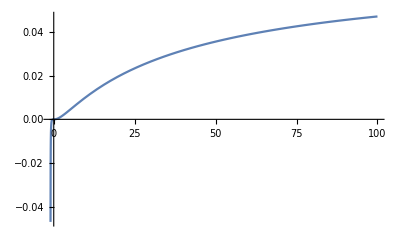

```mathematica
Plot[into1[A[lp[k]], B[lm,lp[k],Np]],{k,-0.99,100}]
```

```mathematica
(*intalgo2RDO[poly_,exp_]:=
Module[{poly1,poly2,poly3,poly4,exppoly1, exppoly2, exppoly3, exppoly4},
poly1 =poly;
	exppoly1 =efuncoef[exp, x1, 0]+ intexppoly[efuncoef[exp, x1, 2], efuncoef[exp, x1, 1]] // Simplify;
	poly2 = intgenpoly[poly1, exppoly1, x2] // Simplify;
	exppoly2 =  efuncoef[exppoly1, x2, 0] + intexppoly[efuncoef[exppoly1, x2, 2], efuncoef[exppoly1, x2, 1]] // Simplify;
	poly3 = intgenpoly[poly2, exppoly2, x1p] // Simplify;
exppoly3 = efuncoef[exppoly2, x1p, 0] + intexppoly[efuncoef[exppoly2, x1p, 2], efuncoef[exppoly2, x1p, 1]] // Simplify;
exppoly4 = efuncoef[exppoly3, x2p, 0] + intexppoly[efuncoef[exppoly3, x2p, 2], efuncoef[exppoly3, x2p, 1]] // Simplify;
poly4 = intgenpoly[poly3, exppoly3, x2p]*Exp[exppoly4] // Simplify
]*)
```

```mathematica
intalgo2RDO[intpoly1[0,0,0,0,1,-1,1,-1], exppolyinit]
```

intalgo2RDO[intpoly1[0,0,0,0,1,-1,1,-1],-a (x1^2+x1p^2+x2^2+x2p^2)+(-b^2 (x1-x1p+x2-x2p)^2-a^2 (x1^2+x1p^2+x2^2+x2p^2)+a b (3 x1^2+3 x1p^2+2 x1 x2+2 x1p x2p+3 (x2^2+x2p^2)))/(a-2 b)]